# Simple Binary Turing Machines as universal sequences generators.

First activate the following package (No need to understand what it does at this stage). Most important instructions are emphasized in red :

```mathematica
K=2;  (* All the sequences that we consider are binary, so K=2. 
       Though some functions are defined accepting arbitrary K-values, we shall always call them with the special argument K=2. *)
TripleFromFigure[fig_,K_]:={(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&[fig];
FigureFromTriple[{σ_,κ_,δ_},K_]:=σ 2 K+2 κ +δ;MyInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,2S K],S K])];MTNumberFromTriples[mytriplets_,{S_,K_}]:=FromDigits[Thread[FigureFromTriplet[#,2]&[mytriplets]],2S K];ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K];
SBTM[S_,nb_,limit_]:=Module[{K=2,tm},{tm=TuringMachine[{ChangeNumbering[nb,{S,2}],S,K},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{S,2}],S,K},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{S,K,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/S(tm11[[i]]-1)],{i,step+1}]}]};f[nb]];
activetriples[nb_,{S_,K_}]:=MyInstructionsTable[nb,{S,K}][[All,2]];
Base4SEvolution[S_,nb_,limit_]:=Module[{K=2,a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;figures={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[nb,{S,K}][[2S-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};figures=AppendTo[figures,FigureFromTriple[activatedtriple,2]];res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];figures];
Base4SPositions[S_,nb_,limit_]:=Module[{K=2,a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;indices={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[nb,{S,K}][[2S-2sigma-a[n]]];indices=AppendTo[indices,2S-2sigma-a[n]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];indices];
SingleTMStep[rule_, {S_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{S, Prepend[tape,0], pos}]
SingleTMStep[rule_, {S_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{S,tape[[-pos]]},rule]]
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
WolframInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K)+1,Mod[(#-Mod[#,2])/2,K],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
rules[S_]:=Table[Thread[Thread[Partition[Flatten[Permutations[Partition[Range[4S-1,4,-1],4]]],4S-4]->Table[Range[4S-1,4,-1],{(S-1)!}]][[k]]],{k,(S-1)!}];symS[nb_,S_]:=Module[{},{u=Partition[PadLeft[IntegerDigits[nb,4S],2S],2]};FromDigits[#,4S]&/@MapThread[ReplaceAll,{Partition[Flatten[    Map[Append[#,Last[u]]&,   (Permute[    Most[u],#]& /@Permutations[Range[S-1]])      ]],2S],rules[S]  }]]
```

```mathematica
Last[TuringMachine[{ChangeNumbering[0,{2,2}],2,2},{{1,0},{{},0}},5]][[1,3]]
```

-5

```mathematica
cpt=0;Do[If[Last[TuringMachine[{ChangeNumbering[nb,{3,2}],3,2},{{1,0},{{},0}},7]][[1,3]]==-7,cpt=cpt+1,],{nb,0,12^6-1,2}]
```

```mathematica
cpt
```

912384

```mathematica
2985983  (2-2 ⅇ^(2 S) S ExpIntegralE[-S,2 S])/.S->3//N
```

912384.

## Zone transitoire :

```mathematica
Base4SActiveTriples[nb_,{S_,K_}]:=PadLeft[IntegerDigits[nb,2S K],S K]          (*UTILE ? codeofactivetriples, activefigure*);
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0};
```

```mathematica
symS[20 12661,5]
```

{{{{0,0},{0,0},{0,253220},{2785420,3291860},{253220,0}}},{{{0,0},{0,0},{0,24480420},{269284620,318245460},{24480420,0}}},{{{0,0},{0,0},{0,64123620},{705359820,833607060},{64123620,0}}},{{{0,0},{0,0},{0,112800020},{1240800220,1466400260},{112800020,0}}},{{{0,0},{0,0},{0,9536000420},{104896004620,123968005460},{9536000420,0}}},{{{0,0},{0,0},{0,14400160020},{158401760220,187202080260},{14400160020,0}}},{{{0,0},{0,0},{0,254820},{2803020,3312660},{254820,0}}},{{{0,0},{0,0},{0,25120420},{276324620,326565460},{25120420,0}}},{{{0,0},{0,0},{0,64126820},{705395020,833648660},{64126820,0}}},{{{0,0},{0,0},{0,114720020},{1261920220,1491360260},{114720020,0}}},{{{0,0},{0,0},{0,10048000420},{110528004620,130624005460},{10048000420,0}}},{{{0,0},{0,0},{0,15168160020},{166849760220,197186080260},{15168160020,0}}},{{{0,0},{0,0},{0,25600155620},{281601711820,332802023060},{25600155620,0}}},{{{0,0},{0,0},{0,25661600020},{282277600220,333600800260},{25661600020,0}}},{{{0,0},{0,0},{0,25600157220},{281601729420,332802043860},{25600157220,0}}},{{{0,0},{0,0},{0,25662880020},{282291680220,333617440260},{25662880020,0}}},{{{0,0},{0,0},{0,50240000020},{552640000220,653120000260},{50240000020,0}}},{{{0,0},{0,0},{0,50496000020},{555456000220,656448000260},{50496000020,0}}},{{{0,0},{0,0},{0,3814400000420},{41958400004620,49587200005460},{3814400000420,0}}},{{{0,0},{0,0},{0,5760000160020},{63360001760220,74880002080260},{5760000160020,0}}},{{{0,0},{0,0},{0,3916800000420},{43084800004620,50918400005460},{3916800000420,0}}},{{{0,0},{0,0},{0,5964800160020},{65612801760220,77542402080260},{5964800160020,0}}},{{{0,0},{0,0},{0,7808064000020},{85888704000220,101504832000260},{7808064000020,0}}},{{{0,0},{0,0},{0,7910464000020},{87015104000220,102836032000260},{7910464000020,0}}}}

```mathematica
(#->TripleFromFigure[#,2]&)/@Range[0,19]
```

{0→{0,0,0},1→{0,0,1},2→{0,1,0},3→{0,1,1},4→{1,0,0},5→{1,0,1},6→{1,1,0},7→{1,1,1},8→{2,0,0},9→{2,0,1},10→{2,1,0},11→{2,1,1},12→{3,0,0},13→{3,0,1},14→{3,1,0},15→{3,1,1},16→{4,0,0},17→{4,0,1},18→{4,1,0},19→{4,1,1}}

```mathematica
(10-2Quotient[#,4])&/@Range[0,19]
```

{10,10,10,10,8,8,8,8,6,6,6,6,4,4,4,4,2,2,2,2}

```mathematica
SBTM[4,#,50]&/@{27459640,25364,2820170,10946742,305034,180551832,1483544,739434}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SBTM[5,#,50]&/@{987980890,992601268}
```

{-Graphics-,-Graphics-}

```mathematica
Base4SEvolution[5,#,200]&/@  {987980890,992601268}
```

{{10,14,15,0,4,12,15,15,15,15,0,4,17,0,10,8,8,14,15,0,4,12,15,15,15,15,15,15,0,4,17,0,10,8,8,8,8,14,15,0,4,12,15,15,15,15,15,15,15,15,0,4,17,0,10,8,8,8,8,8,8,14,15,0,4,12,15,15,15,15,15,15,15,15,15,15,0,4,17,0,10,8,8,8,8,8,8,8,8,14,15,0,4,12,15,15,15,15,15,15,15,15,15,15,15,15,0,4,17,0,10,8,8,8,8,8,8,8,8,8,8,14,15,0,4,12,15,15,15,15,15,15,15,15,15,15,15,15,15,15,0,4,17,0,10,8,8,8,8,8,8,8,8,8,8,8,8,14,15,0,4,12,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,0,4,17,0,10,8,8,8,8,8,8,8,8,8,8,8,8,8,8,14,15,0},{8,3,8,10,3,3,8,10,10,3,3,3,8,10,10,10,3,3,3,3,8,10,10,10,10,3,3,3,3,3,8,10,10,10,10,10,3,3,3,3,3,3,8,10,10,10,10,10,10,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,3,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,10,3,3,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,10,10,3,3,3,3}}

```mathematica
SBTM[4,#,15]&/@symS[342350526,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SBTM[3,#,35]&/@symS[1568804,3]
```

{-Graphics-,-Graphics-}

```mathematica
symS[2000,4]
```

{2000,721104,1936,720976,251658384,251658320}

```mathematica
symS[1000045240,5]
```

{1000045240,990978440,11137803640,6045602840,17217826440,16974402840,486452846840,486431650440,507776046840,507807520040,504128130440,504180800040,4556801803640,2508829602840,6605760045240,6605790880040,2525760002840,4574017760040,8934401826440,8832014402840,9037760098440,9037800000040,8838016002840,8945537760040}

```mathematica
Transpose[{4(3-Rest[#[[2]]&/@Position[Permutations[{c,b,a}],a]]),4(2-Rest[#[[2]]&/@Position[Permutations[{c,b,a}],b]]),4(1-Rest[#[[2]]&/@Position[Permutations[{c,b,a}],c]])}]//MatrixForm
```

(4 | -4 | 0
0 | 4 | -4
4 | 4 | -8
8 | -4 | -4
8 | 0 | -8)

```mathematica
Transpose[Position[Partition[Flatten[Rest[Permutations[Most[Partition[Range[0,7],2]]]]],6],#]][[2]]-1&/@{0,1,2,3,4,5}//MatrixForm
```

(0 | 2 | 4 | 2 | 4
1 | 3 | 5 | 3 | 5
4 | 0 | 0 | 4 | 2
5 | 1 | 1 | 5 | 3
2 | 4 | 2 | 0 | 0
3 | 5 | 3 | 1 | 1)

```mathematica
Transpose[{4(4-Rest[#[[2]]&/@Position[Permutations[{d,c,b,a}],a]]),4(3-Rest[#[[2]]&/@Position[Permutations[{d,c,b,a}],b]]),4(2-Rest[#[[2]]&/@Position[Permutations[{d,c,b,a}],c]]),4(1-Rest[#[[2]]&/@Position[Permutations[{d,c,b,a}],d]])}]//MatrixForm
```

(4 | -4 | 0 | 0
0 | 4 | -4 | 0
4 | 4 | -8 | 0
8 | -4 | -4 | 0
8 | 0 | -8 | 0
0 | 0 | 4 | -4
4 | -4 | 4 | -4
0 | 4 | 4 | -8
4 | 4 | 4 | -12
8 | -4 | 4 | -8
8 | 0 | 4 | -12
0 | 8 | -4 | -4
4 | 8 | -8 | -4
0 | 8 | 0 | -8
4 | 8 | 0 | -12
8 | 8 | -8 | -8
8 | 8 | -4 | -12
12 | -4 | -4 | -4
12 | 0 | -8 | -4
12 | -4 | 0 | -8
12 | 0 | 0 | -12
12 | 4 | -8 | -8
12 | 4 | -4 | -12)

```mathematica
Transpose[Position[Partition[Flatten[Rest[Permutations[Most[Partition[Range[0,9],2]]]]],8],#]][[2]]-1&/@{0,1,2,3,4,5,6,7}//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 2 | 2 | 4 | 6 | 4 | 6 | 2 | 2 | 4 | 6 | 4 | 6 | 2 | 2 | 4 | 6 | 4 | 6
1 | 1 | 1 | 1 | 1 | 3 | 3 | 5 | 7 | 5 | 7 | 3 | 3 | 5 | 7 | 5 | 7 | 3 | 3 | 5 | 7 | 5 | 7
2 | 4 | 6 | 4 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 6 | 2 | 2 | 6 | 4 | 4 | 6 | 2 | 2 | 6 | 4
3 | 5 | 7 | 5 | 7 | 1 | 1 | 1 | 1 | 1 | 1 | 5 | 7 | 3 | 3 | 7 | 5 | 5 | 7 | 3 | 3 | 7 | 5
6 | 2 | 2 | 6 | 4 | 4 | 6 | 2 | 2 | 6 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 4 | 6 | 4 | 2 | 2
7 | 3 | 3 | 7 | 5 | 5 | 7 | 3 | 3 | 7 | 5 | 1 | 1 | 1 | 1 | 1 | 1 | 7 | 5 | 7 | 5 | 3 | 3
4 | 6 | 4 | 2 | 2 | 6 | 4 | 6 | 4 | 2 | 2 | 6 | 4 | 6 | 4 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0
5 | 7 | 5 | 3 | 3 | 7 | 5 | 7 | 5 | 3 | 3 | 7 | 5 | 7 | 5 | 3 | 3 | 1 | 1 | 1 | 1 | 1 | 1)

## Fin de la zone transitoire

Whatever the domain (Science, litterature, music, ...), interesting data may ultimately be written as a binary files i.e. as finite sequences of 0 and 1. Binary sequences form an infinite countable set : 
Λ = {s_1={}, s_2={0}, s_3={1}, s_4={00}, s_5={01}, s_6={10}, s_7={11}, s_8={000}, s_9={001}, ... }.
The numbering is easy to remember : for example, 001 are the significant figures in the binary expansion of 9 (=1001_2, just delete the unsignificant leftmost 1). All binary sequences necessarily belong to Λ.

## Enumerating the sequences :

```mathematica
list[n_]:=PadLeft[IntegerDigits[Floor[n-2^Floor[Log[2,n]]],2], Floor[Log[2,n]]]
```

```mathematica
Table[Subscript[s, n]->list[n],{n,19}]
```

{s_1→{},s_2→{0},s_3→{1},s_4→{0,0},s_5→{0,1},s_6→{1,0},s_7→{1,1},s_8→{0,0,0},s_9→{0,0,1},s_10→{0,1,0},s_11→{0,1,1},s_12→{1,0,0},s_13→{1,0,1},s_14→{1,1,0},s_15→{1,1,1},s_16→{0,0,0,0},s_17→{0,0,0,1},s_18→{0,0,1,0},s_19→{0,0,1,1}}

```mathematica
number[suite_]:=FromDigits[Prepend[suite,1],2]      (*To decode, prepend the sequence with 1 and read the binary integer*)
```

```mathematica
number[{0,0,1,1}]
```

19

In a sense to be precised, Science may be viewed as the art of compressing experimental data without loss. 
A lossless compression procedure is equivalent to a rearrangement of Λ, s_k → s_(j(k)). 
Because of the pidgeon hole principle, no universal lossless compression algorithm can exist. In other words, it is impossible to compress all the sequences of Λ (i.e. j(k)<k for all k) : some of them are necessarily uncompressed or even dilated (i.e. j(k)≥k for some k).
Fortunately all the sequences are not equally interesting because most of them are random (and we are not supposed to be interested in random data, in science, litterature or music). 
We therefore reexpress the goal of Science : to find a procedure which strongly compresses the structured sequences at the price of slightly dilating the far more numerous uninteresting random sequences. 
Simple Binary Turing Machines (SBTM) do that job.

Our S-states SBTM (S = 2, 3, 4, ...) essentially follow Wolfram most concise design : a semi infinite (to the left) initially blank tape (= full of 0) and no explicit halting state. The head is initially in state 0 (Other states are 1, 2, ..., S-1), located at the rightmost allowed position. It moves by repeatedly executing an instructions table, reading the current printed character (κ_old = 0 or 1) and, depending of the current state of the head (σ_old), do the following : overwrite κ_old (→ κ_new), change the state of the head σ_old (→ σ_new) and move the head one cell to the left (δ=0) or to the rigth (δ=1). In short the instructions table is made of 2S instructions of the type, double → triple : (σ_old, κ_old) → (σ_new, κ_new, δ), where σ_old runs from 0 to S-1, κ_old runs from 0 to 1,  σ_new ∈ {0, ..., S-1}, κ_new ∈ {0, 1} and δ ∈ {0, 1}.
In the instructions table, the doubles are ordered in an unvarying way (Wolfram’s ordering is different and less appropriate, see below) : 
{{S-1,1} → t_1 , {S-1,0} → t_2 , {S-2,1} → t_3 , {S-2,0} → t_4 , ..., {0,1} → t_(2S-1) , {0,0} → t_(2S) }.  
4S triples are possible and a figure (in base 4S) is associated to each of them : 0 →{0,0,0}, 1 → {0,0,1}, 2 → {0,1,0}, 3→{0,1,1}, 4→{1,0,0},...,) , ..., 4S-4 → {S-1,0,0}, 4S-3 → {S-1,0,1}, 4S-2 → {S-1,1,0}, 4S-1 → {S-1,1,1}}.
Any S-states SBTM is therefore univocally numbered by the integer  t_1t_2t_3t_4...t_(2S-1)t_(2S) (in base 4S).
The machine halts when the head try to go beyond the rightmost allowed position (Trying to enter the forbidden part of the tape = crossing the red line, see the figures below). If the machine halts, the output sequence is conventionnally read (and printed) from left to right starting with the leftmost position ever attained by the head.

## With S states there are 4S distinct possible triples, t_j, each associated to a figure in base 4S :

```mathematica
Table[TripleFromFigure[j,2]->j,{j,0,7}]    (*If S=2*)
```

{{0,0,0}→0,{0,0,1}→1,{0,1,0}→2,{0,1,1}→3,{1,0,0}→4,{1,0,1}→5,{1,1,0}→6,{1,1,1}→7}

```mathematica
Table[TripleFromFigure[j,2]->j,{j,0,11}]    (*If S=3*)
```

{{0,0,0}→0,{0,0,1}→1,{0,1,0}→2,{0,1,1}→3,{1,0,0}→4,{1,0,1}→5,{1,1,0}→6,{1,1,1}→7,{2,0,0}→8,{2,0,1}→9,{2,1,0}→10,{2,1,1}→11}

```mathematica
Table[TripleFromFigure[j,2]->j,{j,0,15}]    (*If S=4*)
```

{{0,0,0}→0,{0,0,1}→1,{0,1,0}→2,{0,1,1}→3,{1,0,0}→4,{1,0,1}→5,{1,1,0}→6,{1,1,1}→7,{2,0,0}→8,{2,0,1}→9,{2,1,0}→10,{2,1,1}→11,{3,0,0}→12,{3,0,1}→13,{3,1,0}→14,{3,1,1}→15}

```mathematica
Grid[Partition[Table[TripleFromFigure[j,2]->j,{j,0,15}],4],Frame->All]
```

{0,0,0}→0 | {0,0,1}→1 | {0,1,0}→2 | {0,1,1}→3
{1,0,0}→4 | {1,0,1}→5 | {1,1,0}→6 | {1,1,1}→7
{2,0,0}→8 | {2,0,1}→9 | {2,1,0}→10 | {2,1,1}→11
{3,0,0}→12 | {3,0,1}→13 | {3,1,0}→14 | {3,1,1}→15

## Conversely, given a triple one can find the corresponding figure in base 4S :

```mathematica
FigureFromTriple[#,2]&/@{{1,1,0},{2,1,0},{0,0,1},{1,0,1},{0,1,1}}
```

{6,10,1,5,3}

## Every SBTM is univocally numbered by nb = t_1t_2t_3t_4...t_(2S-1)t_(2S), an integer in base 4S (0 ≤ nb ≤ (4S )^(2S)-1). Here are some SBTM and their instructions tables :

```mathematica
MyInstructionsTable[0,{2,2}]    (*The first two-states SBTM*)
```

{{1,1}→{0,0,0},{1,0}→{0,0,0},{0,1}→{0,0,0},{0,0}→{0,0,0}}

```mathematica
MyInstructionsTable[1,{2,2}]    (*The second two-states SBTM*)
```

{{1,1}→{0,0,0},{1,0}→{0,0,0},{0,1}→{0,0,0},{0,0}→{0,0,1}}

```mathematica
MyInstructionsTable[4095,{2,2}]     (*The last two-states SBTM*)
```

{{1,1}→{1,1,1},{1,0}→{1,1,1},{0,1}→{1,1,1},{0,0}→{1,1,1}}

```mathematica
MyInstructionsTable[80470,{4,2}]     (*Four-states SBTM number 80470*)
```

{{3,1}→{0,0,0},{3,0}→{0,0,0},{2,1}→{0,0,0},{2,0}→{0,0,1},{1,1}→{0,1,1},{1,0}→{2,1,0},{0,1}→{1,0,1},{0,0}→{1,1,0}}

```mathematica
nb=1377015;s=3;k=2;
```

```mathematica
Grid[Partition[MyInstructionsTable[346961880,{4,2}],2],Frame->All]
```

{3,1}→{0,0,1} | {3,0}→{1,0,0}
{2,1}→{2,1,0} | {2,0}→{3,1,0}
{1,1}→{0,1,1} | {1,0}→{1,1,1}
{0,1}→{3,0,1} | {0,0}→{2,0,0}

```mathematica
MachineTable[nb_,{S_,K_}]:=Grid[Partition[Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}≡#&/@PadLeft[IntegerDigits[nb,2S K],S K])],2],Frame->All]
```

```mathematica
MachineTable[346961880,{4,2}]
```

{3,1}→{0,0,1}≡1 | {3,0}→{1,0,0}≡4
{2,1}→{2,1,0}≡10 | {2,0}→{3,1,0}≡14
{1,1}→{0,1,1}≡3 | {1,0}→{1,1,1}≡7
{0,1}→{3,0,1}≡13 | {0,0}→{2,0,0}≡8

```mathematica
PadLeft[IntegerDigits[346961880,16],8]
```

{1,4,10,14,3,7,13,8}

```mathematica
SBTM[4,346961880,25]
```

-Graphics-

## 37 steps of evolution of four 4-states SBTM : 4-states SBTM number 51088454 halts in 37 steps printing the sequence 111111111, 4-states SBTM number 21088456 doesn’t halt : it loops, 4-states SBTM number 0 doesn’t halt : it glides to the left, 4-states SBTM number 10682904 doesn’t halt : it adopts a nested behaviour.

```mathematica
{SBTM[4,51088454,37], SBTM[4,21088456,37], SBTM[4,0,37], SBTM[4,10682904,37]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Some machines behave in exactly the same way :

Consider for example the 5-states machine number 987982090. In base 4S=20, 987982090 is written as 0 0 0 15 8 14 17 15 4 10, hence its sequence of triples {0,0,0,15,8,14,17,15,4,10}.

```mathematica
Base4SActiveTriples[987982090,{5,2}]       (*Figures from 0 to 4S-1*)
```

{0,0,0,15,8,14,17,15,4,10}

Given a machine, the first activated instruction is always the last one ({0,0} → t_(2S)) because the head is in state 0 and it reads 0.  Not all other instructions are necessarily activated when the machine runs. For example, running the 5-states machine number 987982090 shows that d_1 is never activated :

```mathematica
Base4SPositions[5,987982090,138]      (*Indices (k) of activated doubles (Subscript[d, k]), from 1 to 2S*)
```

{10,6,4,3,9,8,4,4,3,9,7,2,10,5,6,4,3,9,8,4,4,4,3,9,7,2,10,5,5,6,4,3,9,8,4,4,4,4,3,9,7,2,10,5,5,5,6,4,3,9,8,4,4,4,4,4,3,9,7,2,10,5,5,5,5,6,4,3,9,8,4,4,4,4,4,4,3,9,7,2,10,5,5,5,5,5,6,4,3,9,8,4,4,4,4,4,4,4,3,9,7,2,10,5,5,5,5,5,5,6,4,3,9,8,4,4,4,4,4,4,4,4,3,9,7,2,10,5,5,5,5,5,5,5,6,4,3,9}

As a consequence the 20 machines corresponding to the sequences of triples {*,0,0,15,8,14,17,15,4,10} run in the same way (where * is any figure between 0 and 19). Here are three of them :

```mathematica
{SBTM[5,FromDigits[{0,0,0,15,8,14,17,15,4,10},20],50],SBTM[5,FromDigits[{7,0,0,15,8,14,17,15,4,10},20],50],SBTM[5,FromDigits[{19,0,0,15,8,14,17,15,4,10},20],50]}
```

{-Graphics-,-Graphics-,-Graphics-}

## Their are exactly (4S )^(2S) S-states SBTM :

```mathematica
Table[{s,(4s )^(2s)},{s,2,7}]
```

{{2,4096},{3,2985984},{4,4294967296},{5,10240000000000},{6,36520347436056576},{7,182059119829942534144}}

2-states SBTM are numbered from 0 to 4095.
3-states SBTM might be numbered from 4096 to 4096+2985983 but they are usually numbered from 0 to 2985983 (keeping in mind that S=3).
and so on ... .

Theorem : every sequence is printed by infinitely many halting machines. 
Proof. Printing a sequence of n bits is impossible in less than 2n-1 steps (the minimum time for the head to move back and forth). A machine that does the job in exactly 2n-1 steps is called a printer because it behaves like a simple typewriter (it performs no sophisticated calculation). Given an arbitrary binary sequence of length, n, they are infinitely many printers of it. One of them is the (n+1)-states machine whose triples are coded in such a way that the head 1) moves to the left during n-1 steps, increasing its state by 1 at each step and printing the elements of the sequence in reversed order,  2) moves to the right during 1 step, increasing its state by 1 but leaving the tape unchanged and, 3) moves to the right during n steps, leaving both its state and the tape unchanged. There is no limit in the number of states : End of the proof.

Here is the design of a 6-states printer of the sequence, s =10101 :

```mathematica
nbprinter[s_]:=Join[{3+4 Length[s],1+4 Length[s],RandomInteger[4Length[s]+3],1+4 Length[s]+2 s⟦1⟧},Flatten[Table[{RandomInteger[4Length[s]+3],FigureFromTriple[{j,s[[j]],0},2]},{j,Length[s]-1,1,-1}]]]
```

```mathematica
SBTM[6,FromDigits[nbprinter[{1,0,1,0,1}],24],11]
```

-Graphics-

## Some other theorems obeyed by SBTM :

Theorem 1 : Whatever the number of states, all odd machines halt in one step, printing 0 or 1. SBTM number nb=4k+1 print{0}, SBTM number nb=4k+3 print {1}. For this reason only even machines will be considered in the sequel. Theorem 1 is much more complicated in Wolfram’s numbering of SBTM. 

Theorem 2 : Whatever the number of states, all even machines whose number nb is such that Mod[nb,4S]=0 loop : the head moves to the left without altering the tape.

Similar special and more or less complicated theorems may be enunciated about looping or halting machines. However no such theorem exists that decide if a given SBTM eventually halts (Undecidability of the halting of Turing machines). The consequence is that it is impossible to arrange the sequences in order of increasing complexity : the very beginning of that list is constructible but it is expected that the procedure will fail at some point possibly when S=5 (Indeed all 2, 3 and 4-states SBTM are decidable).

Here is the very beginning of the list of sequences arranged in the order of increasing complexity : 2, 3 and 4-states machines are considered.

## The very beginning of an utopian project.

We are now ready to look for the compression of sequences by programs : 

Step one : let S=2.
Run all (even) 2states-SBTM (0, 2, 4, ..., 4094) only retaining those that print a sequence never printed before. Such halting machines are called elegant. Equivalently, a machine is elegant if it prints a sequence never printed by a previous machine. Exactly eigth 2-states machines are elegant; they are numbered : 1, 3, 78, 94, 206, 222, 486 and 3308 and they print 0, 1, 00, 01, 10, 11, 111 and 101 in that order. This is the very beginning of a new order in the classification of sequences : the order of increasing algorithmic complexity.

## Two-states machines are easily calculated (0.28 seconds are required by this unoptimized Mathematica program) :

```mathematica
Timing[result2={{0},{1}};index2={1,3};depth2={1,1};
Do[{z=SingleTMEvolveList[WolframInstructionsTable[j,{2,2}],{0},9], If[Last[z][[3]]==0,{If[FreeQ[result2,Last[z][[2]]],{index2=Append[index2,j],depth2=Append[depth2,Length[z]/2]}];result2=DeleteDuplicates[Join[Append[result2,Last[z][[2]]]]]}]},      {j,0,4095,2}]]
```

{0.312,Null}

```mathematica
index2
```

{1,3,78,94,206,222,486,3308}

```mathematica
result2
```

{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1}}

```mathematica
depth2
```

{1,1,2,2,2,2,4,4}

```mathematica
list2=Table[{result2[[j]],index2[[j]],depth2[[j]]},{j,1,Length[index2]}]
```

{{{0},1,1},{{1},3,1},{{0,0},78,2},{{0,1},94,2},{{1,0},206,2},{{1,1},222,2},{{1,1,1},486,4},{{1,0,1},3308,4}}

```mathematica
Grid[Prepend[Transpose[Prepend[Transpose[list2],Table[j+1->IntegerLength[j+1,2]-1,{j,Length[list2]}]]],{"New Ordering → Complexity","Sequence","Machine Number (S=2)","Logical Depth"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightRed,{k,2,9}]]]}]
```

New Ordering → Complexity | Sequence | Machine Number | Logical Depth
2→1 | {0} | 1 | 1
3→1 | {1} | 3 | 1
4→2 | {0,0} | 78 | 2
5→2 | {0,1} | 94 | 2
6→2 | {1,0} | 206 | 2
7→2 | {1,1} | 222 | 2
8→3 | {1,1,1} | 486 | 4
9→3 | {1,0,1} | 3308 | 4

Running the 8 elegant 2states-SBTM :

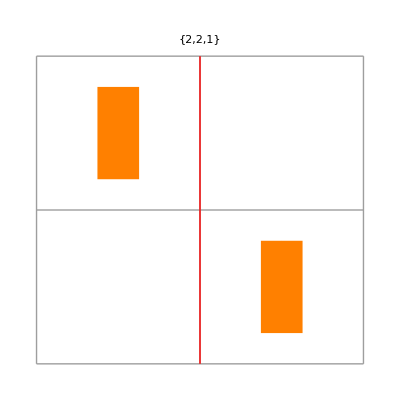
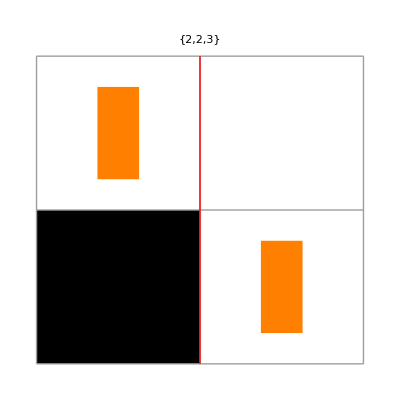
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{SBTM[2,1,10], SBTM[2,3,10], SBTM[2,78,10], SBTM[2,94,10], SBTM[2,206,10], SBTM[2,222,10], SBTM[2,486,10], SBTM[2,3308,10]}
```

Step two : let S=3.
Run all (even) 3states-SBTM (0, 2, 4, ..., 2985982) only retaining those that halt printing a sequence never printed before (i.e. by 2-states machines).

## Three-states machines are now calculated (325 seconds are required by this unoptimized Mathematica program) :

```mathematica
Timing[result3=result2;index3=index2;depth3=depth2;Do[{z=SingleTMEvolveList[WolframInstructionsTable[j,{3,2}],{0},25], If[Last[z][[3]]==0,{If[FreeQ[result3,Last[z][[2]]],{index3=Append[index3,j],depth3=Append[depth3,Length[z]/2]}];result3=DeleteDuplicates[Join[Append[result3,Last[z][[2]]]]]}]},      {j,0,2985983,2}]]
```

{319.209,Null}

```mathematica
index3
```

{1,3,78,94,206,222,486,3308,22194,22218,22312,27426,31648,31672,70210,70674,80658,80706,80752,93270,97882,124182,134696,237970,246582,319482,329562,329608,385316,391096,392176,392180,392204,945040,945064,1074620,1568804,1812450,2124286}

```mathematica
index3
```

{1,3,78,94,206,222,486,3308,22194,22218,22312,27426,31648,31672,70210,70674,80658,80706,80752,93270,97882,124182,134696,237970,246582,319482,329562,329608,385316,391096,392176,392180,392204,945040,945064,1074620,1568804,1812450,2124286}

```mathematica
result3
```

{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1},{0,0,0},{0,1,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{1,1,1,1},{1,0,1,0,1},{1,0,0,0},{1,1,1,0},{1,1,0,1},{0,0,0,1},{1,1,1,1,1},{0,1,0,1},{0,0,0,0},{0,1,1,1},{1,1,1,1,1,1},{1,0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,0},{1,1,0,1,0,1},{1,1,0,0},{1,1,0,0,1},{1,0,0,1,1},{0,1,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,1,1,1},{1,1,1,1,0},{1,1,0,0,0}}

```mathematica
depth3
```

{1,1,2,2,2,2,4,4,3,3,3,3,4,4,7,7,5,7,7,8,7,7,7,8,9,10,7,7,7,13,7,9,8,6,6,9,10,11,12}

```mathematica
list3=Table[{result3[[j]],index3[[j]],depth3[[j]]},{j,9,Length[index3]}]
```

{{{0,0,0},22194,3},{{0,1,1},22218,3},{{0,1,0},22312,3},{{0,0,1},27426,3},{{1,0,0},31648,4},{{1,1,0},31672,4},{{1,1,1,1},70210,7},{{1,0,1,0,1},70674,7},{{1,0,0,0},80658,5},{{1,1,1,0},80706,7},{{1,1,0,1},80752,7},{{0,0,0,1},93270,8},{{1,1,1,1,1},97882,7},{{0,1,0,1},124182,7},{{0,0,0,0},134696,7},{{0,1,1,1},237970,8},{{1,1,1,1,1,1},246582,9},{{1,0,0,0,1},319482,10},{{1,0,0,1},329562,7},{{1,0,1,1},329608,7},{{1,0,1,0},385316,7},{{1,1,0,1,0,1},391096,13},{{1,1,0,0},392176,7},{{1,1,0,0,1},392180,9},{{1,0,0,1,1},392204,8},{{0,1,0,0},945040,6},{{0,1,1,0},945064,6},{{0,0,1,1},1074620,9},{{1,0,1,1,1,1},1568804,10},{{1,1,1,1,0},1812450,11},{{1,1,0,0,0},2124286,12}}

```mathematica
Length[list3]
```

31

```mathematica
Grid[Prepend[Transpose[Prepend[Transpose[list3],Table[j+9->IntegerLength[j+9,2]-1,{j,Length[list3]}]]],{"New Ordering → Complexity","Sequence","Machine Number (S=3)","Logical Depth"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightGreen,{k,2,32}]]]}]
```

New Ordering → Complexity | Sequence | Machine Number | Logical Depth
10→3 | {0,0,0} | 22194 | 3
11→3 | {0,1,1} | 22218 | 3
12→3 | {0,1,0} | 22312 | 3
13→3 | {0,0,1} | 27426 | 3
14→3 | {1,0,0} | 31648 | 4
15→3 | {1,1,0} | 31672 | 4
16→4 | {1,1,1,1} | 70210 | 7
17→4 | {1,0,1,0,1} | 70674 | 7
18→4 | {1,0,0,0} | 80658 | 5
19→4 | {1,1,1,0} | 80706 | 7
20→4 | {1,1,0,1} | 80752 | 7
21→4 | {0,0,0,1} | 93270 | 8
22→4 | {1,1,1,1,1} | 97882 | 7
23→4 | {0,1,0,1} | 124182 | 7
24→4 | {0,0,0,0} | 134696 | 7
25→4 | {0,1,1,1} | 237970 | 8
26→4 | {1,1,1,1,1,1} | 246582 | 9
27→4 | {1,0,0,0,1} | 319482 | 10
28→4 | {1,0,0,1} | 329562 | 7
29→4 | {1,0,1,1} | 329608 | 7
30→4 | {1,0,1,0} | 385316 | 7
31→4 | {1,1,0,1,0,1} | 391096 | 13
32→5 | {1,1,0,0} | 392176 | 7
33→5 | {1,1,0,0,1} | 392180 | 9
34→5 | {1,0,0,1,1} | 392204 | 8
35→5 | {0,1,0,0} | 945040 | 6
36→5 | {0,1,1,0} | 945064 | 6
37→5 | {0,0,1,1} | 1074620 | 9
38→5 | {1,0,1,1,1,1} | 1568804 | 10
39→5 | {1,1,1,1,0} | 1812450 | 11
40→5 | {1,1,0,0,0} | 2124286 | 12

We have found 31 new sequences which are appended to the previous list : 0, 1, 00, 01, 10, 11, 111, 101, 000, 011, 010, ..., 11000; Some of them are dispalyed below :

```mathematica
{SBTM[3,22194,10], SBTM[3,22218,10], SBTM[3,22312,10], SBTM[3,27426,10], SBTM[3,31648,10], SBTM[3,31672,10], SBTM[3,70210,20], SBTM[3,70674,20]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Observe that the new ordering, based on increasing complexity, differs from the natural order. In particular some longer but highly regular sequences insert between shorter ones. The phenomenon increases with S (see below S=4). 
Apart from very few simple sequences (0, 1, 00, 01, 10, 11, 000, 011, 010 and 001) no printer is elegant. Possible 4-states printers of the sequence 1111 follow instructions tables like these : 
(3,1)→*, (3,0)→(0,1,1), (2,1)→*, (2,0)→(3,1,0), (1,1)→*, (1,0)→(2,1,0), (0,1)→(0,1,1), (0,0)→(1,1,0) thus nb = FromDigits[{*,3,*,14,*,10,3,6},16]. 
Even the lowest number, nb=51251766, is much larger than the elegant 70210.

```mathematica
SBTM[4,FromDigits[{0,3,0,14,0,10,3,6},16],10]
```

-Graphics-

- And so on, S = 4, 5,  ...
For each elegant machine, and the corresponding sequence, one defines :
- The algorithmic complexity, K(s), (or algorithmic entropy) of a sequence, s, = the size of its elegant program = the number of significant figures in the new ordering (starting at 2 in order to let number one for the void sequence). For example, the eighth printed sequence is {1,0,1} : 8 + 1 = 1001 (three significant figures hence, K=3).
- The logical depth, L(s), of a sequence, s, is related to the computation time of its elegant program, more precisely : L = (number_of_steps + 1)/2 (A machine always runs during an odd number of steps before halting).

## Four-states machines may not be calculated in the same way because the computation time would explode. However a C++ program does the job in less than 10 minutes (on a single core usual PC) provided two improvements are made : looping and symmetrical machines must be pre-detected. When S>2, classsym[nb_,S_] (defined in the preliminary package) detects (S-1)! equivalent machines (not necessarily distinct though distinct most of the time) where states 2, 3, ..., S are permuted without affecting the printed symbols on the tape (Remember that state 0 is protected since it is imposed as the starting state). An example :

```mathematica
classsym[1485656,4]
```

{1485656,6757012,369160028,451870876,1728061140,2870870232}

```mathematica
SBTM[4,#,20]&/@classsym[1485656,4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
#include<iostream>
#include<fstream>
#include<algorithm>
#include<vector>
#include<sstream>
#include<hash_map>using namespace std;


inline void sym4 (long long int nb,int& return1,bool& return2)/*Will return the numbers of symmetrical machines*/
{long long int quo,nx,min;
short i,j,k,nb16[6][8]={};
quo=min=nb;
for (i=7;quo>0;i--) {nb16[0][i]=quo%16;quo=quo/16;} nb16[1][0]=nb16[2][2]=nb16[3][4]=nb16[4][2]=nb16[5][4]=nb16[0][0];
nb16[1][1]=nb16[2][3]=nb16[3][5]=nb16[4][3]=nb16[5][5]=nb16[0][1];
nb16[1][4]=nb16[2][0]=nb16[3][0]=nb16[4][4]=nb16[5][2]=nb16[0][2];
nb16[1][5]=nb16[2][1]=nb16[3][1]=nb16[4][5]=nb16[5][3]=nb16[0][3];
nb16[1][2]=nb16[2][4]=nb16[3][2]=nb16[4][0]=nb16[5][0]=nb16[0][4];
nb16[1][3]=nb16[2][5]=nb16[3][3]=nb16[4][1]=nb16[5][1]=nb16[0][5];
nb16[1][6]=nb16[2][6]=nb16[3][6]=nb16[4][6]=nb16[5][6]=nb16[0][6];
nb16[1][7]=nb16[2][7]=nb16[3][7]=nb16[4][7]=nb16[5][7]=nb16[0][7];
for (i=0;i<8;i++) {switch (nb16[1][i]/4) {case 0:break;
case 1:nb16[1][i]=nb16[1][i]+4;break;
case 2:nb16[1][i]=nb16[1][i]-4;break;
case 3:break;} switch (nb16[2][i]/4) {case 0:break;
case 1:break;
case 2:nb16[2][i]=nb16[2][i]+4;break;
case 3:nb16[2][i]=nb16[2][i]-4;break;} switch (nb16[3][i]/4) {case 0:break;
case 1:nb16[3][i]=nb16[3][i]+4;break;
case 2:nb16[3][i]=nb16[3][i]+4;break;
case 3:nb16[3][i]=nb16[3][i]-8;break;} switch (nb16[4][i]/4) {case 0:break;
case 1:nb16[4][i]=nb16[4][i]+8;break;
case 2:nb16[4][i]=nb16[4][i]-4;break;
case 3:nb16[4][i]=nb16[4][i]-4;break;} switch (nb16[5][i]/4) {case 0:break;
case 1:nb16[5][i]=nb16[5][i]+8;break;
case 2:break;
case 3:nb16[5][i]=nb16[5][i]-8;break;}} k=1;
for (j=1;j<6;j++) {nx=0;for (i=0;i<8;i++) {nx=16*nx+nb16[j][i];} if (nx<min) min=nx;if (nx==nb) k++;} return1=6/k;if (nb==min) return2=true;else return2=false;/*return1 is the multiplicity (1,2,3 or 6 equivalent machines) and return2=0 (skip the computation) or 1 (compute)*/}

/*The following main program distributes the 4 states-machines between halt,loop and nest: */
int main()
{long long int i,quo,nb,nx,halt=0,loop=0,nest=0,resu[321]={0};
int j=0,k,k1,kk,ipas,jj=0,j1,nbfig[2*4+1],state,startstate,starttape[170],pos,u,posmax,posmin,posleft,posright,tripl,tape[170],return1,coupure[5]={4,16,48,96,300};
bool return2,ok;
std::vector<unsigned char>res(16777216,'0');
ofstream fichier("test.txt",ios::out|ios::trunc);/*open the output file (erasing the previous file) */
ofstream remise("nest.txt",ios::out|ios::trunc);

for (nb=0;nb<4294967296;nb+=2) {sym4(nb,return1,return2);if (return2==false) continue;/*Discards the symmetrical machines retaining that of lowest number */
else {quo=nb;for (i=8;i>0;i--) {nbfig[i]=quo%16;quo=quo/16;}/*translates nb in basis 4S */
for (k1=0;k1<170;k1++) tape[k1]=0;pos=1;state=tripl=0;ipas=1;posmax=1;/*Initialization of the current machine*/
for (k=0;k<5;k++) {posmin=pos;posright=pos;posleft=posmax;startstate=state;for (kk=posleft;kk>0;kk--) {starttape[kk]=tape[kk];}
/*Looping machines are detected by splitting the evolution in successive windows of increasing heigth,coupure[k] */

while (pos>0&&ipas<coupure[k]) {tripl=nbfig[8-2*state-tape[pos]];state=tripl/4;tape[pos]=(tripl/2) % 2;pos=pos+1-2*(tripl % 2);
if (pos>posmax) posmax=pos;if (pos<posmin) posmin=pos;
ok=true;if ((state≠startstate)||((posleft-posright)≠(posmax-pos))) {ok=false;goto next;} 
for (kk=0;kk<posleft-posmin+1;kk++) {if (tape[posmax-kk]≠starttape[posleft-kk]) {ok=false;goto next;};} if (ok==true) {loop=loop+return1;goto suivante;} next:ipas++
                                                                          ;}
/*end of while :pos=0 (=halt) or ipas has reached the bottom of the current window without detecting a periodicity (hence consider the next window)*/

if (pos==0) {halt=halt+return1;nx=1;for (i=posmax;i>0;i--) {nx=2*nx+tape[i];} 
if (res[nx]=='0') {j++;resu[j]=nx;fichier <<nb <<" : " <<ipas-1 <<" : " <<resu[j] <<"\n";res[nx]='1';} 
goto suivante;}/*Verifies that sequence number nx is found for the first time*/
                                           ;}
    ;} 
suivante:if (ok==false&&pos≠0) {nest=nest+return1;remise <<nb   <<",";}/*Non halting and non looping machines are stored in nest*/
                                                                            } 

fichier <<"Number of halting machines : " <<halt <<"\n";
fichier <<"Number of looping machines : " <<loop <<"\n";
fichier <<"Number of non halting and non looping machines : " <<nest <<"\n";
fichier.close();remise.close();
return(0);
}
```

## 283 elegant 4-states machines are found :

```mathematica
list4={{{0,0,1,0},6611802,9},{{1,0,0,0,0},16992982,7},{{1,0,0,1,0},17084248,7},{{1,0,1,1,0},17084280,7},{{0,1,0,1,0},17190648,9},{{0,1,1,1,1},17737782,7},{{0,0,1,0,0},20867732,9},{{1,0,1,1,0,1},21232248,14},{{0,1,0,1,0,1},21928566,11},{{0,1,0,0,1},21944952,7},{{0,1,1,0,1},21953144,7},{{0,0,0,0,1},23354936,16},{{0,1,0,1,1},24009272,11},{{0,1,0,0,0},24009336,7},{{0,0,1,1,1},24017492,8},{{1,0,1,1,1},24530746,10},{{1,1,0,1,1},25426548,14},{{1,1,1,0,1},25579450,14},{{1,0,1,0,0},25614186,8},{{1,1,1,1,1,0},50630230,12},{{1,1,0,1,0},50679446,10},{{1,1,1,1,1,1,1,1,1},51088454,19},{{1,1,1,1,1,1,1},51096710,17},{{1,0,1,0,1,0},51284694,8},{{0,1,1,1,0},52341908,13},{{1,1,1,0,0},52776598,11},{{1,0,1,0,1,0,1},54421716,11},{{1,0,0,0,0,0},54437910,9},{{0,0,0,1,1},54943688,13},{{1,1,1,1,0,1},54951512,12},{{1,1,1,1,1,1,1,1},54953838,15},{{1,1,1,1,1,1,0},54971992,16},{{1,0,1,0,1,0,1,0},55275226,16},{{0,0,0,0,0},55336552,13},{{0,1,1,0,1,1},55348602,13},{{1,1,0,1,1,0},55349082,14},{{1,1,1,1,1,1,1,1,0},55486614,22},{{1,0,0,1,0,0,1},55499350,10},{{0,0,1,1,0,1},56930136,13},{{1,1,0,0,0,0,0},57563764,11},{{1,0,1,1,1,1,1},57571924,10},{{1,0,0,1,0,0,0,1,0,0},59006886,36},{{1,1,0,1,1,0,1},59592374,14},{{1,1,0,0,0,0},60190392,10},{{1,0,0,0,0,1},61790324,13},{{1,1,0,1,1,1},62319768,15},{{1,0,1,1,0,0},68905566,11},{{1,0,0,1,1,1},68905628,8},{{1,0,0,1,0,0},68905630,8},{{1,0,1,0,0,0},70998638,11},{{1,0,1,0,1,1},70998726,12},{{0,1,0,0,1,0},73311128,11},{{0,0,0,1,0},73319320,12},{{1,0,0,0,0,1,1},76461914,18},{{0,0,1,0,0,0},76769822,11},{{0,0,1,0,1},77019790,9},{{0,0,1,1,0},78067870,10},{{1,1,1,0,1,0,1},78526296,10},{{1,1,1,0,0,0},78866974,11},{{0,0,0,1,1,1},80291726,14},{{1,1,1,1,1,1,1,1,1,1},82295532,19},{{1,0,0,1,0,1},83335788,12},{{0,1,0,1,1,1},83585692,15},{{0,1,1,1,1,1},86932068,9},{{0,0,1,1,1,1},93748904,14},{{1,0,1,1,1,0},95390598,14},{{1,1,0,0,0,1},101696404,16},{{1,0,1,0,0,1},101927550,16},{{1,1,0,1,1,0,1,1},102459580,17},{{1,1,1,1,1,1,1,0},102496334,25},{{1,0,0,0,1,0,0},102671256,12},{{1,0,0,0,1,1},102673276,10},{{0,1,1,0,0},104450740,7},{{0,1,0,1,0,1,0},104942268,17},{{1,1,0,0,1,0},105060956,11},{{1,1,1,1,1,0,1},106688428,20},{{0,1,1,1,0,1},108968360,9},{{1,0,1,0,1,0,1,0,1,0,1,1,1},109548462,59},{{1,1,0,0,0,0,1,1},110316158,28},{{0,0,0,0,1,1},110595916,16},{{0,0,0,0,0,1},110595918,17},{{0,1,0,0,0,0},111059384,9},{{1,1,1,1,0,0},111064972,12},{{1,1,1,1,0,1,1},111940472,10},{{1,1,1,1,0,0,1},111956856,10},{{1,0,0,0,0,1,0},115546716,11},{{0,0,0,0,1,0},115579604,14},{{1,0,1,0,1,0,1,0,1},115655514,18},{{1,0,0,0,1,0},115808852,9},{{1,1,1,1,1,1,1,1,1,1,1},117131438,31},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},117131470,48},{{1,1,0,1,1,1,1},117135566,12},{{1,1,0,0,0,0,1},117151950,14},{{1,0,1,1,1,1,1,1,1},124706698,18},{{1,0,1,1,0,1,1},126227418,17},{{1,1,1,0,1,1},126640038,9},{{1,1,1,0,1,1,1},126811450,14},{{1,1,1,1,0,0,0},127319720,12},{{1,1,1,0,0,1},128850132,14},{{1,1,1,1,0,0,1,1},128931948,18},{{1,0,1,1,1,0,1},129190614,16},{{1,0,0,1,0,1,0},133488296,18},{{1,0,1,1,1,1,0},134126150,18},{{1,0,0,0,0,0,0,0},223311978,18},{{1,0,0,0,0,0,0},223320170,15},{{0,0,0,1,0,0},224681866,15},{{0,0,1,1,1,1,1},258758830,20},{{1,0,0,0,1,1,1},279369560,14},{{1,0,0,1,1,1,1},279369592,14},{{0,0,1,0,1,1},294546298,21},{{0,0,0,0,0,0},307190376,12},{{1,0,0,1,1,0,1},312795000,18},{{1,0,1,1,1,0,0},312923976,15},{{1,0,0,1,1,0,0},312924024,14},{{1,0,0,1,0,0,0},312924056,15},{{1,0,0,0,0,0,1},323897526,16},{{1,0,0,0,0,1,0,1,1},325349112,42},{{1,0,1,1,0,0,1},325865082,23},{{1,0,0,0,0,0,0,0,0,1},325905012,35},{{1,1,0,1,0,1,1},326003444,10},{{1,1,0,1,0,1,1,1,1},328100596,15},{{1,0,0,0,1,0,1,1},328100730,36},{{1,1,0,1,0,0,1,1},329543512,45},{{1,0,1,1,0,1,0,1,0,1,0,1,0,1},329567960,42},{{1,0,0,1,1,0,1,0},330102870,19},{{0,1,0,0,0,1},330225780,16},{{0,1,0,1,1,0},330225782,14},{{1,1,0,0,1,0,1},330225784,15},{{1,1,0,1,1,1,1,1},330233972,19},{{1,0,1,1,1,1,1,1},339700412,19},{{1,1,1,0,1,0},341751720,12},{{1,0,0,1,1,0},342350526,8},{{1,0,1,0,0,0,0},342647770,17},{{1,0,1,1,0,1,0},342874740,16},{{1,1,0,0,1,1,1},344897370,11},{{1,0,1,0,0,1,0},345419708,12},{{0,1,0,1,0,0},345942968,14},{{0,0,1,0,1,0},345991772,25},{{0,0,0,1,0,1},345991934,11},{{1,1,1,0,0,1,1},346961880,11},{{1,1,1,1,1,0,1,1},347040444,32},{{1,1,1,1,1,1,1,0,1,0},348088924,52},{{1,0,1,0,1,0,1,1,1,1},348089084,39},{{0,1,0,1,0,1,0,1},349080442,24},{{1,0,1,0,1,0,0},350136216,18},{{1,0,1,0,1,1,0},351709112,22},{{1,1,0,0,1,1},352021054,9},{{0,1,0,0,1,0,0},372886228,23},{{1,0,0,1,0,1,0,1,0},373206940,16},{{1,0,0,1,0,1,0,0},374319260,16},{{1,0,0,1,0,0,1,0},374319262,14},{{1,1,1,1,0,1,0},374565628,22},{{1,0,1,0,1,0,1,0,1,0},375311272,24},{{1,0,0,0,1,0,0,0},376416476,19},{{0,1,0,0,1,1},378450298,12},{{1,1,0,0,1,0,0},378522324,14},{{1,0,1,0,1,0,1,0,1,0,1},378530548,26},{{1,1,0,1,0,0},379490204,12},{{1,0,0,1,1,0,1,0,0},379490236,20},{{1,1,0,1,0,1,0},380955640,19},{{1,1,1,0,0,1,0},382616536,14},{{1,0,0,1,1,1,0},383691576,12},{{1,1,1,0,0,0,1},383691608,16},{{1,0,0,0,1,0,1},383691768,13},{{1,1,0,1,1,1,0},384019196,12},{{1,1,0,0,1,0,0,1},384031352,17},{{1,1,0,1,0,0,0},384031484,13},{{1,0,0,0,0,0,0,1},384035448,21},{{1,1,1,1,1,0,0},384610196,19},{{1,0,1,0,0,1,0,0,1},384817780,21},{{1,0,1,1,0,1,0,0,1},385147800,29},{{1,1,0,0,0,1,1},385147832,31},{{1,1,0,0,1,1,0,0,1},385781660,23},{{1,1,0,0,1,0,0,1,1},394505972,29},{{1,0,1,1,0,1,1,1},395229942,29},{{1,1,1,1,0,1,1,1},397342868,21},{{1,1,0,0,1,0,0,0,0},491171640,29},{{1,0,0,1,0,1,0,1},523529882,16},{{1,0,0,0,0,0,0,0,1},525224630,25},{{0,1,1,0,1,0},525627066,12},{{1,0,0,1,1,0,0,1},527724186,22},{{1,1,1,1,1,1,0,1},529951800,25},{{1,0,1,1,1,0,1,1},531548246,17},{{1,0,0,0,1,1,1,1},531552340,15},{{1,0,0,1,1,1,1,1},531560532,15},{{1,0,0,1,0,0,0,0,0,0},595877798,35},{{1,1,1,0,1,1,0},618567624,17},{{1,0,0,0,1,0,0,1},647187068,17},{{1,0,1,0,1,0,1,0,1,0,1,0,1},648987480,30},{{0,0,0,0,0,0,0},795629742,13},{{1,1,0,1,1,0,0},827288276,16},{{1,1,1,1,1,1,1,1,1,1,1,1,1},860655226,44},{{0,0,1,0,0,1},883842888,19},{{0,1,1,0,0,1},883842904,11},{{1,1,1,1,0,0,0,0},888891934,18},{{1,1,1,1,1,1,1,1,1,0,1},888957784,64},{{1,0,1,1,1,1,0,1},900091752,35},{{0,1,1,1,1,0},900136568,9},{{0,1,1,1,0,0},900136664,12},{{1,0,1,0,1,1,1},910936222,19},{{1,1,0,1,1,1,1,0},911190166,17},{{1,0,1,0,1,0,1,1},912183208,21},{{0,1,1,1,1,0,1},915186046,24},{{0,1,1,0,1,1,0},915270324,18},{{1,1,0,1,1,0,1,1,0},915383198,27},{{1,1,0,1,0,1,0,1},915401436,17},{{1,1,1,1,0,1,1,1,1,1},917295992,20},{{1,1,1,1,0,1,1,0},917489560,23},{{1,0,1,0,1,1,1,1},918455188,17},{{1,0,1,0,0,1,0,0},920552340,17},{{1,1,0,1,0,1,0,1,0},921676500,16},{{1,0,1,1,0,1,1,0},922543000,18},{{0,1,1,1,1,1,1},922544458,27},{{0,1,0,1,1,0,1},922610324,13},{{1,1,0,1,1,0,1,0},922665944,22},{{1,1,0,0,0,0,0,0,0,1},927914630,31},{{1,1,0,0,0,0,0,0},936281450,22},{{0,1,1,1,1,1,0},1030638328,17},{{0,1,0,1,1,1,1},1030650456,13},{{0,0,1,1,0,0},1033661108,15},{{0,0,1,1,1,0},1034353784,14},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1066166964,60},{{0,1,0,0,1,0,0,1},1095686774,16},{{1,0,0,0,0,0,0,0,0,0,0},1099123414,30},{{0,1,0,1,0,1,0,1,0,1,0},1099411190,40},{{0,1,0,0,0,0,0},1100394168,12},{{1,1,1,1,0,0,1,0},1104112538,29},{{1,1,1,1,1,1,1,1,1,1,1,1,0},1129221270,44},{{0,0,1,1,0,1,1},1131338364,25},{{1,0,1,1,0,1,1,0,1},1131400854,23},{{1,1,1,1,1,1,1,1,1,0},1131859546,38},{{1,0,1,0,0,0,0,0},1132354204,17},{{1,1,1,0,0,0,0,0},1132354236,16},{{0,0,0,0,0,1,1},1133435580,20},{{0,1,0,1,1,1,0},1133436058,21},{{1,1,1,0,1,1,1,0},1133965240,27},{{1,1,0,0,0,1,1,0},1134455484,15},{{1,1,1,0,0,0,1,1},1134520508,16},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},1134997208,40},{{1,1,1,0,1,1,0,1,1},1135082584,49},{{0,1,1,1,1,1,1,1},1135447286,20},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1},1136045784,57},{{1,1,1,1,1,1,1,1,1,1,1,1},1136117870,47},{{1,1,1,1,1,1,1,1,1,1,0},1137109850,50},{{0,0,0,0,0,0,1},1138142328,22},{{1,1,0,1,1,0,1,1,0,1,1},1138665660,27},{{1,0,1,0,1,0,0,1},1139595354,17},{{1,1,1,1,0,1,1,1,0,1},1140255896,30},{{1,0,1,1,1,1,1,0},1140755100,16},{{1,1,0,0,1,1,0,0,1,0},1183029854,24},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},1183050430,81},{{1,0,1,0,1,0,1,0,1,0,0},1183765338,27},{{1,0,0,0,0,0,0,0,0},1184005100,21},{{1,0,0,0,1,0,1,0,1,0,1},1185698648,25},{{1,0,1,0,0,0,0,1},1185829880,15},{{1,0,0,1,0,1,1},1189321720,35},{{1,0,1,1,0,1,0,1},1189376856,15},{{1,0,0,0,0,0,0,0,0,0},1189901082,22},{{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},1190962008,56},{{1,1,1,1,1,1,1,1,0,1},1201916118,48},{{1,1,0,0,1,1,0,0},1216584286,18},{{1,1,1,0,1,0,1,1},1216584382,18},{{1,1,1,0,1,1,0,0},1233535962,25},{{1,1,1,0,0,0,0},1250123356,14},{{0,1,0,1,0,1,1},1250139326,21},{{1,0,1,0,1,1,0,1},1336828760,15},{{1,1,0,0,1,0,1,0},1401417902,26},{{0,1,1,0,0,0},1403975702,11},{{1,1,1,1,1,0,1,0},1415801564,27},{{1,1,0,0,0,1,1,0,1,1},1535550332,27},{{1,0,1,1,1,1,1,1,0},1603159034,26},{{0,0,0,0,1,0,1},1637763322,24},{{0,1,1,0,1,1,0,1,1},1644055224,18},{{1,1,1,1,1,0,0,1},1670274044,76},{{1,0,1,0,0,0,0,1,1},1671343220,21},{{1,1,1,0,1,1,0,1},1672432540,21},{{1,1,1,0,1,1,1,1},1673414812,17},{{0,1,0,0,1,0,1},1686330012,19},{{1,0,1,1,0,0,0},1786994428,17},{{1,0,0,1,0,0,1,1},1788232700,23},{{1,1,0,1,1,1,1,0,1,1,1},1939753718,56},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1},2055496636,73},{{0,0,0,0,1,0,0},3333313528,27}};
```

```mathematica
Length[list4]
```

283

```mathematica
Grid[Prepend[Transpose[Prepend[Transpose[list4],Table[j+40->IntegerLength[j+40,2]-1,{j,Length[list4]}]]],{"New Ordering → Complexity","Sequence","Machine Number (S=4)","Logical Depth"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightBrown,{k,2,284}]]]}]
```

New Ordering → Complexity | Sequence | Machine Number (S=4) | Logical Depth
41→5 | {0,0,1,0} | 6611802 | 9
42→5 | {1,0,0,0,0} | 16992982 | 7
43→5 | {1,0,0,1,0} | 17084248 | 7
44→5 | {1,0,1,1,0} | 17084280 | 7
45→5 | {0,1,0,1,0} | 17190648 | 9
46→5 | {0,1,1,1,1} | 17737782 | 7
47→5 | {0,0,1,0,0} | 20867732 | 9
48→5 | {1,0,1,1,0,1} | 21232248 | 14
49→5 | {0,1,0,1,0,1} | 21928566 | 11
50→5 | {0,1,0,0,1} | 21944952 | 7
51→5 | {0,1,1,0,1} | 21953144 | 7
52→5 | {0,0,0,0,1} | 23354936 | 16
53→5 | {0,1,0,1,1} | 24009272 | 11
54→5 | {0,1,0,0,0} | 24009336 | 7
55→5 | {0,0,1,1,1} | 24017492 | 8
56→5 | {1,0,1,1,1} | 24530746 | 10
57→5 | {1,1,0,1,1} | 25426548 | 14
58→5 | {1,1,1,0,1} | 25579450 | 14
59→5 | {1,0,1,0,0} | 25614186 | 8
60→5 | {1,1,1,1,1,0} | 50630230 | 12
61→5 | {1,1,0,1,0} | 50679446 | 10
62→5 | {1,1,1,1,1,1,1,1,1} | 51088454 | 19
63→5 | {1,1,1,1,1,1,1} | 51096710 | 17
64→6 | {1,0,1,0,1,0} | 51284694 | 8
65→6 | {0,1,1,1,0} | 52341908 | 13
66→6 | {1,1,1,0,0} | 52776598 | 11
67→6 | {1,0,1,0,1,0,1} | 54421716 | 11
68→6 | {1,0,0,0,0,0} | 54437910 | 9
69→6 | {0,0,0,1,1} | 54943688 | 13
70→6 | {1,1,1,1,0,1} | 54951512 | 12
71→6 | {1,1,1,1,1,1,1,1} | 54953838 | 15
72→6 | {1,1,1,1,1,1,0} | 54971992 | 16
73→6 | {1,0,1,0,1,0,1,0} | 55275226 | 16
74→6 | {0,0,0,0,0} | 55336552 | 13
75→6 | {0,1,1,0,1,1} | 55348602 | 13
76→6 | {1,1,0,1,1,0} | 55349082 | 14
77→6 | {1,1,1,1,1,1,1,1,0} | 55486614 | 22
78→6 | {1,0,0,1,0,0,1} | 55499350 | 10
79→6 | {0,0,1,1,0,1} | 56930136 | 13
80→6 | {1,1,0,0,0,0,0} | 57563764 | 11
81→6 | {1,0,1,1,1,1,1} | 57571924 | 10
82→6 | {1,0,0,1,0,0,0,1,0,0} | 59006886 | 36
83→6 | {1,1,0,1,1,0,1} | 59592374 | 14
84→6 | {1,1,0,0,0,0} | 60190392 | 10
85→6 | {1,0,0,0,0,1} | 61790324 | 13
86→6 | {1,1,0,1,1,1} | 62319768 | 15
87→6 | {1,0,1,1,0,0} | 68905566 | 11
88→6 | {1,0,0,1,1,1} | 68905628 | 8
89→6 | {1,0,0,1,0,0} | 68905630 | 8
90→6 | {1,0,1,0,0,0} | 70998638 | 11
91→6 | {1,0,1,0,1,1} | 70998726 | 12
92→6 | {0,1,0,0,1,0} | 73311128 | 11
93→6 | {0,0,0,1,0} | 73319320 | 12
94→6 | {1,0,0,0,0,1,1} | 76461914 | 18
95→6 | {0,0,1,0,0,0} | 76769822 | 11
96→6 | {0,0,1,0,1} | 77019790 | 9
97→6 | {0,0,1,1,0} | 78067870 | 10
98→6 | {1,1,1,0,1,0,1} | 78526296 | 10
99→6 | {1,1,1,0,0,0} | 78866974 | 11
100→6 | {0,0,0,1,1,1} | 80291726 | 14
101→6 | {1,1,1,1,1,1,1,1,1,1} | 82295532 | 19
102→6 | {1,0,0,1,0,1} | 83335788 | 12
103→6 | {0,1,0,1,1,1} | 83585692 | 15
104→6 | {0,1,1,1,1,1} | 86932068 | 9
105→6 | {0,0,1,1,1,1} | 93748904 | 14
106→6 | {1,0,1,1,1,0} | 95390598 | 14
107→6 | {1,1,0,0,0,1} | 101696404 | 16
108→6 | {1,0,1,0,0,1} | 101927550 | 16
109→6 | {1,1,0,1,1,0,1,1} | 102459580 | 17
110→6 | {1,1,1,1,1,1,1,0} | 102496334 | 25
111→6 | {1,0,0,0,1,0,0} | 102671256 | 12
112→6 | {1,0,0,0,1,1} | 102673276 | 10
113→6 | {0,1,1,0,0} | 104450740 | 7
114→6 | {0,1,0,1,0,1,0} | 104942268 | 17
115→6 | {1,1,0,0,1,0} | 105060956 | 11
116→6 | {1,1,1,1,1,0,1} | 106688428 | 20
117→6 | {0,1,1,1,0,1} | 108968360 | 9
118→6 | {1,0,1,0,1,0,1,0,1,0,1,1,1} | 109548462 | 59
119→6 | {1,1,0,0,0,0,1,1} | 110316158 | 28
120→6 | {0,0,0,0,1,1} | 110595916 | 16
121→6 | {0,0,0,0,0,1} | 110595918 | 17
122→6 | {0,1,0,0,0,0} | 111059384 | 9
123→6 | {1,1,1,1,0,0} | 111064972 | 12
124→6 | {1,1,1,1,0,1,1} | 111940472 | 10
125→6 | {1,1,1,1,0,0,1} | 111956856 | 10
126→6 | {1,0,0,0,0,1,0} | 115546716 | 11
127→6 | {0,0,0,0,1,0} | 115579604 | 14
128→7 | {1,0,1,0,1,0,1,0,1} | 115655514 | 18
129→7 | {1,0,0,0,1,0} | 115808852 | 9
130→7 | {1,1,1,1,1,1,1,1,1,1,1} | 117131438 | 31
131→7 | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 117131470 | 48
132→7 | {1,1,0,1,1,1,1} | 117135566 | 12
133→7 | {1,1,0,0,0,0,1} | 117151950 | 14
134→7 | {1,0,1,1,1,1,1,1,1} | 124706698 | 18
135→7 | {1,0,1,1,0,1,1} | 126227418 | 17
136→7 | {1,1,1,0,1,1} | 126640038 | 9
137→7 | {1,1,1,0,1,1,1} | 126811450 | 14
138→7 | {1,1,1,1,0,0,0} | 127319720 | 12
139→7 | {1,1,1,0,0,1} | 128850132 | 14
140→7 | {1,1,1,1,0,0,1,1} | 128931948 | 18
141→7 | {1,0,1,1,1,0,1} | 129190614 | 16
142→7 | {1,0,0,1,0,1,0} | 133488296 | 18
143→7 | {1,0,1,1,1,1,0} | 134126150 | 18
144→7 | {1,0,0,0,0,0,0,0} | 223311978 | 18
145→7 | {1,0,0,0,0,0,0} | 223320170 | 15
146→7 | {0,0,0,1,0,0} | 224681866 | 15
147→7 | {0,0,1,1,1,1,1} | 258758830 | 20
148→7 | {1,0,0,0,1,1,1} | 279369560 | 14
149→7 | {1,0,0,1,1,1,1} | 279369592 | 14
150→7 | {0,0,1,0,1,1} | 294546298 | 21
151→7 | {0,0,0,0,0,0} | 307190376 | 12
152→7 | {1,0,0,1,1,0,1} | 312795000 | 18
153→7 | {1,0,1,1,1,0,0} | 312923976 | 15
154→7 | {1,0,0,1,1,0,0} | 312924024 | 14
155→7 | {1,0,0,1,0,0,0} | 312924056 | 15
156→7 | {1,0,0,0,0,0,1} | 323897526 | 16
157→7 | {1,0,0,0,0,1,0,1,1} | 325349112 | 42
158→7 | {1,0,1,1,0,0,1} | 325865082 | 23
159→7 | {1,0,0,0,0,0,0,0,0,1} | 325905012 | 35
160→7 | {1,1,0,1,0,1,1} | 326003444 | 10
161→7 | {1,1,0,1,0,1,1,1,1} | 328100596 | 15
162→7 | {1,0,0,0,1,0,1,1} | 328100730 | 36
163→7 | {1,1,0,1,0,0,1,1} | 329543512 | 45
164→7 | {1,0,1,1,0,1,0,1,0,1,0,1,0,1} | 329567960 | 42
165→7 | {1,0,0,1,1,0,1,0} | 330102870 | 19
166→7 | {0,1,0,0,0,1} | 330225780 | 16
167→7 | {0,1,0,1,1,0} | 330225782 | 14
168→7 | {1,1,0,0,1,0,1} | 330225784 | 15
169→7 | {1,1,0,1,1,1,1,1} | 330233972 | 19
170→7 | {1,0,1,1,1,1,1,1} | 339700412 | 19
171→7 | {1,1,1,0,1,0} | 341751720 | 12
172→7 | {1,0,0,1,1,0} | 342350526 | 8
173→7 | {1,0,1,0,0,0,0} | 342647770 | 17
174→7 | {1,0,1,1,0,1,0} | 342874740 | 16
175→7 | {1,1,0,0,1,1,1} | 344897370 | 11
176→7 | {1,0,1,0,0,1,0} | 345419708 | 12
177→7 | {0,1,0,1,0,0} | 345942968 | 14
178→7 | {0,0,1,0,1,0} | 345991772 | 25
179→7 | {0,0,0,1,0,1} | 345991934 | 11
180→7 | {1,1,1,0,0,1,1} | 346961880 | 11
181→7 | {1,1,1,1,1,0,1,1} | 347040444 | 32
182→7 | {1,1,1,1,1,1,1,0,1,0} | 348088924 | 52
183→7 | {1,0,1,0,1,0,1,1,1,1} | 348089084 | 39
184→7 | {0,1,0,1,0,1,0,1} | 349080442 | 24
185→7 | {1,0,1,0,1,0,0} | 350136216 | 18
186→7 | {1,0,1,0,1,1,0} | 351709112 | 22
187→7 | {1,1,0,0,1,1} | 352021054 | 9
188→7 | {0,1,0,0,1,0,0} | 372886228 | 23
189→7 | {1,0,0,1,0,1,0,1,0} | 373206940 | 16
190→7 | {1,0,0,1,0,1,0,0} | 374319260 | 16
191→7 | {1,0,0,1,0,0,1,0} | 374319262 | 14
192→7 | {1,1,1,1,0,1,0} | 374565628 | 22
193→7 | {1,0,1,0,1,0,1,0,1,0} | 375311272 | 24
194→7 | {1,0,0,0,1,0,0,0} | 376416476 | 19
195→7 | {0,1,0,0,1,1} | 378450298 | 12
196→7 | {1,1,0,0,1,0,0} | 378522324 | 14
197→7 | {1,0,1,0,1,0,1,0,1,0,1} | 378530548 | 26
198→7 | {1,1,0,1,0,0} | 379490204 | 12
199→7 | {1,0,0,1,1,0,1,0,0} | 379490236 | 20
200→7 | {1,1,0,1,0,1,0} | 380955640 | 19
201→7 | {1,1,1,0,0,1,0} | 382616536 | 14
202→7 | {1,0,0,1,1,1,0} | 383691576 | 12
203→7 | {1,1,1,0,0,0,1} | 383691608 | 16
204→7 | {1,0,0,0,1,0,1} | 383691768 | 13
205→7 | {1,1,0,1,1,1,0} | 384019196 | 12
206→7 | {1,1,0,0,1,0,0,1} | 384031352 | 17
207→7 | {1,1,0,1,0,0,0} | 384031484 | 13
208→7 | {1,0,0,0,0,0,0,1} | 384035448 | 21
209→7 | {1,1,1,1,1,0,0} | 384610196 | 19
210→7 | {1,0,1,0,0,1,0,0,1} | 384817780 | 21
211→7 | {1,0,1,1,0,1,0,0,1} | 385147800 | 29
212→7 | {1,1,0,0,0,1,1} | 385147832 | 31
213→7 | {1,1,0,0,1,1,0,0,1} | 385781660 | 23
214→7 | {1,1,0,0,1,0,0,1,1} | 394505972 | 29
215→7 | {1,0,1,1,0,1,1,1} | 395229942 | 29
216→7 | {1,1,1,1,0,1,1,1} | 397342868 | 21
217→7 | {1,1,0,0,1,0,0,0,0} | 491171640 | 29
218→7 | {1,0,0,1,0,1,0,1} | 523529882 | 16
219→7 | {1,0,0,0,0,0,0,0,1} | 525224630 | 25
220→7 | {0,1,1,0,1,0} | 525627066 | 12
221→7 | {1,0,0,1,1,0,0,1} | 527724186 | 22
222→7 | {1,1,1,1,1,1,0,1} | 529951800 | 25
223→7 | {1,0,1,1,1,0,1,1} | 531548246 | 17
224→7 | {1,0,0,0,1,1,1,1} | 531552340 | 15
225→7 | {1,0,0,1,1,1,1,1} | 531560532 | 15
226→7 | {1,0,0,1,0,0,0,0,0,0} | 595877798 | 35
227→7 | {1,1,1,0,1,1,0} | 618567624 | 17
228→7 | {1,0,0,0,1,0,0,1} | 647187068 | 17
229→7 | {1,0,1,0,1,0,1,0,1,0,1,0,1} | 648987480 | 30
230→7 | {0,0,0,0,0,0,0} | 795629742 | 13
231→7 | {1,1,0,1,1,0,0} | 827288276 | 16
232→7 | {1,1,1,1,1,1,1,1,1,1,1,1,1} | 860655226 | 44
233→7 | {0,0,1,0,0,1} | 883842888 | 19
234→7 | {0,1,1,0,0,1} | 883842904 | 11
235→7 | {1,1,1,1,0,0,0,0} | 888891934 | 18
236→7 | {1,1,1,1,1,1,1,1,1,0,1} | 888957784 | 64
237→7 | {1,0,1,1,1,1,0,1} | 900091752 | 35
238→7 | {0,1,1,1,1,0} | 900136568 | 9
239→7 | {0,1,1,1,0,0} | 900136664 | 12
240→7 | {1,0,1,0,1,1,1} | 910936222 | 19
241→7 | {1,1,0,1,1,1,1,0} | 911190166 | 17
242→7 | {1,0,1,0,1,0,1,1} | 912183208 | 21
243→7 | {0,1,1,1,1,0,1} | 915186046 | 24
244→7 | {0,1,1,0,1,1,0} | 915270324 | 18
245→7 | {1,1,0,1,1,0,1,1,0} | 915383198 | 27
246→7 | {1,1,0,1,0,1,0,1} | 915401436 | 17
247→7 | {1,1,1,1,0,1,1,1,1,1} | 917295992 | 20
248→7 | {1,1,1,1,0,1,1,0} | 917489560 | 23
249→7 | {1,0,1,0,1,1,1,1} | 918455188 | 17
250→7 | {1,0,1,0,0,1,0,0} | 920552340 | 17
251→7 | {1,1,0,1,0,1,0,1,0} | 921676500 | 16
252→7 | {1,0,1,1,0,1,1,0} | 922543000 | 18
253→7 | {0,1,1,1,1,1,1} | 922544458 | 27
254→7 | {0,1,0,1,1,0,1} | 922610324 | 13
255→7 | {1,1,0,1,1,0,1,0} | 922665944 | 22
256→8 | {1,1,0,0,0,0,0,0,0,1} | 927914630 | 31
257→8 | {1,1,0,0,0,0,0,0} | 936281450 | 22
258→8 | {0,1,1,1,1,1,0} | 1030638328 | 17
259→8 | {0,1,0,1,1,1,1} | 1030650456 | 13
260→8 | {0,0,1,1,0,0} | 1033661108 | 15
261→8 | {0,0,1,1,1,0} | 1034353784 | 14
262→8 | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 1066166964 | 60
263→8 | {0,1,0,0,1,0,0,1} | 1095686774 | 16
264→8 | {1,0,0,0,0,0,0,0,0,0,0} | 1099123414 | 30
265→8 | {0,1,0,1,0,1,0,1,0,1,0} | 1099411190 | 40
266→8 | {0,1,0,0,0,0,0} | 1100394168 | 12
267→8 | {1,1,1,1,0,0,1,0} | 1104112538 | 29
268→8 | {1,1,1,1,1,1,1,1,1,1,1,1,0} | 1129221270 | 44
269→8 | {0,0,1,1,0,1,1} | 1131338364 | 25
270→8 | {1,0,1,1,0,1,1,0,1} | 1131400854 | 23
271→8 | {1,1,1,1,1,1,1,1,1,0} | 1131859546 | 38
272→8 | {1,0,1,0,0,0,0,0} | 1132354204 | 17
273→8 | {1,1,1,0,0,0,0,0} | 1132354236 | 16
274→8 | {0,0,0,0,0,1,1} | 1133435580 | 20
275→8 | {0,1,0,1,1,1,0} | 1133436058 | 21
276→8 | {1,1,1,0,1,1,1,0} | 1133965240 | 27
277→8 | {1,1,0,0,0,1,1,0} | 1134455484 | 15
278→8 | {1,1,1,0,0,0,1,1} | 1134520508 | 16
279→8 | {1,0,1,0,1,0,1,0,1,0,1,0,1,0,1} | 1134997208 | 40
280→8 | {1,1,1,0,1,1,0,1,1} | 1135082584 | 49
281→8 | {0,1,1,1,1,1,1,1} | 1135447286 | 20
282→8 | {1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1} | 1136045784 | 57
283→8 | {1,1,1,1,1,1,1,1,1,1,1,1} | 1136117870 | 47
284→8 | {1,1,1,1,1,1,1,1,1,1,0} | 1137109850 | 50
285→8 | {0,0,0,0,0,0,1} | 1138142328 | 22
286→8 | {1,1,0,1,1,0,1,1,0,1,1} | 1138665660 | 27
287→8 | {1,0,1,0,1,0,0,1} | 1139595354 | 17
288→8 | {1,1,1,1,0,1,1,1,0,1} | 1140255896 | 30
289→8 | {1,0,1,1,1,1,1,0} | 1140755100 | 16
290→8 | {1,1,0,0,1,1,0,0,1,0} | 1183029854 | 24
291→8 | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 1183050430 | 81
292→8 | {1,0,1,0,1,0,1,0,1,0,0} | 1183765338 | 27
293→8 | {1,0,0,0,0,0,0,0,0} | 1184005100 | 21
294→8 | {1,0,0,0,1,0,1,0,1,0,1} | 1185698648 | 25
295→8 | {1,0,1,0,0,0,0,1} | 1185829880 | 15
296→8 | {1,0,0,1,0,1,1} | 1189321720 | 35
297→8 | {1,0,1,1,0,1,0,1} | 1189376856 | 15
298→8 | {1,0,0,0,0,0,0,0,0,0} | 1189901082 | 22
299→8 | {1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0} | 1190962008 | 56
300→8 | {1,1,1,1,1,1,1,1,0,1} | 1201916118 | 48
301→8 | {1,1,0,0,1,1,0,0} | 1216584286 | 18
302→8 | {1,1,1,0,1,0,1,1} | 1216584382 | 18
303→8 | {1,1,1,0,1,1,0,0} | 1233535962 | 25
304→8 | {1,1,1,0,0,0,0} | 1250123356 | 14
305→8 | {0,1,0,1,0,1,1} | 1250139326 | 21
306→8 | {1,0,1,0,1,1,0,1} | 1336828760 | 15
307→8 | {1,1,0,0,1,0,1,0} | 1401417902 | 26
308→8 | {0,1,1,0,0,0} | 1403975702 | 11
309→8 | {1,1,1,1,1,0,1,0} | 1415801564 | 27
310→8 | {1,1,0,0,0,1,1,0,1,1} | 1535550332 | 27
311→8 | {1,0,1,1,1,1,1,1,0} | 1603159034 | 26
312→8 | {0,0,0,0,1,0,1} | 1637763322 | 24
313→8 | {0,1,1,0,1,1,0,1,1} | 1644055224 | 18
314→8 | {1,1,1,1,1,0,0,1} | 1670274044 | 76
315→8 | {1,0,1,0,0,0,0,1,1} | 1671343220 | 21
316→8 | {1,1,1,0,1,1,0,1} | 1672432540 | 21
317→8 | {1,1,1,0,1,1,1,1} | 1673414812 | 17
318→8 | {0,1,0,0,1,0,1} | 1686330012 | 19
319→8 | {1,0,1,1,0,0,0} | 1786994428 | 17
320→8 | {1,0,0,1,0,0,1,1} | 1788232700 | 23
321→8 | {1,1,0,1,1,1,1,0,1,1,1} | 1939753718 | 56
322→8 | {1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 2055496636 | 73
323→8 | {0,0,0,0,1,0,0} | 3333313528 | 27

At this stage, 323 binary sequences (including the trivial void sequence {} : 1+8+31+283=323) are now rearranged in order of increasing complexity. Highly regular sequence, 1^14, has been strongly compressed (K=8 bits) while the 7 bits irregular sequence, 0000100, is sligthly dilated (K=8 bits).

```mathematica
Grid[MapThread[Prepend,{Prepend[{{8^4,12^6,16^8,20^10},{2347 "(57.3%)",1825642 "(61.1%)",2737817414 "(63.7%)","???"},{1747 "(42.6%)",1159100 "(38.8%)",1555613138 "(36.2%)","???"},{2 "(4.8 10^-4)",1242 "(4.2 10^-4)",1536744 "(3.6 10^-4)","???"},{0,0,0,"???"}},{"S = 2","S = 3","S = 4","S = 5"}],{"",Total,Halting,Looping,Nested,Others}}],Frame->All]
```

| S = 2 | S = 3 | S = 4 | S = 5
Total | 4096 | 2985984 | 4294967296 | 10240000000000
Halting | 2347 (57.3%) | 1825642 (61.1%) | 2737817414 (63.7%) | ???
Looping | 1747 (42.6%) | 1159100 (38.8%) | 1555613138 (36.2%) | ???
Nesting | 2 (4.8 10^-4) | 1242 (4.2 10^-4) | 1536744 (3.6 10^-4) | ???
Others | 0 | 0 | 0 | ???

Most active and most productive machines are known under the generic appellation of Busy Beavers. Do not confuse them, for example when S=3 (see above, the ligth-green table of results) they do not coïncide. Numerical values appearing in the litterature are generally lower, the consequence of the presence of an explicit halting state :

```mathematica
Grid[MapThread[Prepend,{Prepend[{{8,31,283,"???"},{7 "steps",25 "steps",161 "steps","???"},{3 "bits",6 "bits",20 "bits","???"}},{"S = 2","S = 3","S = 4","S = 5"}],{"","Number of new elegant machines","Greatest activity","Longest printed result"}}],Frame->All]
```

| S = 2 | S = 3 | S = 4 | S = 5
Number of new elegant machines | 8 | 31 | 283 | ???
Greatest activity | 7 steps | 25 steps | 161 steps | ???
Longest printed result | 3 bits | 6 bits | 20 bits | ???

Filling additional columns in these tables will be impossible on and after some value of S, possibly S=5 : this is a consequence of the undecidability of SBTM-halting.

## Most productive machines when S = 2, 3 and 4 :

```mathematica
{SBTM[2,486,7],SBTM[3,246582,17],SBTM[4,1183050430,161]}
```

{-Graphics-,-Graphics-,-Graphics-}

## Most active machines when S = 2, 3 and 4 :

```mathematica
{SBTM[2,486,7], SBTM[3,391096,25], SBTM[4,1183050430,161]}
```

{-Graphics-,-Graphics-,-Graphics-}

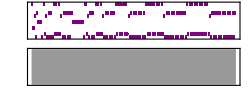

```mathematica
Sound[SoundNote[#]&/@Base4SEvolution[4,1183050430,500],30]
```

## Five-states machines present a greater challenge not only because of their huge number, 10 240 000 000 000 ! Another problem comes into sight : may not be calculated in the same way because the computation time would explode. However a C++ program does the job in less than 10 minutes (on a single core usual PC) provided two improvements are made : looping and symmetrical machines must be pre-detected. When S>2, classsym[nb_,S_] (defined in the preliminary package) detects (S-1)! equivalent machines (not necessarily distinct though distinct most of the time) where states 2, 3, ..., S are permuted without affecting the printed symbols on the tape (Remember that state 0 is protected since it is imposed as the starting state). An example :

```mathematica
classsym[147236485656,5]
```

{147236485656,249602297656,148003204056,250369016056,333475257656,333220536056,9728356487252,9728578937652,9747968807248,9747970883644,9729154137648,9729188485244,10137955204052,10138177016052,10156800805648,10156802243644,10137986136048,10138275205244,257123257652,154724536052,377602777648,377636486844,173570776048,276003206844}

```mathematica
SBTM[5,#,20]&/@classsym[147236485656,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The evolution of a machine is completely characterized by the sequence of integers (in basis 4S) that code the active triplet at each step. Here is the example of the 5-states machine 147 236 485 656.

Theorems of equivalence between machines :
- If Mod[nb,20]=0 or 2 or 4 then the machine loops (3×20^9 machines)
- If Mod[nb,20]=2, then the machine loops (20^9 machines)

```mathematica
symS[FromDigits[{7,0,0,0,7,7,7,7,7,4},20],5]
```

{3584023578944,5632037052628,3593408058944,5646820960228,7700160126312,7700210400312,8983578944,14117052628,9430458944,14821048228,20208126312,20210520312,3772160058944,5927716960228,3763222458944,5913637048228,8084208000312,8084160120312,10238720159996,10238783840396,10214460959996,10214463992396,10239996800396,10239936152396}

```mathematica
Base4SActiveTriples[42926,{5,2}]                        (*The active triples in 5-states SBTM number 147236485656*)
```

{0,0,0,0,0,0,5,7,6,6}

```mathematica
Base4SPositions[5,42926,38]
```

{10,8,7}

```mathematica
{SBTM[5,42926,12],SBTM[5,FromDigits[{0,0,0,0,0,0,5,7,6,6},20],12],SBTM[5,FromDigits[{19,19,19,19,19,19,5,7,19,6},20],12]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
symS[506,5]
```

{506,160190,506,160190,64000274,64000274,506,160190,506,160190,64000274,64000274,506,160190,506,160190,64000274,64000274,25600000358,25600000358,25600000358,25600000358,25600000358,25600000358}

```mathematica
PadLeft[IntegerDigits[#,20],10]&/@symS[506,5]
```

{{0,0,0,0,0,0,0,1,5,6},{0,0,0,0,0,1,0,0,9,10},{0,0,0,0,0,0,0,1,5,6},{0,0,0,0,0,1,0,0,9,10},{0,0,0,1,0,0,0,0,13,14},{0,0,0,1,0,0,0,0,13,14},{0,0,0,0,0,0,0,1,5,6},{0,0,0,0,0,1,0,0,9,10},{0,0,0,0,0,0,0,1,5,6},{0,0,0,0,0,1,0,0,9,10},{0,0,0,1,0,0,0,0,13,14},{0,0,0,1,0,0,0,0,13,14},{0,0,0,0,0,0,0,1,5,6},{0,0,0,0,0,1,0,0,9,10},{0,0,0,0,0,0,0,1,5,6},{0,0,0,0,0,1,0,0,9,10},{0,0,0,1,0,0,0,0,13,14},{0,0,0,1,0,0,0,0,13,14},{0,1,0,0,0,0,0,0,17,18},{0,1,0,0,0,0,0,0,17,18},{0,1,0,0,0,0,0,0,17,18},{0,1,0,0,0,0,0,0,17,18},{0,1,0,0,0,0,0,0,17,18},{0,1,0,0,0,0,0,0,17,18}}

```mathematica
Base4SActiveTriples[506,{5,2}]
```

{0,0,0,0,0,0,0,1,5,6}

```mathematica
Base4SPositions[5,506,38]
```

{10,8,9}

```mathematica
{SBTM[5,506,12],SBTM[5,FromDigits[{0,0,0,0,0,0,0,1,5,6},20],12],SBTM[5,FromDigits[{19,19,19,19,19,19,19,1,5,6},20],12]}
```

{-Graphics-,-Graphics-,-Graphics-}

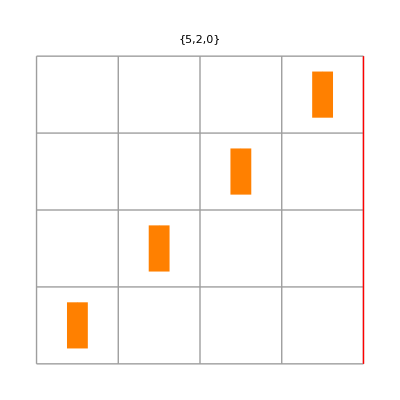
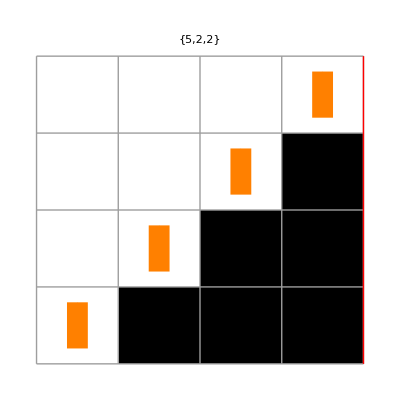
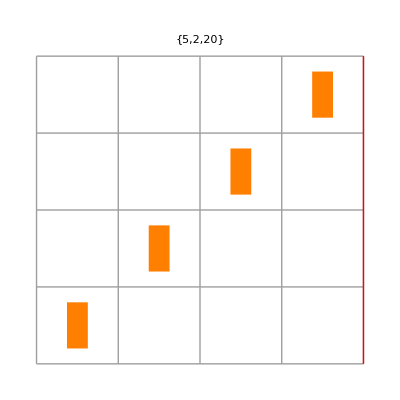
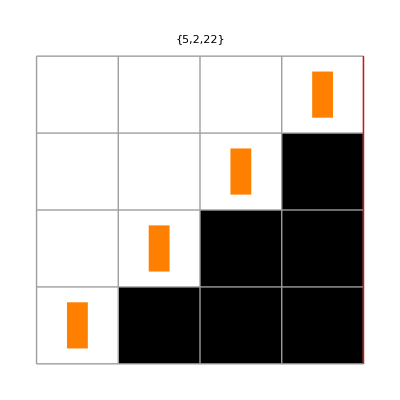
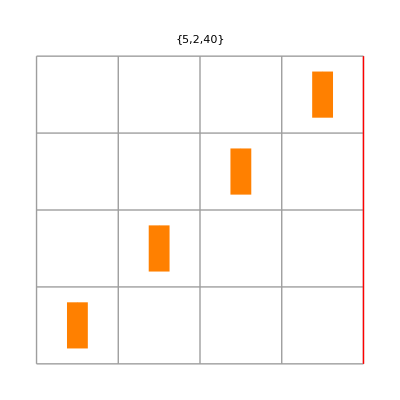
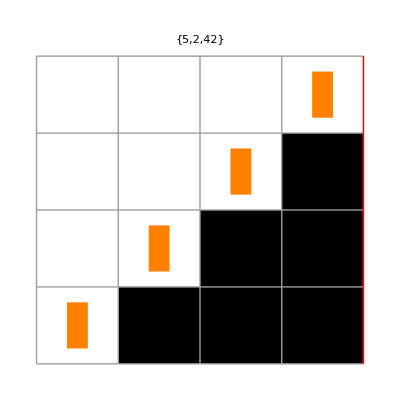
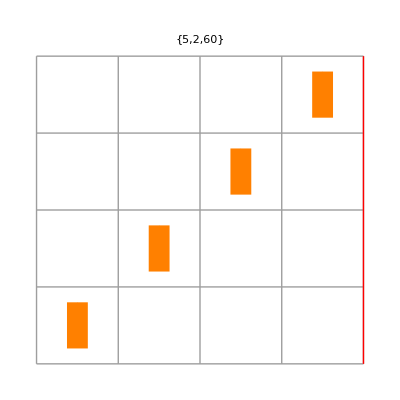
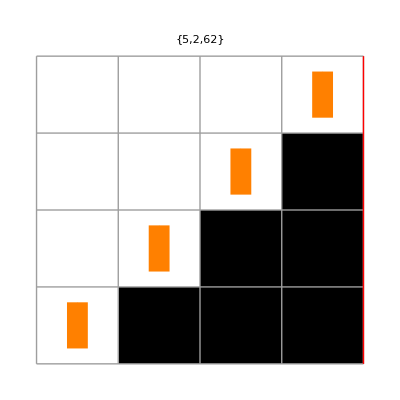
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
GraphicsGrid[Partition[Table[SBTM[5,nb,4],{nb,0,1000,2}],32]]
```

```mathematica
TripleFromFigure[#,2]&/@{16,5,14,0,16,5,14,0,16,5,14,0,16,5,14,0,16,5}
```

{{4,0,0},{1,0,1},{3,1,0},{0,0,0},{4,0,0},{1,0,1},{3,1,0},{0,0,0},{4,0,0},{1,0,1},{3,1,0},{0,0,0},{4,0,0},{1,0,1},{3,1,0},{0,0,0},{4,0,0},{1,0,1}}

```mathematica
{SBTM[5,147236485656,12],SBTM[5,FromDigits[{0,5,15,0,11,8,0,14,2,16},20],12]}
```

{-Graphics-,-Graphics-}

The evolution of a machine may be summarized by a real number, ρ = 0. t_1t_2t_3t_4 ... (0<ρ<1), where the t_i are the successive activated triples. One has : ρ_(5,147236485656) = 0.UnderBar[10  2  8  4], where the underbar means an infinite repetition. Clearly ρ is a rational number when the machine loops.
It should be obvious that 1) in the case of a halting machine, ρ is rational with terminating expansion in basis 4S; 2) in the case of a looping machine, ρ is also rational with infinite expansion in basis 4S. Otherwise, ρ is irrational, but what if the machine exhibits a nested behaviour ?
When S=2, one has the following examples (even machines from nb=3270 to 3300) :

```mathematica
GraphicsGrid[Partition[Table[SBTM[2,nb,18],{nb,3270,3300,2}],8]]
```

-Graphics-

```mathematica
Base4SEvolution[2,3292,100]     (*Exhibit the pattern : 4 6^m 3^(m+1)(m=0,1,2,3,...)*)
```

{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6}

```mathematica
b=8;RealDigits[∑_(n=0)^100 (3(b^(n+1)-1)/(b-1)+6(b^n -1)/(b-1)b^(n+1)+4 b^(2n+1))/b^((n+1)(n+2)),8,100]      (* α^m->α(b^m-1)/(b-1) ; do not forget the appropriate power of b ; (n+1)(n+2)=∑_(m=0)^n (2m+2) *)
```

{{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6},0}

```mathematica
b=8; RealDigits[-3/56∑_(n=0)^10 1/(b^(n^2+2n))+17/28∑_(n=0)^10 1/(b^(n^2+n))-3/448∑_(n=0)^10 1/(b^(n^2+3n)),8,100]    (*Show that the previous result is reducible to elliptic theta functions*)
```

{{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6},0}

```mathematica
Base4SEvolution[2,3276,100]      (*Exhibit the pattern : 4 3 4 6^m 3 1^m(m=1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,... nested, see 2 lines below !)*)
```

{4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3}

```mathematica
b=8;RealDigits[∑_(j=1)^(2^8-2) ∑_(n=1)^8 (4 b^(2n+3)+3 b^(2n+2)+4 b^(2n+1)+3 b^n+6(b^n-1)/(b-1)b^(n+1)+(b^n-1)/(b-1))/(b^((2^(n+3)-8)j-(2^(n+2)-6)+2Sum[IntegerExponent[2 k,2],{k,2j-2}])),8,100]     (*Much more complicated indeed !*)
```

{{4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3},0}

```mathematica
Table[IntegerExponent[2 k,2],{k,1,100}]    (* Obey : Subscript[m, 4k+1]=1, Subscript[m, 4k+2]=2, Subscript[m, 4k+3]=1, Subscript[m, 4k+4]=2+Subscript[m, k+1] *)
```

{1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,6,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,7,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,6,1,2,1,3}

## The evolution of a SBTM is fully summarized by the ordered list, {t_i}_List, of its activated triples or, equivalently, by a real number, ρ = 0.{t_i}_List, (in base 4S) (0< ρ<1).

### The SBTM halts : the list is finite, ρ is rational and its expansion in base 4S terminates :

```mathematica
Base4SEvolution[2,3278,18]
```

{6,3,1}

```mathematica
ρ=8^(-Length[{6,3,1}])FromDigits[{6,3,1},8]
```

409/512

### The SBTM loops : the list is infinite but ultimately periodic, ρ is rational and its expansion in base 4S doesn’t terminate :

```mathematica
Base4SEvolution[2,3270,18]
```

{6,3,0,0,6,3,0,0,6,3,0,0,6,3,0,0,6,3}

```mathematica
Frac[aperiod_,period_,b_]:=b^(-Length[aperiod])(FromDigits[aperiod,b]+FromDigits[period,b]/(b^Length[period]-1))       (*Recherche des évolutions périodiques*)
```

```mathematica
ρ=Frac[{},{6,3,0,0},8]
```

1088/1365

## Remark. Wolfram’s conventions are different (and less natural, see below) : 1) Triples are ordered in ascending order of σ_old and in descending order of κ_old 2) States are numbered from 1 to S and d ∈ {-1, 1}. Be aware that in Mathematica, the instruction TuringMachine asks for Wolfram’s conventions. Thus one needs to translate one numbering into the other. That is accomplished with the aid of the (reversible) ChangeNumbering instruction :

```mathematica
ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K]
```

```mathematica
ChangeNumbering[1084,{2,2}]
```

3856

```mathematica
Table[f[j],{j,Length[classsym[1485656,4]]}]
```

{f[1],f[2]}

```mathematica
ChangeNumbering[3856,{2,2}]
```

1084

### Two-states machines belong provably to one of these three classes : 2347 machines halt, 1747 loop and only two exhibit nested behaviour (nb = 3276 et 3292).

### Three-states machines belong provably to one of these three classes : 1825642 machines halt, 1159100 loop and1242 exhibit nested behaviour.

### Some of More-than-three-states machines surely adopt a more complex evolution scheme but there is no decision procedure to detect them because of Turing undecidability. No proof is obtainable (in the frame of say Peano arithmetics) because of Gödel undecidability.

### Simple Theorems hold however (The proofs are easy) : 1) A halting S-States machine always executes an odd number of step before halting. 2) A S-States machine halts in one step if and if its number, nb, is odd. Whatever the value of S, one half of the machines are concerned.

## Loop detection : a BTM loops if 1) it stands in a previously occupied state, and 2) it reads the same character as before, and 3) it sees the same portion of tape on the left of the actual cell and 4) it doesn’t move to the right of it during the cycle (hence never).

```mathematica
s=2;numberofsteps=4;Do[Clear[a,sigma,activetriple];i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};While[n<0 && i<numberofsteps,{activatedtriple=activetriples[nb,{s,2}][[2s-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}];left=Min[#[[2]]&/@res]   };i++];corners=#[[1]]&/@Position[res,-1,2];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],Print[nb,"     loop"],Print[nb,"    no loop found after ",numberofsteps," steps"]],{nb,3270,3293,2}]
```

3270     loop

3272     loop

3274     loop

3276    no loop found after 4 steps

3278    no loop found after 4 steps

3280     loop

3282     loop

3284    no loop found after 4 steps

3286     loop

3288     loop

3290     loop

3292    no loop found after 4 steps

```mathematica
s=2;numberofsteps=12;Do[Clear[a,sigma,activetriple];i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};While[n<0 && i<numberofsteps,{activatedtriple=activetriples[nb,{s,2}][[2s-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}];left=Min[#[[2]]&/@res]   };i++];corners=#[[1]]&/@Position[res,-1,2];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],Print[nb,"     loop"],Print[nb,"    no loop found after ",numberofsteps," steps"]],{nb,3270,3293,2}]
```

3270     loop

3272     loop

3274     loop

3276    no loop found after 12 steps

3278    no loop found after 12 steps

3280     loop

3282     loop

3284     loop

3286     loop

3288     loop

3290     loop

3292    no loop found after 12 steps

```mathematica
Grid[MapThread[Prepend,{Prepend[{{8^4,12^6,16^8,20^10},{2347 "(57.3%)",1825642 "(61.1%)",2737817414 "(63.7%)","???"},{1747 "(42.6%)",1159100 "(38.8%)",1555613138 "(36.2%)","???"},{2 "(4.8 10^-4)",1242 "(4.2 10^-4)",1536744 "(3.6 10^-4)","???"},{0,0,0,"???"}},{"S = 2","S = 3","S = 4","S = 5"}],{"",Total,Halting,Looping,Nesting,Others}}],Frame->All]
```

| S = 2 | S = 3 | S = 4 | S = 5
Total | 4096 | 2985984 | 4294967296 | 10240000000000
Halting | 2347 (57.3%) | 1825642 (61.1%) | 2737817414 (63.7%) | ???
Looping | 1747 (42.6%) | 1159100 (38.8%) | 1555613138 (36.2%) | ???
Nesting | 2 (4.8 10^-4) | 1242 (4.2 10^-4) | 1536744 (3.6 10^-4) | ???
Others | 0 | 0 | 0 | ???

## Algorithmic complexity of a finite binary sequence.

### Science is the art of compressing (binary) sequences.

### The set of binary sequences is countable. A possible enumeration is :

```mathematica
list[n_]:=PadLeft[IntegerDigits[Floor[n-2^Floor[Log[2,n]]],2], Floor[Log[2,n]]]
```

```mathematica
Table[n->list[n],{n,19}]
```

{1→{},2→{0},3→{1},4→{0,0},5→{0,1},6→{1,0},7→{1,1},8→{0,0,0},9→{0,0,1},10→{0,1,0},11→{0,1,1},12→{1,0,0},13→{1,0,1},14→{1,1,0},15→{1,1,1},16→{0,0,0,0},17→{0,0,0,1},18→{0,0,1,0},19→{0,0,1,1}}

```mathematica
number[suite_]:=FromDigits[Prepend[suite,1],2]      (*To decode, simply prepend the sequence with 1 and read the binary integer*)
```

```mathematica
number[{0,0,1,1}]
```

19

### The previous numbering makes no difference between regular and random sequences. All (binary) sequences are however not equally interesting in science : random sequences are less interesting than structured sequences. The algorithmic complexity of a sequence is usually defined as the length of the shortest program that halts and print it. SBTM allow to adapt that definition in a language-independant way : First make an inventory of k-states SBTM (k=2,3,4,...) retaining only those that halt and print a new sequence (not previously printed). The algorithmic complexity of a sequence is redefined as the number of the first SBTM in the reduced list that halts and prints it. The whole procedure can be interpreted as a semantic compression method. In practice (because of the rapidly growing number of SBTM) and in theory (because of undecidability), that task is impossible. Question however : when shall we been confronted with undecidability ? Surely not when S = 2, 3 and 4 : all those machines are decidable. What if S = 5 ?

### The logical depth of a sequence cannot be less than k, the depth of one of its printers.

I. Exploring two-states machines.

### Exploring two-states machines during 3, 6, 7, 8 and 9 steps :

```mathematica
(*Single Run during 3 steps*)       t=AbsoluteTime[];loop=halt=0;remise={};
ProvisionallyNoHaltNoLoop=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<3,{activatedtriple=activetriples[nb,{2,2}][[4-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

0.4950284

```mathematica
{halt,loop,Length[ProvisionallyNoHaltNoLoop]}
```

{256,1632,160}

```mathematica
(*Single Run during 6 steps*)       t=AbsoluteTime[];loop=halt=0;remise={};
ProvisionallyNoHaltNoLoop=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<6,{activatedtriple=activetriples[nb,{2,2}][[4-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

0.8800503

```mathematica
{halt,loop,Length[ProvisionallyNoHaltNoLoop]}
```

{288,1744,16}

```mathematica
(*Single Run during 7 steps*)       t=AbsoluteTime[];loop=halt=0;remise={};
ProvisionallyNoHaltNoLoop=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<7,{activatedtriple=activetriples[nb,{2,2}][[4-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

1.012058

```mathematica
{halt,loop,Length[ProvisionallyNoHaltNoLoop]}
```

{299,1746,3}

```mathematica
(*Single Run during 8 steps*)       t=AbsoluteTime[];loop=halt=0;remise={};
ProvisionallyNoHaltNoLoop=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<8,{activatedtriple=activetriples[nb,{2,2}][[4-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

1.134065

```mathematica
{halt,loop,Length[ProvisionallyNoHaltNoLoop]}
```

{299,1746,3}

```mathematica
(*Single Run during 9 steps*)       t=AbsoluteTime[];loop=halt=0;remise={};
ProvisionallyNoHaltNoLoop=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<9,{activatedtriple=activetriples[nb,{2,2}][[4-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,halt=halt+1,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],loop=loop+1,Sow[nb]]}    ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

1.263072

```mathematica
{halt,loop,Length[ProvisionallyNoHaltNoLoop]}
```

{299,1747,2}

Nothing change if one considers more than 9 steps : the busiest SBTM runs during 7 steps.

```mathematica
NoHaltNoLoop
```

NoHaltNoLoop

Two-states SBTM 3276 and 3292 evolutions are nested :

```mathematica
{SBTM[2,3276,30],SBTM[2,3292,30]}
```

{-Graphics-,-Graphics-}

```mathematica
{SBTM[2,3206,10],SBTM[2,3208,10]}
```

{-Graphics-,-Graphics-}

```mathematica
GraphicsGrid[{Table[SBTM[2,nb,8],{nb,0,3}]}]
```

-Graphics-

## Search for the first time a new sequence is printed : bcp plus rapide mais exige la notation de Wolfram pour les instructions : dans WolframInstructionstable, c’est mon nb qui compte !

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

```mathematica
WolframInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K)+1,Mod[(#-Mod[#,2])/2,K],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
```

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

```mathematica
SingleTMEvolveList[WolframInstructionsTable[3204,{2,2}],{0},9]
```

{{1,{0},1},{2,{0},2},{1,{1,0},3},{2,{0,1,0},4},{1,{1,0,1,0},5},{2,{0,1,0,1,0},6},{1,{1,0,1,0,1,0},7},{2,{0,1,0,1,0,1,0},8},{1,{1,0,1,0,1,0,1,0},9},{2,{0,1,0,1,0,1,0,1,0},10}}

```mathematica
SBTM[2,3204,10]
```

-Graphics-

```mathematica
Timing[result={{0},{1}};index={1,3};depth={1,1};(*On effectue une symétrisation*)

Do[
{z=SingleTMEvolveList[WolframInstructionsTable[j,{2,2}],{0},9], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]],If[FreeQ[result,Reverse[Last[z][[2]]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,Reverse[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Last[z][[2]]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Reverse[Last[z][[2]]]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Reverse[Last[z][[2]]]]]]]}]},      {j,0,4095,2}]]
```

{0.296,Null}

```mathematica
index
```

{1,3,78,78,94,94,486,486,3308,3308}

```mathematica
result
```

{{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0}}

Première méthode (SingleTMEvolveList), pas de symmétrisation, S=2 :

```mathematica
Timing[result={{0},{1}};index={1,3};depth={1,1};(*Pas de symétrisation*)

Do[
{z=SingleTMEvolveList[WolframInstructionsTable[j,{2,2}],{0},9], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]]}]},      {j,0,4095,2}]]
```

{0.312,Null}

```mathematica
index
```

{1,3,78,94,206,222,486,3308}

```mathematica
result
```

{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1}}

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->LightPink],"s=2"]
```

Serial number | Sequence | Complexity | Logical Depth | TM Number
2 | {0} | {0}→1 | 1 | 1
3 | {1} | {1}→1 | 1 | 3
4 | {0,0} | {0,0}→2 | 2 | 78
5 | {0,1} | {0,1}→2 | 2 | 94
6 | {1,0} | {1,0}→2 | 2 | 206
7 | {1,1} | {1,1}→2 | 2 | 222
8 | {1,1,1} | {0,0,0}→3 | 4 | 486
9 | {1,0,1} | {0,0,1}→3 | 4 | 3308s=2

Ceci est plus lent :

```mathematica
activetriples[nb_,{s_,k_}]:=MyInstructionsTable[nb,{s,k}][[All,2]]
```

```mathematica
activetriples[80470,{2,2}]
```

{{1,0,1},{0,0,1},{0,1,0},{1,1,0}}

```mathematica
(*essai reap and sow*)       t=AbsoluteTime[];loop=halt=0;remise=ProvisionallyNoHaltNoLoop={};halting={{1,{0}},{3,{1}}};
halting=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<3,{activatedtriple=activetriples[nb,{2,2}][[4-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0,Sow[{nb,Table[a[n],{n,ninf,-1}]}],      ]
    
           ,{nb,0,4096-1,2}]][[2,1]];AbsoluteTime[]-t
```

0.4010229

```mathematica
halting
```

{{78,{0,0}},{94,{0,1}},{110,{0,0}},{126,{0,1}},{206,{1,0}},{222,{1,1}},{238,{1,0}},{254,{1,1}},{324,{0,0}},{332,{0,0}},{340,{0,0}},{348,{0,0}},{356,{0,0}},{364,{0,0}},{372,{0,0}},{380,{0,0}},{452,{1,1}},{460,{1,1}},{468,{1,1}},{476,{1,1}},{484,{1,1}},{492,{1,1}},{500,{1,1}},{508,{1,1}},{590,{0,0}},{606,{0,1}},{622,{0,0}},{638,{0,1}},{718,{1,0}},{734,{1,1}},{750,{1,0}},{766,{1,1}},{836,{0,0}},{838,{0,0}},{844,{0,0}},{846,{0,0}},{852,{0,0}},{854,{0,0}},{860,{0,0}},{862,{0,0}},{868,{0,0}},{870,{0,0}},{876,{0,0}},{878,{0,0}},{884,{0,0}},{886,{0,0}},{892,{0,0}},{894,{0,0}},{964,{1,1}},{966,{1,0}},{972,{1,1}},{974,{1,0}},{980,{1,1}},{982,{1,0}},{988,{1,1}},{990,{1,0}},{996,{1,1}},{998,{1,0}},{1004,{1,1}},{1006,{1,0}},{1012,{1,1}},{1014,{1,0}},{1020,{1,1}},{1022,{1,0}},{1102,{0,0}},{1118,{0,1}},{1134,{0,0}},{1150,{0,1}},{1230,{1,0}},{1246,{1,1}},{1262,{1,0}},{1278,{1,1}},{1348,{0,0}},{1356,{0,0}},{1364,{0,0}},{1372,{0,0}},{1380,{0,0}},{1388,{0,0}},{1396,{0,0}},{1404,{0,0}},{1476,{1,1}},{1484,{1,1}},{1492,{1,1}},{1500,{1,1}},{1508,{1,1}},{1516,{1,1}},{1524,{1,1}},{1532,{1,1}},{1614,{0,0}},{1630,{0,1}},{1646,{0,0}},{1662,{0,1}},{1742,{1,0}},{1758,{1,1}},{1774,{1,0}},{1790,{1,1}},{1860,{0,0}},{1862,{0,1}},{1868,{0,0}},{1870,{0,1}},{1876,{0,0}},{1878,{0,1}},{1884,{0,0}},{1886,{0,1}},{1892,{0,0}},{1894,{0,1}},{1900,{0,0}},{1902,{0,1}},{1908,{0,0}},{1910,{0,1}},{1916,{0,0}},{1918,{0,1}},{1988,{1,1}},{1990,{1,1}},{1996,{1,1}},{1998,{1,1}},{2004,{1,1}},{2006,{1,1}},{2012,{1,1}},{2014,{1,1}},{2020,{1,1}},{2022,{1,1}},{2028,{1,1}},{2030,{1,1}},{2036,{1,1}},{2038,{1,1}},{2044,{1,1}},{2046,{1,1}},{2126,{0,0}},{2142,{0,1}},{2158,{0,0}},{2174,{0,1}},{2254,{1,0}},{2270,{1,1}},{2286,{1,0}},{2302,{1,1}},{2372,{0,0}},{2380,{0,0}},{2388,{0,0}},{2396,{0,0}},{2404,{0,0}},{2412,{0,0}},{2420,{0,0}},{2428,{0,0}},{2500,{1,1}},{2508,{1,1}},{2516,{1,1}},{2524,{1,1}},{2532,{1,1}},{2540,{1,1}},{2548,{1,1}},{2556,{1,1}},{2638,{0,0}},{2654,{0,1}},{2670,{0,0}},{2686,{0,1}},{2766,{1,0}},{2782,{1,1}},{2798,{1,0}},{2814,{1,1}},{2884,{0,0}},{2886,{0,0}},{2892,{0,0}},{2894,{0,0}},{2900,{0,0}},{2902,{0,0}},{2908,{0,0}},{2910,{0,0}},{2916,{0,0}},{2918,{0,0}},{2924,{0,0}},{2926,{0,0}},{2932,{0,0}},{2934,{0,0}},{2940,{0,0}},{2942,{0,0}},{3012,{1,1}},{3014,{1,0}},{3020,{1,1}},{3022,{1,0}},{3028,{1,1}},{3030,{1,0}},{3036,{1,1}},{3038,{1,0}},{3044,{1,1}},{3046,{1,0}},{3052,{1,1}},{3054,{1,0}},{3060,{1,1}},{3062,{1,0}},{3068,{1,1}},{3070,{1,0}},{3150,{0,0}},{3166,{0,1}},{3182,{0,0}},{3198,{0,1}},{3278,{1,0}},{3294,{1,1}},{3310,{1,0}},{3326,{1,1}},{3396,{0,0}},{3404,{0,0}},{3412,{0,0}},{3420,{0,0}},{3428,{0,0}},{3436,{0,0}},{3444,{0,0}},{3452,{0,0}},{3524,{1,1}},{3532,{1,1}},{3540,{1,1}},{3548,{1,1}},{3556,{1,1}},{3564,{1,1}},{3572,{1,1}},{3580,{1,1}},{3662,{0,0}},{3678,{0,1}},{3694,{0,0}},{3710,{0,1}},{3790,{1,0}},{3806,{1,1}},{3822,{1,0}},{3838,{1,1}},{3908,{0,0}},{3910,{0,1}},{3916,{0,0}},{3918,{0,1}},{3924,{0,0}},{3926,{0,1}},{3932,{0,0}},{3934,{0,1}},{3940,{0,0}},{3942,{0,1}},{3948,{0,0}},{3950,{0,1}},{3956,{0,0}},{3958,{0,1}},{3964,{0,0}},{3966,{0,1}},{4036,{1,1}},{4038,{1,1}},{4044,{1,1}},{4046,{1,1}},{4052,{1,1}},{4054,{1,1}},{4060,{1,1}},{4062,{1,1}},{4068,{1,1}},{4070,{1,1}},{4076,{1,1}},{4078,{1,1}},{4084,{1,1}},{4086,{1,1}},{4092,{1,1}},{4094,{1,1}}}

```mathematica
Length[halting]
```

256

```mathematica
DeleteDuplicates[halting,#1[[2]]==#2[[2]]&]
```

{{78,{0,0}},{94,{0,1}},{206,{1,0}},{222,{1,1}}}

Première méthode (SingleTMEvolveList), pas de symmétrisation, S=3 :

```mathematica
Timing[result={{0},{1}};index={1,3};depth={1,1};(*Pas de symétrisation*)

Do[
{z=SingleTMEvolveList[WolframInstructionsTable[j,{3,2}],{0},25], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]]}]},      {j,0,2985983,2}]]
```

{325.028,Null}

```mathematica
index
```

{1,3,162,186,450,474,1062,10864,22194,22218,22312,27426,31648,31672,70210,70674,80658,80706,80752,93270,97882,124182,134696,237970,246582,319482,329562,329608,385316,391096,392176,392180,392204,945040,945064,1074620,1568804,1812450,2124286}

```mathematica
result
```

{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1},{0,0,0},{0,1,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{1,1,1,1},{1,0,1,0,1},{1,0,0,0},{1,1,1,0},{1,1,0,1},{0,0,0,1},{1,1,1,1,1},{0,1,0,1},{0,0,0,0},{0,1,1,1},{1,1,1,1,1,1},{1,0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,0},{1,1,0,1,0,1},{1,1,0,0},{1,1,0,0,1},{1,0,0,1,1},{0,1,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,1,1,1},{1,1,1,1,0},{1,1,0,0,0}}

```mathematica
depth
```

{1,1,2,2,2,2,4,4,3,3,3,3,4,4,7,7,5,7,7,8,7,7,7,8,9,10,7,7,7,13,7,9,8,6,6,9,10,11,12}

```mathematica
list3=Table[{result[[j]],index[[j]],depth[[j]]},{j,9,Length[index]}]
```

{{{0,0,0},22194,3},{{0,1,1},22218,3},{{0,1,0},22312,3},{{0,0,1},27426,3},{{1,0,0},31648,4},{{1,1,0},31672,4},{{1,1,1,1},70210,7},{{1,0,1,0,1},70674,7},{{1,0,0,0},80658,5},{{1,1,1,0},80706,7},{{1,1,0,1},80752,7},{{0,0,0,1},93270,8},{{1,1,1,1,1},97882,7},{{0,1,0,1},124182,7},{{0,0,0,0},134696,7},{{0,1,1,1},237970,8},{{1,1,1,1,1,1},246582,9},{{1,0,0,0,1},319482,10},{{1,0,0,1},329562,7},{{1,0,1,1},329608,7},{{1,0,1,0},385316,7},{{1,1,0,1,0,1},391096,13},{{1,1,0,0},392176,7},{{1,1,0,0,1},392180,9},{{1,0,0,1,1},392204,8},{{0,1,0,0},945040,6},{{0,1,1,0},945064,6},{{0,0,1,1},1074620,9},{{1,0,1,1,1,1},1568804,10},{{1,1,1,1,0},1812450,11},{{1,1,0,0,0},2124286,12}}

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->LightPink],"s=3"]
```

Serial number | Sequence | Complexity | Logical Depth | TM Number
2 | {0} | {0}→1 | 1 | 1
3 | {1} | {1}→1 | 1 | 3
4 | {0,0} | {0,0}→2 | 2 | 162
5 | {0,1} | {0,1}→2 | 2 | 186
6 | {1,0} | {1,0}→2 | 2 | 450
7 | {1,1} | {1,1}→2 | 2 | 474
8 | {1,1,1} | {0,0,0}→3 | 4 | 1062
9 | {1,0,1} | {0,0,1}→3 | 4 | 10864
10 | {0,0,0} | {0,1,0}→3 | 3 | 22194
11 | {0,1,1} | {0,1,1}→3 | 3 | 22218
12 | {0,1,0} | {1,0,0}→3 | 3 | 22312
13 | {0,0,1} | {1,0,1}→3 | 3 | 27426
14 | {1,0,0} | {1,1,0}→3 | 4 | 31648
15 | {1,1,0} | {1,1,1}→3 | 4 | 31672
16 | {1,1,1,1} | {0,0,0,0}→4 | 7 | 70210
17 | {1,0,1,0,1} | {0,0,0,1}→4 | 7 | 70674
18 | {1,0,0,0} | {0,0,1,0}→4 | 5 | 80658
19 | {1,1,1,0} | {0,0,1,1}→4 | 7 | 80706
20 | {1,1,0,1} | {0,1,0,0}→4 | 7 | 80752
21 | {0,0,0,1} | {0,1,0,1}→4 | 8 | 93270
22 | {1,1,1,1,1} | {0,1,1,0}→4 | 7 | 97882
23 | {0,1,0,1} | {0,1,1,1}→4 | 7 | 124182
24 | {0,0,0,0} | {1,0,0,0}→4 | 7 | 134696
25 | {0,1,1,1} | {1,0,0,1}→4 | 8 | 237970
26 | {1,1,1,1,1,1} | {1,0,1,0}→4 | 9 | 246582
27 | {1,0,0,0,1} | {1,0,1,1}→4 | 10 | 319482
28 | {1,0,0,1} | {1,1,0,0}→4 | 7 | 329562
29 | {1,0,1,1} | {1,1,0,1}→4 | 7 | 329608
30 | {1,0,1,0} | {1,1,1,0}→4 | 7 | 385316
31 | {1,1,0,1,0,1} | {1,1,1,1}→4 | 13 | 391096
32 | {1,1,0,0} | {0,0,0,0,0}→5 | 7 | 392176
33 | {1,1,0,0,1} | {0,0,0,0,1}→5 | 9 | 392180
34 | {1,0,0,1,1} | {0,0,0,1,0}→5 | 8 | 392204
35 | {0,1,0,0} | {0,0,0,1,1}→5 | 6 | 945040
36 | {0,1,1,0} | {0,0,1,0,0}→5 | 6 | 945064
37 | {0,0,1,1} | {0,0,1,0,1}→5 | 9 | 1074620
38 | {1,0,1,1,1,1} | {0,0,1,1,0}→5 | 10 | 1568804
39 | {1,1,1,1,0} | {0,0,1,1,1}→5 | 11 | 1812450
40 | {1,1,0,0,0} | {0,1,0,0,0}→5 | 12 | 2124286s=3

On essaye de supprimer les symétriques : classsym est  bcp trop lent

```mathematica
sym2[nb_]:=FromDigits[Flatten[Permute[Partition[PadLeft[IntegerDigits[nb,12],6],2],Cycles[{{1,2}}]]/.{4->8,5->9,6->10,7->11,8->4,9->5,10->6,11->7}],12]
```

```mathematica
sym2[1000000]
```

594548

```mathematica
Timing[result={{0},{1}};index={1,3};depth={1,1};(*Pas de symétrisation*)

Do[{If[sym2[j]<j, ,
{z=SingleTMEvolveList[WolframInstructionsTable[j,{3,2}],{0},25], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]]}]}]},      {j,0,2985983,2}]]
```

{213.534,Null}

```mathematica
result
```

{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1},{0,0,0},{0,1,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{1,1,1,1},{1,0,1,0,1},{1,0,0,0},{1,1,1,0},{1,1,0,1},{0,0,0,1},{1,1,1,1,1},{0,1,0,1},{0,0,0,0},{0,1,1,1},{1,1,1,1,1,1},{1,0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,0},{1,1,0,1,0,1},{1,1,0,0},{1,1,0,0,1},{1,0,0,1,1},{0,1,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,1,1,1},{1,1,1,1,0},{1,1,0,0,0}}

```mathematica
Timing[Do[x=classsym[j,3], {j,0,200000,2}]]        (*Peut-on faire mieux ?*)
```

{52.37,Null}

```mathematica
Timing[Do[x=sym2[j], {j,0,200000,2}]]        (*Peut-on faire encore mieux ?*)
```

{3.245,Null}

```mathematica
sym[nb_,S_]:=FromDigits[#,4S]&/@Sort[MapThread[       ReplaceAll,  {    Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]]]&,Permute[    Most[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]],#]& /@ Permutations[Range[S-1]]   ]],2S],Table[Thread[Partition[Flatten[Permutations[Partition[Range[4S-1,4,-1],4]]],4S-4][[i]]->Range[4S-1,4,-1]],{i,(S-1)!}]    }     ] ]
```

```mathematica
Timing[Do[x=sym[j,3], {j,0,200000,2}]]          (*Plus général et plus lent*)
```

{12.262,Null}

```mathematica
sym3[nb_]:=FromDigits[#,12]&/@Sort[MapThread[       ReplaceAll,  {    Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,12],6],2]]]&,Permute[    Most[Partition[PadLeft[IntegerDigits[nb,12],6],2]],#]& /@ Permutations[Range[2]]   ]],6],Table[Thread[Partition[Flatten[Permutations[Partition[Range[11,4,-1],4]]],8][[i]]->Range[11,4,-1]],{i,2}]    }     ] ]
```

```mathematica
Timing[Do[x=sym3[j], {j,0,200000,2}]]
```

{11.076,Null}

```mathematica
Table[Thread[Partition[Flatten[Permutations[Partition[Range[11,4,-1],4]]],8][[i]]->Range[11,4,-1]],{i,2}]
```

{{11→11,10→10,9→9,8→8,7→7,6→6,5→5,4→4},{7→11,6→10,5→9,4→8,11→7,10→6,9→5,8→4}}

```mathematica
sym31[nb_]:=FromDigits[#,12]&/@Sort[MapThread[       ReplaceAll,  {    Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,12],6],2]]]&,Permute[    Most[Partition[PadLeft[IntegerDigits[nb,12],6],2]],#]& /@ Permutations[Range[2]]   ]],6],{{11->11,10->10,9->9,8->8,7->7,6->6,5->5,4->4},{7->11,6->10,5->9,4->8,11->7,10->6,9->5,8->4}}    }     ] ]
```

```mathematica
sym31[1000000]
```

{594548,1000000}

```mathematica
Timing[Do[x=sym31[j], {j,0,200000,2}]]
```

{8.112,Null}

```mathematica
Timing[Do[x=Sym4[j], {j,0,20000,2}]]
```

{4.883,Null}

Version numérique :

On passe en revue toutes les MT à disons 4 états et on s’intéresse à la première MT qui imprime une suite encore jamais imprimée. Cette machine a transité par une succession d’états avant de s’arrêter et on se fiche pas mal de savoir par quels états précisément. En fait l’état 0 est imposé au départ mais à part cela les 3 états restants peuvent être permutés sans que cela altère le résultat imprimé. En général, il existe 3!=6 manière de permuter les états 1,2 et 3 et, de fait, les 6 MT suivantes impriment la même suite :

```mathematica
GraphicsGrid[{Table[SBTM[4,classsym[1485656,4][[j]],25],{j,Length[classsym[1485656,4]]}]}]
```

-Graphics-

Les MT {1485656, 6757012, 369160028, 451870876, 1728061140, 2870870232} appartiennent à une classe de symétrie que l’on construit comme suit.  Soit à déterminer la classe de symétrie à laquelle appartient la MT 1485656.  On commence par décomposer 1485656 en base 4S=16 en exigeant 2S=8 chiffres (on complète par des 0 devant si nécessaire) :

```mathematica
Partition[PadLeft[IntegerDigits[1707327385,16],8],2]
```

{{6,5},{12,3},{11,15},{9,9}}

```mathematica
FromDigits[{6,5,12,3,11,15,9,9},16]
```

1707327385

```mathematica
classsym[1707327385,4]
```

{1707327385,2843722581,2204498909,1140304349,2079163221,3074682265}

```mathematica
{{6,5},{12,3},{11,15},{9,9}}
```

```mathematica
Partition[PadLeft[IntegerDigits[1140304349,16],8],2]
```

{{4,3},{15,7},{10,9},{13,13}}

```mathematica
PadLeft[IntegerDigits[1485656,16],8]
```

{0,0,1,6,10,11,5,8}

On groupe les chiffres par blocs de 2 comme suit :

```mathematica
Partition[PadLeft[IntegerDigits[1485656,16],8],2]
```

{{0,0},{1,6},{10,11},{5,8}}

On obtient les MT équivalentes en deux temps : 1) on permute les S-1=3 premiers blocs des  (S-1)!=6 manières possibles (on ne touche pas au dernier qui correspond à l’état 0 protégé) :

```mathematica
Permutations[Most[Partition[PadLeft[IntegerDigits[1485656,16],8],2]]]
```

{{{0,0},{1,6},{10,11}},{{0,0},{10,11},{1,6}},{{1,6},{0,0},{10,11}},{{1,6},{10,11},{0,0}},{{10,11},{0,0},{1,6}},{{10,11},{1,6},{0,0}}}

On recolle le dernier bloc, {5,8}, à la fin de chaque permutation :

```mathematica
Append[#,{5,8}]&/@Permutations[Most[Partition[PadLeft[IntegerDigits[1485656,16],8],2]]]
```

{{{0,0},{1,6},{10,11},{5,8}},{{0,0},{10,11},{1,6},{5,8}},{{1,6},{0,0},{10,11},{5,8}},{{1,6},{10,11},{0,0},{5,8}},{{10,11},{0,0},{1,6},{5,8}},{{10,11},{1,6},{0,0},{5,8}}}

La première permutation est l’identité; intéressons-nous à la deuxième {{0,0},{10,11},{1,6},{5,8}} qui a permuté les éléments en positions, 2 et 3.

2) Il faut encore faire subir la même permutation aux chiffres {4S-1=15, 4S-2=14, 13, ..., 4} regroupés par blocs de 4 (On ne touche pas aux chiffres 3,2,1,0 qui correspondent à l’état 0 protégé) :

```mathematica
Partition[Range[15,4,-1],4]
```

{{15,14,13,12},{11,10,9,8},{7,6,5,4}}

```mathematica
Permutations[Partition[Range[15,4,-1],4]]
```

{{{15,14,13,12},{11,10,9,8},{7,6,5,4}},{{15,14,13,12},{7,6,5,4},{11,10,9,8}},{{11,10,9,8},{15,14,13,12},{7,6,5,4}},{{11,10,9,8},{7,6,5,4},{15,14,13,12}},{{7,6,5,4},{15,14,13,12},{11,10,9,8}},{{7,6,5,4},{11,10,9,8},{15,14,13,12}}}

```mathematica
Range[15,4,-1]->Partition[Flatten[Permutations[Partition[Range[15,4,-1],4]]],12]
```

{15,14,13,12,11,10,9,8,7,6,5,4}→{{15,14,13,12,11,10,9,8,7,6,5,4},{15,14,13,12,7,6,5,4,11,10,9,8},{11,10,9,8,15,14,13,12,7,6,5,4},{11,10,9,8,7,6,5,4,15,14,13,12},{7,6,5,4,15,14,13,12,11,10,9,8},{7,6,5,4,11,10,9,8,15,14,13,12}}

Voici les chiffres (en bases 4S=16) de la première machine symétrique trouvée :

```mathematica
Flatten[{{0,0},{10,11},{1,6},{5,8}}]/.Thread[{15,14,13,12,11,10,9,8,7,6,5,4}->{15,14,13,12,7,6,5,4,11,10,9,8}]
```

{0,0,6,7,1,10,9,4}

```mathematica
FromDigits[{0,0,6,7,1,10,9,4},16]
```

6757012

Nous avons trouvé que la MT 6757012 imprime la même suite que la MT 1485656.  Si on envisage toutes les permutations on trouve la classe d’équivalence :

```mathematica
classsym[1485656,4]
```

{1485656,6757012,369160028,451870876,1728061140,2870870232}

```mathematica
Partition[PadLeft[IntegerDigits[12485656,16],8],2]->Partition[PadLeft[IntegerDigits[Min[classsym[12485656,4]],16],8],2]
```

{{0,0},{11,14},{8,4},{1,8}}→{{0,0},{4,8},{7,14},{1,4}}

```mathematica
Grid[Partition[Table[Partition[PadLeft[IntegerDigits[j,16],8],2]->Partition[PadLeft[IntegerDigits[Min[classsym[j,4]],16],8],2],{j,Table[RandomInteger[4294967296-1],{i,36}]}],1]]
```

{{9,9},{12,10},{15,8},{14,9}}→{{4,14},{7,12},{13,13},{6,13}}
{{9,14},{2,15},{6,2},{2,3}}→{{2,7},{10,2},{13,6},{2,3}}
{{4,0},{9,3},{2,0},{13,2}}→{{2,0},{9,3},{12,0},{5,2}}
{{15,12},{4,10},{11,7},{3,12}}→{{4,14},{11,8},{15,7},{3,8}}
{{15,15},{15,12},{12,6},{1,5}}→{{4,14},{7,4},{7,7},{1,13}}
{{11,5},{4,13},{0,15},{5,2}}→{{0,7},{12,5},{11,13},{13,2}}
{{11,14},{6,1},{11,5},{7,2}}→{{6,1},{15,10},{15,5},{7,2}}
{{9,15},{11,12},{8,9},{13,3}}→{{4,5},{5,11},{7,8},{9,3}}
{{7,2},{15,10},{7,0},{10,13}}→{{7,2},{15,10},{7,0},{10,13}}
{{8,14},{5,4},{1,3},{10,10}}→{{1,3},{4,10},{13,12},{6,6}}
{{4,2},{2,4},{13,5},{4,9}}→{{2,4},{4,2},{9,5},{4,13}}
{{3,7},{5,0},{6,9},{12,1}}→{{3,7},{5,0},{6,9},{12,1}}
{{2,3},{8,9},{9,9},{9,7}}→{{2,3},{5,5},{4,5},{5,11}}
{{10,13},{15,8},{0,10},{13,3}}→{{0,6},{6,9},{11,4},{9,3}}
{{7,13},{5,1},{12,12},{6,4}}→{{4,4},{13,1},{15,5},{14,12}}
{{11,15},{7,5},{15,4},{15,14}}→{{7,5},{15,11},{11,4},{11,10}}
{{5,12},{0,15},{6,0},{11,9}}→{{0,7},{10,0},{9,4},{15,13}}
{{13,8},{14,3},{10,10},{1,9}}→{{6,3},{14,14},{5,12},{1,13}}
{{13,3},{6,2},{3,12},{14,10}}→{{3,4},{14,2},{5,3},{6,10}}
{{7,6},{8,5},{6,10},{1,7}}→{{7,6},{8,5},{6,10},{1,7}}
{{9,5},{13,6},{1,15},{8,8}}→{{1,7},{5,14},{9,13},{8,8}}
{{3,15},{15,4},{0,10},{9,2}}→{{0,6},{3,11},{11,12},{5,2}}
{{14,0},{4,11},{9,7},{9,3}}→{{4,15},{10,0},{13,7},{13,3}}
{{13,7},{10,15},{0,6},{2,9}}→{{0,14},{9,15},{6,11},{2,5}}
{{1,15},{4,6},{12,3},{14,10}}→{{1,15},{4,6},{12,3},{14,10}}
{{0,5},{8,14},{7,8},{6,1}}→{{0,5},{8,14},{7,8},{6,1}}
{{7,8},{15,8},{0,4},{11,13}}→{{0,12},{7,8},{15,8},{11,5}}
{{13,10},{8,8},{14,3},{0,5}}→{{6,3},{8,8},{5,10},{0,13}}
{{10,13},{13,10},{9,2},{14,9}}→{{5,2},{6,9},{9,6},{10,5}}
{{4,4},{2,1},{14,1},{5,15}}→{{2,1},{4,4},{10,1},{5,11}}
{{11,0},{8,15},{1,8},{14,5}}→{{1,4},{7,0},{4,11},{10,13}}
{{5,11},{14,13},{12,8},{8,0}}→{{4,8},{6,5},{13,11},{8,0}}
{{11,0},{3,9},{14,10},{2,0}}→{{3,13},{6,14},{15,0},{2,0}}
{{5,9},{0,3},{0,8},{9,9}}→{{0,3},{0,12},{9,13},{13,13}}
{{14,1},{7,2},{2,9},{11,0}}→{{2,5},{10,1},{15,2},{7,0}}
{{13,8},{7,6},{10,7},{9,6}}→{{6,15},{9,4},{15,14},{5,14}}

```mathematica
Table[RandomInteger[4294967296-1],{i,4}]
```

{327673271,451263327,2768645506,1567959088}

Evidemment seul le plus petit numéro compte pusique ces 6 MT impriment la même suite, d’où l’idée d’introduire une instruction supplémentaire dans la grande boucle qui fait tourner les MT sur tous les numéros, nb=0 to (4S)^(2S)-1 : si nb>Min[classsym[nb]], alors passer au nb suivant, sinon calculer.  Il serait intéressant de voir si on gagne du temps de calcul : certes, on doit appeler classsym à chaque pas mais presque (cfr remarque ci-dessous) 5 fois sur 6 on court-circuite le calcul long (et lorsque S=5, cela monte à 23 fois sur 24).

Remarque : il existe des cas heureusement peu nombreux où toutes les permutations ne donnent pas des MT distinctes.  Ainsi :

```mathematica
classsym[14656,4]
```

{14656,3473536,1023410240}

```mathematica
classsym[1,4]
```

{1}

```mathematica
Permutations[Reverse[Range[4]]]
```

{{4,3,2,1},{4,3,1,2},{4,2,3,1},{4,2,1,3},{4,1,3,2},{4,1,2,3},{3,4,2,1},{3,4,1,2},{3,2,4,1},{3,2,1,4},{3,1,4,2},{3,1,2,4},{2,4,3,1},{2,4,1,3},{2,3,4,1},{2,3,1,4},{2,1,4,3},{2,1,3,4},{1,4,3,2},{1,4,2,3},{1,3,4,2},{1,3,2,4},{1,2,4,3},{1,2,3,4}}

```mathematica
Partition[Range[19,4,-1],4]
```

{{19,18,17,16},{15,14,13,12},{11,10,9,8},{7,6,5,4}}

```mathematica
Permutations[Range[4]][[24]]
```

{4,3,2,1}

```mathematica
Flatten[Position[Permutations[Range[4]][[24]],#]&/@Permutations[Range[4]][[24]]]
```

{1,2,3,4}

```mathematica
Position[Permutations[Range[4]][[24]],3]
```

{{2}}

```mathematica
rule[S_]:=Range[4S-1,4,-1]->Flatten[4+Mod[Partition[Range[4S-1,4,-1],4]-4Reverse[Range[S-1]]-4Flatten[Position[Permutations[Range[S-1]][[1]],#]&/@Reverse[Range[S-1]]],4S-4]]
```

```mathematica
rule[4]
```

{15,14,13,12,11,10,9,8,7,6,5,4}→{7,6,5,4,11,10,9,8,15,14,13,12}

```mathematica
Most[Partition[PadLeft[IntegerDigits[1000000,12],6],2]]/.
```

{{4,0},{2,8}}

```mathematica
Timing[result={{0},{1}};index={1,3};depth={1,1};(*Pas de symétrisation*)

Do[{If[sym31[j][[1]]<j, ,
{z=SingleTMEvolveList[WolframInstructionsTable[j,{3,2}],{0},25], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,j],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]]}]}]},      {j,0,2985983,2}]]
```

{291.441,Null}

```mathematica
result
```

{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1},{0,0,0},{0,1,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{1,1,1,1},{1,0,1,0,1},{1,0,0,0},{1,1,1,0},{1,1,0,1},{0,0,0,1},{1,1,1,1,1},{0,1,0,1},{0,0,0,0},{0,1,1,1},{1,1,1,1,1,1},{1,0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,0},{1,1,0,1,0,1},{1,1,0,0},{1,1,0,0,1},{1,0,0,1,1},{0,1,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,1,1,1},{1,1,1,1,0},{1,1,0,0,0}}

```mathematica
index
```

{1,3,162,186,450,474,1062,10864,22194,22218,22312,27426,31648,31672,70210,70674,80658,80706,80752,93270,97882,124182,134696,237970,246582,319482,329562,329608,385316,391096,392176,392180,392204,945040,945064,1074620,1568804,1812450,2124286}

```mathematica
Table[Thread[Partition[Flatten[Permutations[Partition[Range[15,4,-1],4]]],12][[i]]->Range[15,4,-1]],{i,6}]
```

{{15→15,14→14,13→13,12→12,11→11,10→10,9→9,8→8,7→7,6→6,5→5,4→4},{15→15,14→14,13→13,12→12,7→11,6→10,5→9,4→8,11→7,10→6,9→5,8→4},{11→15,10→14,9→13,8→12,15→11,14→10,13→9,12→8,7→7,6→6,5→5,4→4},{11→15,10→14,9→13,8→12,7→11,6→10,5→9,4→8,15→7,14→6,13→5,12→4},{7→15,6→14,5→13,4→12,15→11,14→10,13→9,12→8,11→7,10→6,9→5,8→4},{7→15,6→14,5→13,4→12,11→11,10→10,9→9,8→8,15→7,14→6,13→5,12→4}}

```mathematica
sym41[nb_]:=FromDigits[#,16]&/@Sort[MapThread[       ReplaceAll,  {    Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,16],8],2]]]&,Permute[    Most[Partition[PadLeft[IntegerDigits[nb,16],8],2]],#]& /@ Permutations[Range[3]]   ]],8],{{15->15,14->14,13->13,12->12,11->11,10->10,9->9,8->8,7->7,6->6,5->5,4->4},{15->15,14->14,13->13,12->12,7->11,6->10,5->9,4->8,11->7,10->6,9->5,8->4},{11->15,10->14,9->13,8->12,15->11,14->10,13->9,12->8,7->7,6->6,5->5,4->4},{11->15,10->14,9->13,8->12,7->11,6->10,5->9,4->8,15->7,14->6,13->5,12->4},{7->15,6->14,5->13,4->12,15->11,14->10,13->9,12->8,11->7,10->6,9->5,8->4},{7->15,6->14,5->13,4->12,11->11,10->10,9->9,8->8,15->7,14->6,13->5,12->4}}    }     ] ]
```

```mathematica
Timing[Do[x=sym41[j], {j,0,200000,2}]]
```

{21.372,Null}

```mathematica
sym[nb_,S_]:=FromDigits[#,4S]&/@Sort[MapThread[       ReplaceAll,  {    Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]]]&,Permute[    Most[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]],#]& /@ Permutations[Range[S-1]]   ]],2S],Table[Thread[Partition[Flatten[Permutations[Partition[Range[4S-1,4,-1],4]]],4S-4][[i]]->Range[4S-1,4,-1]],{i,(S-1)!}]    }     ] ]
```

```mathematica
(*Il faudrait passer de 12^6 à moins en excluant les MT qui se sont arrêtées ou qui ont bouclé en 3 pas : hélas mon pgm prend trop de temps = 416+54 s.  Bizarrement c'est la première partie qui coûte (While ... i++]; = 364 sec)*)       t=AbsoluteTime[];loop=halt=0;remise={};
ProvisionallyNoHaltNoLoop=Reap[Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<3,{activatedtriple=activetriples[nb,{3,2}][[6-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]   };i++];

If[n==0, (*do nothing : next nb*)           ,    {corners=#[[1]]&/@Position[res,-1,2];left=Min[#[[2]]&/@res];Do[{corners=AppendTo[corners,Select[#[[1]]&/@Position[res,k,2],#>Max[corners]&]]},{k,-2,left,-1}];listetest={#[[1]],FromDigits[#[[3]],2]}&/@res[[Flatten[corners]]];If[Length[Union[listetest]]≠Length[listetest],   (*do nothing : next nb*)       ,Sow[nb]]}    ]
    
           ,{nb,0,2985984-1,2}]][[2,1]];AbsoluteTime[]-t
```

416.4427315

Tentative de simplification dans la détection des machines périodiques :

```mathematica
(*Il faudrait passer de 12^6 à moins en excluant les MT qui se sont arrêtées ou qui ont bouclé en 3 pas : hélas mon pgm prend trop de temps = 416+54 s*)       t=AbsoluteTime[];loop=halt=0;remise={};
ProvisionallyNoHaltNoLoop=Do[         Clear[a]; i=0;a[_]=0;n=ninf=-1;sigma=0;res={{0,-1,{0}}};

While[n<0 && i<18,{activatedtriple=activetriples[nb,{3,2}][[6-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]];   
If[MemberQ[res,{sigma,n+1,Table[a[j],{j,ninf,n}]}],Print["period detected within 18 steps"],res=AppendTo[res,{sigma,n,Table[a[j],{j,ninf,n}]}]]   };i++];
    
           ,{nb,{1505034}}];AbsoluteTime[]-t
```

period detected within 18 steps

period detected within 18 steps

period detected within 18 steps

«6 more identical outputs»

0.012001

```mathematica
res
```

{{0,-1,{0}},{1,-2,{0}},{2,-1,{1,1}},{1,-2,{1}},{1,-3,{0}},{2,-2,{1,1}},{1,-3,{1}},{1,-4,{0}},{2,-3,{1,1}},{1,-4,{1}},{1,-5,{0}},{2,-4,{1,1}},{1,-5,{1}},{1,-6,{0}},{2,-5,{1,1}},{1,-6,{1}},{1,-7,{0}},{2,-6,{1,1}},{1,-7,{1}}}

```mathematica
res
```

```mathematica
{{0,-1,{0}},{1,-2,{0}},{2,-1,{1,1}},{1,-2,{1}},{1,-3,{0}},{2,-2,{1,1}},{1,-3,{1}},{1,-4,{0}},{2,-3,{1,1}},{1,-4,{1}},{1,-5,{0}},{2,-4,{1,1}},{1,-5,{1}},{1,-6,{0}},{2,-5,{1,1}},{1,-6,{1}},{1,-7,{0}},{2,-6,{1,1}},{1,-7,{1}}}
```

```mathematica
SBTM[3,1505034,18]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[SBTM[3,nb,8],{nb,1505000,1505040}],10]]
```

-Graphics-

Fin de la tentative de simplification.

```mathematica
Length[ProvisionallyNoHaltNoLoop]
```

241920

```mathematica
Timing[result={{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1}};index={1,3,78,94,206,222,486,3308};depth={1,1};(*Pas de symétrisation*)

Do[
{z=SingleTMEvolveList[WolframInstructionsTable[ProvisionallyNoHaltNoLoop[[j]],{3,2}],{0},25], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,ProvisionallyNoHaltNoLoop[[j]]],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]]}]},      {j,Length[ProvisionallyNoHaltNoLoop]}]]
```

{54.663,Null}

```mathematica
index
```

{1,3,78,94,206,222,486,3308,22194,22218,22312,27426,31648,31672,70210,70674,80658,80706,80752,93270,97882,124182,134696,237970,246582,319482,329562,329608,385316,391096,392176,392180,392204,945040,945064,1074620,1568804,1812450,2124286}

```mathematica
index
```

{1,3,162,186,450,474,1062,10864,22194,22218,22312,27426,31648,31672,70210,70674,80658,80706,80752,93270,97882,124182,134696,237970,246582,319482,329562,329608,385316,391096,392176,392180,392204,945040,945064,1074620,1568804,1812450,2124286}

```mathematica
result
```

{{0},{1},{0,0},{0,1},{1,0},{1,1},{1,1,1},{1,0,1},{0,0,0},{0,1,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{1,1,1,1},{1,0,1,0,1},{1,0,0,0},{1,1,1,0},{1,1,0,1},{0,0,0,1},{1,1,1,1,1},{0,1,0,1},{0,0,0,0},{0,1,1,1},{1,1,1,1,1,1},{1,0,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,0},{1,1,0,1,0,1},{1,1,0,0},{1,1,0,0,1},{1,0,0,1,1},{0,1,0,0},{0,1,1,0},{0,0,1,1},{1,0,1,1,1,1},{1,1,1,1,0},{1,1,0,0,0}}

## Usually many SBTM print the same sequence when halting. In particular, at most (S-1)! SBTM print the same sequence, under permutation of states 1, 2, 3, .., S-1.

```mathematica
classsym[nb_,S_]:=Table[FromDigits[Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]]]&,Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]],2S][[n]]/.Table[Flatten[Table[ 4j+m->4(S-Transpose[Position[Permutations[Reverse[Range[S-1]]],j]][[2]])[[k]]+m,{j,S-1},{m,0,3}]],{k,(S-1)!}][[n]],4S],{n,Length[Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]}]
```

```mathematica
classsym[1485656,4]
```

{1485656,6757012,369160028,451870876,1728061140,2870870232}

```mathematica
classsym[1000,3]
```

{1000,207452}

```mathematica
Partition[Table[j->TripleFromFigure[j,2],{j,0,11}],4]    (*If S=3*)
```

{{0→{0,0,0},1→{0,0,1},2→{0,1,0},3→{0,1,1}},{4→{1,0,0},5→{1,0,1},6→{1,1,0},7→{1,1,1}},{8→{2,0,0},9→{2,0,1},10→{2,1,0},11→{2,1,1}}}

```mathematica
Partition[IntegerDigits[#,12],2]&/@classsym[1000000,3]
```

{{{4,0},{2,8},{5,4}},{{2,4},{8,0},{9,8}}}

```mathematica
Partition[IntegerDigits[#,12],2]&/@classsym[1000100,3]
```

{{{4,0},{2,9},{1,8}},{{2,5},{8,0},{1,4}}}

```mathematica
Partition[IntegerDigits[#,12],2]&/@classsym[1000200,3]
```

{{{4,0},{2,9},{10,0}},{{2,5},{8,0},{6,0}}}

```mathematica
Partition[IntegerDigits[#,12],2]&/@classsym[1000300,3]
```

{{{4,0},{2,10},{6,4}},{{2,6},{8,0},{10,8}}}

```mathematica
Partition[IntegerDigits[#,12],2]&/@classsym[1000400,3]
```

{{{4,0},{2,11},{2,8}},{{2,7},{8,0},{2,4}}}

```mathematica
Partition[IntegerDigits[#,12],2]&/@classsym[1700400,3]
```

{{{6,10},{0,0},{4,0}},{{10,6},{8,0}}}

```mathematica
classsym[100000000000,5]
```

{100000000000,99968048000,94777920000,94720144800,76857968000,76832144800,7219424000000,7219392048000,5189120480000,3141120001200,5171200528000,3123232001200,9216237120000,9216192112800,9228928480000,9223808001200,9216000560800,9216019521200,237168000,224112800,12928528000,7840001200,17920560800,17939521200}

```mathematica
classsym[2,5]
```

{2}

```mathematica
SBTM[5,100000000000,18]
```

-Graphics-

```mathematica
MyInstructionsTable[100000000000,{5,2}]
```

{{4,1}→{0,0,0},{4,0}→{0,1,1},{3,1}→{4,1,0},{3,0}→{0,1,0},{2,1}→{2,1,0},{2,0}→{0,0,0},{1,1}→{0,0,0},{1,0}→{0,0,0},{0,1}→{0,0,0},{0,0}→{0,0,0}}

```mathematica
MyInstructionsTable[0,{5,2}]
```

{{4,1}→{0,0,0},{4,0}→{0,0,0},{3,1}→{0,0,0},{3,0}→{0,0,0},{2,1}→{0,0,0},{2,0}→{0,0,0},{1,1}→{0,0,0},{1,0}→{0,0,0},{0,1}→{0,0,0},{0,0}→{0,0,0}}

```mathematica
GraphicsGrid[{Table[SBTM[5,classsym[100000000000,5][[j]],8],{j,Length[classsym[1485656,5]]}]}]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[SBTM[4,classsym[1485656,4][[j]],25],{j,Length[classsym[1485656,4]]}]}]
```

-Graphics-

```mathematica
classsym[1128,4]
```

{1128,524452,67108972}

```mathematica
s=4;k=2;limit=10;Do[{Clear[tm];tm=TuringMachine[{ChangeNumbering[classsym[1128,4][[j]],{s,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[classsym[1128,4][[j]],{s,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[j]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,classsym[1128,4][[j]]},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{j,Length[classsym[1128,4]]}]
```

```mathematica
Table[f[j],{j,Length[classsym[1128,4]]}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
classsym[1126668,4]
```

{1126668,3215628,285225224,288423940,822087944,823197700}

```mathematica
s=4;k=2;limit=10;Do[{Clear[tm];tm=TuringMachine[{ChangeNumbering[classsym[1126668,4][[j]],{s,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[classsym[1126668,4][[j]],{s,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[j]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,classsym[1126668,4][[j]]},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{j,Length[classsym[1126668,4]]}]
```

```mathematica
Table[f[j],{j,Length[classsym[1126668,4]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Summary when s=2 (Symmetric sequences have been set as equals) :

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->LightPink],"s=2"]
```

Serial number | Sequence | Complexity | Logical Depth | TM Number
2 | {0} | {0}→1 | 1 | 64
3 | {1} | {1}→1 | 1 | 64
4 | {0,0} | {0,0}→2 | 2 | 261
5 | {1,1} | {0,1}→2 | 2 | 261
6 | {0,1} | {1,0}→2 | 3 | 299
7 | {1,0} | {1,1}→2 | 3 | 299
8 | {1,1,1} | {0,0,0}→3 | 4 | 423
9 | {0,0,0} | {0,0,1}→3 | 4 | 423
10 | {1,0,1} | {0,1,0}→3 | 4 | 2867
11 | {0,1,0} | {0,1,1}→3 | 4 | 2867s=2

## At most 6 TM do the same under permutation of states 1, 2, 3.

```mathematica
s=4;k=2;nb=1485656;Permutations[Range[s-1]]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
Partition[ActiveTriplets[nb,{4,2}],2]
```

{{0,0},{1,6},{10,11},{5,8}}

```mathematica
Append[#,4]&/@Permutations[Range[s-1]]
```

{{1,2,3,4},{1,3,2,4},{2,1,3,4},{2,3,1,4},{3,1,2,4},{3,2,1,4}}

```mathematica
InversePermutation[#]&/@Permutations[Range[s-1]]
```

{{1,2,3},{1,3,2},{2,1,3},{3,1,2},{2,3,1},{3,2,1}}

```mathematica
InvPerm=InversePermutation[#]&/@(Append[#,4]&/@Permutations[Range[s-1]])
```

{{1,2,3,4},{1,3,2,4},{2,1,3,4},{3,1,2,4},{2,3,1,4},{3,2,1,4}}

```mathematica
a=Partition[Flatten[Permute[Partition[ActiveTriplets[nb,{4,2}],2],#]&/@(InvPerm)],s k]
```

{{0,0,1,6,10,11,5,8},{0,0,10,11,1,6,5,8},{1,6,0,0,10,11,5,8},{10,11,0,0,1,6,5,8},{1,6,10,11,0,0,5,8},{10,11,1,6,0,0,5,8}}

```mathematica
b=Partition[Flatten[Permute[Partition[Drop[Range[4s-1],s-1],s],#]&/@Permutations[Reverse[Range[s-1]]]],4s-4]
```

{{12,13,14,15,8,9,10,11,4,5,6,7},{12,13,14,15,4,5,6,7,8,9,10,11},{8,9,10,11,12,13,14,15,4,5,6,7},{8,9,10,11,4,5,6,7,12,13,14,15},{4,5,6,7,12,13,14,15,8,9,10,11},{4,5,6,7,8,9,10,11,12,13,14,15}}

```mathematica
classsym[1485656,4]
```

{1485656,6757012,369160028,451870876,1728061140,2870870232}

```mathematica
classsym=Table[FromDigits[a[[j]]/.Thread[b[[1]]->b[[j]]],2s k],{j,(s-1)!}]
```

{1485656,6757012,369160028,1728061140,451870876,2870870232}

```mathematica
classsym={};Do[{a=Partition[Flatten[Permute[Partition[ActiveTriplets[nb,{4,2}],2],#]&/@(InvPerm)],s k];b=Partition[Flatten[Permute[Partition[Drop[Range[4s-1],s-1],s],#]&/@Permutations[Reverse[Range[s-1]]]],4s-4];classsym=DeleteDuplicates[Flatten[AppendTo[classsym,Table[FromDigits[a[[j]]/.Thread[b[[1]]->b[[j]]],2s k],{j,(s-1)!}]]]]},{nb,1000000000,1000001000,2}]
```

```mathematica
Length[classsym]
```

3006

```mathematica
IntegerDigits[#,16]&/@{1485656,6757012,369160028,1728061140,451870876,2870870232}
```

{{1,6,10,11,5,8},{6,7,1,10,9,4},{1,6,0,0,14,15,5,12},{6,7,0,0,1,14,13,4},{1,10,14,15,0,0,9,12},{10,11,1,14,0,0,13,8}}

```mathematica
{{0,0,1,6,10,11,5,8},{6,7,1,10,9,4},{1,6,0,0,14,15,5,12},{6,7,0,0,1,14,13,4},{1,10,14,15,0,0,9,12},{10,11,1,14,0,0,13,8}}
```

## Halting TM in three steps.

```mathematica
MTNumberFromTriplets[{{0,0,1},{1,0,1},{1,0,0},{0,0,0},{0,0,1},{1,1,1},{0,1,0},{1,1,0}},{4,2}]
```

356521766

```mathematica
nb=356521766;s=4;k=2;limit=145;{Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

-Graphics-

```mathematica
s=4;k=2;Clear[nb];Clear[a,sigma,activatedtriplet];i=0;a[_]=0;n=ninf=-1;sigma=0;figures={};res={{1,0,-1,{0}}};While[n<0 && i<2,{activatedtriplet=activetriplets[nb,{s,k}][[2s-2sigma-a[n]]];a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];ninf=Min[n,ninf];sigma=activatedtriplet[[1]]};figures=AppendTo[figures,FigureFromTriplet[activatedtriplet,2]];res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];Print[figures]
```

IntegerDigits::argb: IntegerDigits called with 8 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of IntegerDigits :: argb will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{3, 1}, {3, 0}, {2, 1}, {2, 0}, {1, 1}, {1, 0}, {0, 1}, {0, 0}} → {IntegerDigits[0, 0, 0, 0, 0, 0, 1/4\ (nb - Mod[nb, 2] - 2\ Mod[Times[« 2 »], 2]), 4], IntegerDigits[0, 0, 0, 0, 0, 0, Mod[1/2\ (nb - Mod[« 2 »]), 2], 0], IntegerDigits[0, 0, 0, 0, 0, 0, Mod[nb, 2], 0]} cannot be combined.

Part::partw: Part 8 of {3, 0} → IntegerDigits[0, 0, 0, 0, 0, 0, Mod[1/2\ (nb - Mod[nb, 2]), 2], 0] does not exist.

Part::partw: Part 3 of ({3, 0} → IntegerDigits[0, 0, 0, 0, 0, 0, Mod[1/2\ (nb - Mod[« 2 »]), 2], 0]) ⟦ 8 ⟧ does not exist.

Table::iterb: Iterator {j, Min[-1, -2 + 2\ ({« 2 »} → IntegerDigits[« 8 »]) ⟦ 8 ⟧ ⟦ 3 ⟧], -2 + 2\ ({3, 0} → IntegerDigits[0, 0, 0, 0, 0, 0, Mod[« 2 »], 0]) ⟦ 8 ⟧ ⟦ 3 ⟧} does not have appropriate bounds.

{FigureFromTriplet[({3,0}→IntegerDigits[0,0,0,0,0,0,Mod[1/2 (nb-Mod[nb,2]),2],0])⟦8⟧,2]}

## Suite des triplets activés

```mathematica
activetriplets[nb_]:=MyInstructionsTable[nb,{3,2}][[All,2]]
```

```mathematica
s=2;k=2;nb=3268;Clear[a,sigma,activetriplet,activatedtriplet];i=0;a[_]=0;n=-1;sigma=0;activetriplets[nb_]:=MyInstructionsTable[nb,{3,2}][[All,2]]
```

```mathematica
While[n<0 && i<20,{activatedtriplet=activetriplets[nb][[2s-2sigma-a[n]]],a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];sigma=activatedtriplet[[1]];Print[{FigureFromTriplet[activatedtriplet,2],activatedtriplet}]};i++]
```

Part::partd: Part specification MyInstructionsTable[3268, {3, 2}] ⟦ All, 2 ⟧ is longer than depth of object.

Part::partw: Part 4 of MyInstructionsTable[3268, {3, 2}] ⟦ All, 2 ⟧ does not exist.

Part::partd: Part specification MyInstructionsTable[3268, {3, 2}] ⟦ All, 2 ⟧ is longer than depth of object.

Part::partw: Part 4 of MyInstructionsTable[3268, {3, 2}] ⟦ All, 2 ⟧ does not exist.

Part::partw: Part 3 of MyInstructionsTable[3268, {3, 2}] ⟦ All, 2 ⟧ ⟦ 4 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{FigureFromTriplet[MyInstructionsTable[3268,{3,2}]⟦All,2⟧⟦4⟧,2],MyInstructionsTable[3268,{3,2}]⟦All,2⟧⟦4⟧}

```mathematica
activetriplets[80470]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,1},{0,1,1},{2,1,0},{1,0,1},{1,1,0}}

```mathematica
Triplets[{3,2}]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{2,0,0},{2,0,1},{2,1,0},{2,1,1}}

```mathematica
s=4;k=2;nb=2;Clear[a,sigma,activetriplet,activatedtriplet];i=0;a[_]=0;n=-1;sigma=0;activetriplets[nb_]:=NewInstructionsTable[nb,{2,2}][[All,2]];activetriplets[nb_]:=MyInstructionsTable[nb,{4,2}][[All,2]];
```

```mathematica
Timing[While[n<0 && i<25,{activatedtriplet=activetriplets[nb][[2s-2sigma-a[n]]],a[n]=activatedtriplet[[2]];n=n-1+2activatedtriplet[[3]];sigma=activatedtriplet[[1]];Print[FigureFromTriplet[activatedtriplet,2]]};i++]]
```

{0.,Null}

```mathematica
Frac[aperiod_,period_,b_]:=b^(-Length[aperiod])(FromDigits[aperiod,b]+FromDigits[period,b]/(b^Length[period]-1))
```

```mathematica
Frac[{},{2},8]
```

2/7

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

# Simple binary Turing machines, their numbering, behaviour and output.

## 1. Wolfram’s numbering scheme of Turing machines with s states and k characters, half infinite tape and no explicit halting state.

Number of Turing machines with s states and k characters (binary machines are enligthed) :

```mathematica
Grid[MapThread[Prepend,{Prepend[Table[(2s k)^(s k),{s,2,5},{k,2,5}],{"s"->2,"s"->3,"s"->4,"s"->5}],{"","k"->2,"k"->3,"k"->4,"k"->5}}],Frame->All,Background->{None,{None,Yellow}}]
```

| s→2 | s→3 | s→4 | s→5
k→2 | 4096 | 2985984 | 4294967296 | 10240000000000
k→3 | 2985984 | 198359290368 | 36520347436056576 | 14348907000000000000000
k→4 | 4294967296 | 36520347436056576 | 1208925819614629174706176 | 109951162777600000000000000000000
k→5 | 10240000000000 | 14348907000000000000000 | 109951162777600000000000000000000 | 2980232238769531250000000000000000000000000

Instructions table of a machine whose rule number is given (Wolfram’s conventions as in NKS) :

```mathematica
instructions[tmnumber_,{s_,k_}]:=Flatten[MapIndexed[{1,-1} #2+{0,k}->{1,1,2} Mod[Quotient[#1,{2 k,2,1}],{s,k,2}]+{1,0,-1}&,Partition[IntegerDigits[tmnumber,2 s k,s k],k],{2}]]
```

Shifted instructions are equivalent (number states lowered by 1 and move instructions -1/+1 changed in 0/1) :

```mathematica
shiftedinstructions[tmnumber_,{s_,k_}]:=Flatten[MapIndexed[{1,-1} #2+{-1,k}->{1,1,1} Mod[Quotient[#1,{2 k,2,1}],{s,k,2}]+{0,0,0}&,Partition[IntegerDigits[tmnumber,2 s k,s k],k],{2}]]
```

```mathematica
instructions[2000,{3,2}]
```

{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,1},{2,0}→{1,0,1},{3,1}→{3,1,-1},{3,0}→{3,0,-1}}

```mathematica
shiftedinstructions[2000,{3,2}]
```

{{0,1}→{0,0,0},{0,0}→{0,0,0},{1,1}→{0,0,1},{1,0}→{0,0,1},{2,1}→{2,1,0},{2,0}→{2,0,0}}

Rule number of a machine whose instructions table is given (Wolfram conventions) :

```mathematica
TMNumber[instructions_,{s_,k_}]:=FromDigits[(#[[2,3]]/.-1->0)+2(#[[2,2]])+2k(#[[2,1]]-1)&/@instructions,2s k]
```

```mathematica
TMNumber[{{1,3}->{1,0,-1},{1,2}->{1,0,-1},{1,1}->{1,0,-1},{1,0}->{1,0,-1},{2,3}->{1,0,-1},{2,2}->{1,0,-1},{2,1}->{1,1,-1},{2,0}->{3,2,-1},{3,3}->{1,1,-1},{3,2}->{2,2,1},{3,1}->{3,3,-1},{3,0}->{2,0,-1}},{3,4}]
```

22596440

Clearly TMNumber annihilates instructions :

```mathematica
TMNumber[instructions[22596440,{3,4}],{3,4}]
```

22596440

The s×k triplets, (s,k,d), associated to a given rule, in Wolfram’s canonical order (s = 1, 2, ...; k = 0, 1, ...; d = -1,+1) :

```mathematica
Triplets[tmnumber_,{s_,k_}]:=instructions[tmnumber,{s,k}][[All,2]]
```

```mathematica
Triplets[22596440,{3,4}]
```

{{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,1,-1},{3,2,-1},{1,1,-1},{2,2,1},{3,3,-1},{2,0,-1}}

The same triplets in shifted mode (s = 0, 1, ...; k = 0, 1, ...; d = 0,1) :

```mathematica
ShiftedTriplets[tmnumber_,{s_,k_}]:=Transpose[MapAt[(#+1)/2&,MapAt[#-1&,Transpose[Triplets[tmnumber,{s,k}]],1],3]]
```

```mathematica
ShiftedTriplets[22596440,{3,4}]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,0},{2,2,0},{0,1,0},{1,2,1},{2,3,0},{1,0,0}}

Recovering the machine number from the shifted triplets :

```mathematica
TMNumberfromShiftedTriplets[ShiftedTriplets_,{s_,k_}]:=FromDigits[#[[3]]+2#[[2]]+2k#[[1]]&/@ShiftedTriplets,2s k]
```

```mathematica
TMNumberfromShiftedTriplets[{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,0},{2,2,0},{0,1,0},{1,2,1},{2,3,0},{1,0,0}},{3,4}]
```

22596440

```mathematica
An example: MT 2867 (s=2, k=2)
```

An example: MT 2867 (s=2, k=2)

```mathematica
nb=1;s=2;k=2;limit=8;{Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{2,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{2,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

-Graphics-

```mathematica
shiftedinstructions[2867,{2,2}]
```

{{0,1}→{1,0,1},{0,0}→{1,0,0},{1,1}→{1,1,0},{1,0}→{0,1,1}}

```mathematica
ShiftedTriplets[2867,{2,2}]
```

{{1,0,1},{1,0,0},{1,1,0},{0,1,1}}

```mathematica
a[_]=0;sigma=0;n=0;
```

```mathematica
7-2sigma-a[n]
```

7

## The 4 S triples in the binary case (S = 2, 3, 4, ..., K=2) : (*Unnecessary ?*)

```mathematica
Triplets[{S_,K_}]:=Table[TripletFromFigure[j,K],{j,0,2S K-1}]
```

```mathematica
Triplets[{2,2}]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
Triplets[{3,2}]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{2,0,0},{2,0,1},{2,1,0},{2,1,1}}

```mathematica
Triplets[{4,2}]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1},{2,0,0},{2,0,1},{2,1,0},{2,1,1},{3,0,0},{3,0,1},{3,1,0},{3,1,1}}

```mathematica
2^64     (*long long unsigned int (8 bytes chacun)*)
```

18446744073709551616

## Unnecessary ? :

```mathematica
ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K]
```

```mathematica
ChangeNumbering[1084,{2,2}]
```

3856

```mathematica
ChangeNumbering[3856,{2,2}]
```

1084

```mathematica
WolframInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K)+1,Mod[(#-Mod[#,2])/2,K],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
```

```mathematica
MyInstructionsTable[80470,{4,2}]
```

{{3,1}→{0,0,0},{3,0}→{0,0,0},{2,1}→{0,0,0},{2,0}→{0,0,1},{1,1}→{0,1,1},{1,0}→{2,1,0},{0,1}→{1,0,1},{0,0}→{1,1,0}}

```mathematica
{{3,1}->{0,0,0},{3,0}->{0,0,0},{2,1}->{0,0,0},{2,0}->{0,0,1},{1,1}->{0,1,1},{1,0}->{2,1,0},{0,1}->{1,0,1},{0,0}->{1,1,0}}
```

{{3,1}→{0,0,0},{3,0}→{0,0,0},{2,1}→{0,0,0},{2,0}→{0,0,1},{1,1}→{0,1,1},{1,0}→{2,1,0},{0,1}→{1,0,1},{0,0}→{1,1,0}}

```mathematica
WolframInstructionsTable[ChangeNumbering[80470,{4,2}],{4,2}]
```

{{4,1}→{2,0,1},{4,0}→{2,1,-1},{3,1}→{1,1,1},{3,0}→{3,1,-1},{2,1}→{1,0,-1},{2,0}→{1,0,1},{1,1}→{1,0,-1},{1,0}→{1,0,-1}}

```mathematica
{{4,1}->{2,0,1},{4,0}->{2,1,-1},{3,1}->{1,1,1},{3,0}->{3,1,-1},{2,1}->{1,0,-1},{2,0}->{1,0,1},{1,1}->{1,0,-1},{1,0}->{1,0,-1}}
```

{{4,1}→{2,0,1},{4,0}→{2,1,-1},{3,1}→{1,1,1},{3,0}→{3,1,-1},{2,1}→{1,0,-1},{2,0}→{1,0,1},{1,1}→{1,0,-1},{1,0}→{1,0,-1}}

## Analysis of the 4096 2-states binary machines.

## Activation of preliminary instructions :

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 5>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 5>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[instructions[2867,{2,2}],{0}, 8]    (*Displays : {state, {list from most left read cell to red line}, head position counted from the red line, 0 = Halt}*)
```

{{1,{0},1},{2,{0},2},{1,{1,0},1},{2,{1,0},2},{2,{1,0},3},{1,{1,1,0},2},{2,{1,0,0},1},{1,{1,0,1},0}}

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

## Search for the first time a new sequence is printed :

```mathematica
Timing[result={{0},{1}};index={64,64};depth={1,1};Do[{
twostatesset=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,d4}},{2,2}],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]];
twostatessubset1=Sort[DeleteDuplicates[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,0}},{2,2}],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]]];
twostatessubset2=Sort[DeleteDuplicates[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,0,0},{s3,k3,d3},{0,0,1}},{2,2}],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]]];
twostatessubset3=Sort[DeleteDuplicates[Flatten[Table[If[s4==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s4+2-k2==1,1,d1]},{1,k2,0},{s3,k3,If[2s4+2-k2==3,1,d3]},{s4,k4,1}},{2,2}]],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]]];

twostatesreducedset=Complement[twostatesset,Union[twostatessubset1,twostatessubset2,twostatessubset2]],
Do[
{z=SingleTMEvolveList[instructions[twostatesreducedset[[j]],{2,2}],{0},8], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]],If[FreeQ[result,Reverse[Last[z][[2]]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,Reverse[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Last[z][[2]]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Reverse[Last[z][[2]]]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Reverse[Last[z][[2]]]]]]]}]},      {j,Length[twostatesreducedset]}]},
{s1,0,1},{k1,0,1},{d1,0,1},{s2,1,1},{k2,0,1}]]
```

{0.109,Null}

```mathematica
result
```

{{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0}}

```mathematica
index
```

{64,64,261,261,299,299,423,423,2867,2867}

```mathematica
depth
```

{1,1,2,2,3,3,4,4,4,4}

## Summary when s=2 (Symmetric sequences have been set as equals) :

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->LightPink],"s=2"]
```

Serial number | Sequence | Complexity | Logical Depth | TM Number
2 | {0} | {0}→1 | 1 | 64
3 | {1} | {1}→1 | 1 | 64
4 | {0,0} | {0,0}→2 | 2 | 261
5 | {1,1} | {0,1}→2 | 2 | 261
6 | {0,1} | {1,0}→2 | 3 | 299
7 | {1,0} | {1,1}→2 | 3 | 299
8 | {1,1,1} | {0,0,0}→3 | 4 | 423
9 | {0,0,0} | {0,0,1}→3 | 4 | 423
10 | {1,0,1} | {0,1,0}→3 | 4 | 2867
11 | {0,1,0} | {0,1,1}→3 | 4 | 2867s=2

```mathematica
ChangeNumbering[#,{2,2}]&/@{261,299,423,2867}
```

{324,2756,2502,3308}

## Analysis of the 2985984 3-states binary machines.

## Activation of preliminary instructions :

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 8>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 8>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

## Search for new sequences :

```mathematica
Timing[result={{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0}};index={64,64,261,261,299,299,423,423,2867,2867};depth={1,1,3,3,5,5,7,7,7,7};Do[{
threestatesset=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,d2},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d2,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset1=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,0}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1}]]];
threestatessubset2=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{0,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset3=Sort[Flatten[Union[    
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s3,0,2},{s4,0,1},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1},{d6,0,1}], 

Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,0}},{3,2}],{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1}]  ]]];
threestatessubset4=Sort[Flatten[Union[
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,0,0},{s3,k3,d3},{0,0,1},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s3,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1},{d6,0,1}],

 Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,0,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{0,0,1}},{3,2}],{s3,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{d3,0,1},{d4,0,1},{d5,0,1}] ]]];
threestatessubset5=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,0,1},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset6=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,1,1},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset7=Sort[DeleteDuplicates[Flatten[Table[If[s4==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s4+2-k2==1,1,d1]},{1,k2,0},{s3,k3,If[2s4+2-k2==3,1,d3]},{s4,k4,1},{s5,k5,If[2s4+2-k2==5,1,d5]},{s6,k6,If[2s4+2-k2==6,1,d6]}},{3,2}]],{s4,0,2},{k2,0,1},{s3,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1},{d6,0,1}]]]];
threestatessubset8=Sort[DeleteDuplicates[Flatten[Table[If[s6==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s6+2-k2==1,1,d1]},{2,k2,0},{s3,k3,If[2s6+2-k2==3,1,d3]},{s4,k4,If[2s6+2-k2==4,1,d4]},{s5,k5,If[2s6+2-k2==5,1,d5]},{s6,k6,1}},{3,2}]],{s6,0,2},{k2,0,1},{s3,0,2},{s4,0,2},{s5,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1}]]]];
threestatesreducedset=Complement[threestatesset,Union[threestatessubset1,threestatessubset2,threestatessubset3,threestatessubset4,threestatessubset5,threestatessubset6,threestatessubset7,threestatessubset8]],
Do[
{z=SingleTMEvolveList[instructions[threestatesreducedset[[j]],{3,2}],{0},22], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]],If[FreeQ[result,Reverse[Last[z][[2]]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,Reverse[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Last[z][[2]]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Reverse[Last[z][[2]]]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Reverse[Last[z][[2]]]]]]]}]},      {j,Length[threestatesreducedset]}]},
{s1,0,2},{k1,0,1},{d1,0,1}]]
```

$Aborted

```mathematica
result
```

{{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,1},{1,1,1,1},{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,1},{0,0,1,0},{0,1,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{1,1,1,1,1,1},{0,0,0,0,0,0},{1,0,0,1},{0,1,1,0},{1,1,1,1,0},{0,1,1,1,1},{0,0,0,0,1},{1,0,0,0,0},{1,0,1,1,1,1},{1,1,1,1,0,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0},{0,1,1,0,0},{1,0,0,0,1},{0,1,1,1,0}}

```mathematica
index
```

{64,64,261,261,299,299,423,423,2867,2867,84211,84211,84211,84211,84491,84491,96557,96557,96557,96557,98418,98418,98466,98466,99775,99775,99775,99775,125963,125963,141463,141463,1138187,1138187,1339072,1339072,1377015,1377015,1377015,1377015,1423659,1423659,1423659,1423659,1428930,1428930,1428930,1428930,1874607,1874607}

```mathematica
depth
```

{1,1,2,2,3,3,4,4,4,4,5,5,5,5,5,5,6,6,6,6,5,5,6,6,7,7,7,7,9,9,7,7,9,9,8,8,11,11,11,11,10,10,10,10,9,9,9,9,10,10}

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightRed,{k,11}],Table[k->LightBlue,{k,12,51}]]]}],"s=2,3"]
```

```mathematica
{{"Serial number", "Sequence", "Complexity", "Logical Depth", "TM Number"}, {2, {0}, {0}->1, 1, 64}, {3, {1}, {1}->1, 1, 64}, {4, {0,0}, {0,0}->2, 2, 261}, {5, {1,1}, {0,1}->2, 2, 261}, {6, {0,1}, {1,0}->2, 3, 299}, {7, {1,0}, {1,1}->2, 3, 299}, {8, {1,1,1}, {0,0,0}->3, 4, 423}, {9, {0,0,0}, {0,0,1}->3, 4, 423}, {10, {1,0,1}, {0,1,0}->3, 4, 2867}, {11, {0,1,0}, {0,1,1}->3, 4, 2867}, {12, {0,0,1}, {1,0,0}->3, 5, 84211}, {13, {1,0,0}, {1,0,1}->3, 5, 84211}, {14, {1,1,0}, {1,1,0}->3, 5, 84211}, {15, {0,1,1}, {1,1,1}->3, 5, 84211}, {16, {1,1,1,1}, {0,0,0,0}->4, 5, 84491}, {17, {0,0,0,0}, {0,0,0,1}->4, 5, 84491}, {18, {0,1,1,1}, {0,0,1,0}->4, 6, 96557}, {19, {1,1,1,0}, {0,0,1,1}->4, 6, 96557}, {20, {1,0,0,0}, {0,1,0,0}->4, 6, 96557}, {21, {0,0,0,1}, {0,1,0,1}->4, 6, 96557}, {22, {1,0,1,0}, {0,1,1,0}->4, 5, 98418}, {23, {0,1,0,1}, {0,1,1,1}->4, 5, 98418}, {24, {1,1,0,0}, {1,0,0,0}->4, 6, 98466}, {25, {0,0,1,1}, {1,0,0,1}->4, 6, 98466}, {26, {1,1,0,1}, {1,0,1,0}->4, 7, 99775}, {27, {1,0,1,1}, {1,0,1,1}->4, 7, 99775}, {28, {0,0,1,0}, {1,1,0,0}->4, 7, 99775}, {29, {0,1,0,0}, {1,1,0,1}->4, 7, 99775}, {30, {1,1,1,1,1}, {1,1,1,0}->4, 9, 125963}, {31, {0,0,0,0,0}, {1,1,1,1}->4, 9, 125963}, {32, {1,0,1,0,1}, {0,0,0,0,0}->5, 7, 141463}, {33, {0,1,0,1,0}, {0,0,0,0,1}->5, 7, 141463}, {34, {1,1,1,1,1,1}, {0,0,0,1,0}->5, 9, 1138187}, {35, {0,0,0,0,0,0}, {0,0,0,1,1}->5, 9, 1138187}, {36, {1,0,0,1}, {0,0,1,0,0}->5, 8, 1339072}, {37, {0,1,1,0}, {0,0,1,0,1}->5, 8, 1339072}, {38, {1,1,1,1,0}, {0,0,1,1,0}->5, 11, 1377015}, {39, {0,1,1,1,1}, {0,0,1,1,1}->5, 11, 1377015}, {40, {0,0,0,0,1}, {0,1,0,0,0}->5, 11, 1377015}, {41, {1,0,0,0,0}, {0,1,0,0,1}->5, 11, 1377015}, {42, {1,0,1,1,1,1}, {0,1,0,1,0}->5, 10, 1423659}, {43, {1,1,1,1,0,1}, {0,1,0,1,1}->5, 10, 1423659}, {44, {0,1,0,0,0,0}, {0,1,1,0,0}->5, 10, 1423659}, {45, {0,0,0,0,1,0}, {0,1,1,0,1}->5, 10, 1423659}, {46, {1,1,0,0,1}, {0,1,1,1,0}->5, 9, 1428930}, {47, {1,0,0,1,1}, {0,1,1,1,1}->5, 9, 1428930}, {48, {0,0,1,1,0}, {1,0,0,0,0}->5, 9, 1428930}, {49, {0,1,1,0,0}, {1,0,0,0,1}->5, 9, 1428930}, {50, {1,0,0,0,1}, {1,0,0,1,0}->5, 10, 1874607}, {51, {0,1,1,1,0}, {1,0,0,1,1}->5, 10, 1874607}}"s=2,3"
```

```mathematica
An example :
```

```mathematica
nb=1377015;s=3;k=2;limit=22;{Clear[tm];tm=TuringMachine[{nb,s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{nb,s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

-Graphics-

## Analysis of the 4294967296 4-states binary machines (Incomplete).

## Activation of preliminary instructions :

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

## Search for new sequences :

```mathematica
Timing[result={{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,1},{1,1,1,1},{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,1},{0,0,1,0},{0,1,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{1,1,1,1,1,1},{0,0,0,0,0,0},{1,0,0,1},{0,1,1,0},{1,1,1,1,0},{0,1,1,1,1},{0,0,0,0,1},{1,0,0,0,0},{1,0,1,1,1,1},{1,1,1,1,0,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0},{0,1,1,0,0},{1,0,0,0,1},{0,1,1,1,0}};depth={1,1,3,3,5,5,7,7,7,7,9,9,9,9,9,9,11,11,11,11,9,9,11,11,13,13,13,13,17,17,13,13,17,17,15,15,21,21,21,21,19,19,19,19,17,17,17,17,19,19};index={64,64,261,261,299,299,423,423,2867,2867,84211,84211,84211,84211,84491,84491,96557,96557,96557,96557,98418,98418,98466,98466,99775,99775,99775,99775,125963,125963,141463,141463,1138187,1138187,1339072,1339072,1377015,1377015,1377015,1377015,1423659,1423659,1423659,1423659,1428930,1428930,1428930,1428930,1874607,1874607};Do[{
fourstatesset=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}]]];
fourstatessubset1=Sort[DeleteDuplicates[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,0},{s7,k7,d7},{s8,k8,0}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d7,0,1}]]]];

fourstatessubset3=Sort[DeleteDuplicates[Flatten[Union[    
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,1},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}], 

Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,0},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,2,2},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d7,0,1},{d8,0,1}] ,

Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{3,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,0}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1}] ]]]];
fourstatessubset4=Sort[DeleteDuplicates[Flatten[Union[
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,0,0},{s3,k3,d3},{0,0,1},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}],

 Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,0,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{0,0,1},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,3},{s5,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d7,0,1},{d8,0,1}] ,

 Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{3,0,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{0,0,1}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1}] ]]]];

fourstatessubset7=Sort[DeleteDuplicates[Flatten[Table[If[s4==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s4+2-k2==1,1,d1]},{1,k2,0},{s3,k3,If[2s4+2-k2==3,1,d3]},{s4,k4,1},{s5,k5,If[2s4+2-k2==5,1,d5]},{s6,k6,If[2s4+2-k2==6,1,d6]},{s7,k7,If[2s4+2-k2==7,1,d7]},{s8,k8,If[2s4+2-k2==8,1,d8]}},{4,2}]],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}]]]];
fourstatessubset8=Sort[DeleteDuplicates[Flatten[Table[If[s6==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s6+2-k2==1,1,d1]},{2,k2,0},{s3,k3,If[2s6+2-k2==3,1,d3]},{s4,k4,If[2s6+2-k2==4,1,d4]},{s5,k5,If[2s6+2-k2==5,1,d5]},{s6,k6,1},{s7,k7,If[2s6+2-k2==7,1,d7]},{s8,k8,If[2s6+2-k2==8,1,d8]}},{4,2}]],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d7,0,1},{d8,0,1}]]]];

fourstatessubset9=Sort[DeleteDuplicates[Flatten[Table[If[s8==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s8+2-k2==1,1,d1]},{3,k2,0},{s3,k3,If[2s8+2-k2==3,1,d3]},{s4,k4,If[2s8+2-k2==4,1,d4]},{s5,k5,If[2s8+2-k2==5,1,d5]},{s6,k6,If[2s8+2-k2==6,1,d6]},{s7,k7,If[2s8+2-k2==7,1,d7]},{s8,k8,1}},{4,2}]],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1}]]]];

fourstatesreducedset=Complement[fourstatesset,fourstatessubset1,fourstatessubset3,fourstatessubset4,fourstatessubset7,fourstatessubset8,fourstatessubset9],
Do[
{z=SingleTMEvolveList[instructions[fourstatesreducedset[[j]],{4,2}],{0},110], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]],If[FreeQ[result,Reverse[Last[z][[2]]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}],result=DeleteDuplicates[Join[Append[result,Reverse[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Last[z][[2]]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}],result=DeleteDuplicates[Join[Append[result,conjugate[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Reverse[Last[z][[2]]]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}],result=DeleteDuplicates[Join[Append[result,conjugate[Reverse[Last[z][[2]]]]]]]}]},      {j,Length[fourstatesreducedset]}]},
{s1,0,0},{k1,0,0},{d1,0,0},{s2,1,1},{k2,0,1},{s3,0,3},{k3,0,1},{d3,0,1}]]
```

{32426.,Null}

```mathematica
index
```

{64,64,261,261,299,299,423,423,2867,2867,84211,84211,84211,84211,84491,84491,96557,96557,96557,96557,98418,98418,98466,98466,99775,99775,99775,99775,125963,125963,141463,141463,1138187,1138187,1339072,1339072,1377015,1377015,1377015,1377015,1423659,1423659,1423659,1423659,1428930,1428930,1428930,1428930,1874607,1874607,67686362,67686362,67686362,67686362,67689707,67689707,67689707,67689707,67690123,67690123,67694554,67694554,67694554,67694554,67817430,67817430,67817430,67817430,67821195,67821195,67825622,67825622,67825622,67825622,67870342,67870342,67870342,67870342,67882639,67882639,72920823,72920823,72920823,72920823,72937319,72937319,73051263,73051263,73981483,73981483,73981483,73981483,74104427,74104427,75038309,75038309,75038309,75038309,75132511,75132511,75132511,75132511,76201577,76201577,76201577,76201577,76259014,76259014,76259014,76259014,76277493,76277493,76277493,76277493,76312506,76312506,76339051,76339051,76339051,76339051,76539482,76539482,77261991,77261991,77261991,77261991,77334378,77334378,77485703,77485703,77485703,77485703,77514650,77514650,77514730,77514730,78172118,78172118,78172118,78172118,79334999,79334999,79335127,79335127,79335127,79335127,79452138,79452138,79611818,79611818,105422705,105422705,105422705,105422705,105548927,105548927,105549689,105549689,105549689,105549689,105552927,105552927,105552927,105552927,105553023,105553023,105553023,105553023,105569407,105569407,105569407,105569407,109726863,109726863,109817669,109817669,109817669,109817669,110812743,110812743,111693471,111693471,111693471,111693471,113008295,113008295,113008295,113008295,113045338,113045338}

```mathematica
result
```

{{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,1},{1,1,1,1},{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,1},{0,0,1,0},{0,1,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{1,1,1,1,1,1},{0,0,0,0,0,0},{1,0,0,1},{0,1,1,0},{1,1,1,1,0},{0,1,1,1,1},{0,0,0,0,1},{1,0,0,0,0},{1,0,1,1,1,1},{1,1,1,1,0,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0},{0,1,1,0,0},{1,0,0,0,1},{0,1,1,1,0},{1,1,0,1,0},{0,1,0,1,1},{0,0,1,0,1},{1,0,1,0,0},{1,1,1,0,1},{1,0,1,1,1},{0,0,0,1,0},{0,1,0,0,0},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,0,1,0},{0,1,0,0,1},{0,1,1,0,1},{1,0,1,1,0},{1,1,0,0,0,0},{0,0,0,0,1,1},{0,0,1,1,1,1},{1,1,1,1,0,0},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,1,1,1,1,1},{1,1,1,1,1,0},{1,1,0,0,0},{0,0,0,1,1},{0,0,1,1,1},{1,1,1,0,0},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,0,0,1,1,1},{1,1,1,0,0,1},{0,1,1,0,0,0},{0,0,0,1,1,0},{1,1,0,1,1},{0,0,1,0,0},{1,1,1,0,0,0},{0,0,0,1,1,1},{1,0,0,1,0,1,0},{0,1,0,1,0,0,1},{0,1,1,0,1,0,1},{1,0,1,0,1,1,0},{1,1,1,1,1,1,1},{0,0,0,0,0,0,0},{0,1,0,1,1,0},{0,1,1,0,1,0},{1,0,1,0,0,1},{1,0,0,1,0,1},{1,0,1,1,1,1,1},{1,1,1,1,1,0,1},{0,1,0,0,0,0,0},{0,0,0,0,0,1,0},{0,1,1,1,1,1,1},{1,1,1,1,1,1,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{1,1,0,0,0,0,0},{0,0,0,0,0,1,1},{0,0,1,1,1,1,1},{1,1,1,1,1,0,0},{1,1,0,1,1,0},{0,1,1,0,1,1},{0,0,1,0,0,1},{1,0,0,1,0,0},{1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,1},{1,1,0,1,0,1},{0,1,0,1,0,0},{0,0,1,0,1,0},{1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0},{1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{1,0,1,0,1,0,1},{0,1,0,1,0,1,0},{1,0,1,0,0,0},{0,0,0,1,0,1},{0,1,0,1,1,1},{1,1,1,0,1,0},{1,0,1,1,0,1},{0,1,0,0,1,0},{1,0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,0,1},{1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1},{0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0},{1,0,0,0,0,1},{0,1,1,1,1,0},{1,1,0,0,0,1},{1,0,0,0,1,1},{0,0,1,1,1,0},{0,1,1,1,0,0},{1,1,0,0,1,1},{0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0},{0,1,0,0,1,1},{1,1,0,0,1,0},{1,0,1,1,0,0},{0,0,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,1},{1,1,0,1,1,1},{0,0,0,1,0,0},{0,0,1,0,0,0},{1,0,0,1,0,0,0},{0,0,0,1,0,0,1},{0,1,1,0,1,1,1},{1,1,1,0,1,1,0},{1,1,0,1,1,1,1},{1,1,1,1,0,1,1},{0,0,1,0,0,0,0},{0,0,0,0,1,0,0},{1,1,0,0,0,0,1},{1,0,0,0,0,1,1},{0,0,1,1,1,1,0},{0,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,0},{0,1,1,1,0,1},{0,1,0,0,0,1},{1,0,0,0,1,0},{1,0,0,1,0,0,1},{0,1,1,0,1,1,0},{1,1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0},{1,1,0,1,0,1,0},{0,1,0,1,0,1,1},{0,0,1,0,1,0,1},{1,0,1,0,1,0,0},{1,0,0,1,1,0},{0,1,1,0,0,1}}

```mathematica
depth
```

{1,1,2,2,3,3,4,4,4,4,5,5,5,5,5,5,6,6,6,6,5,5,6,6,7,7,7,7,9,9,7,7,9,9,8,8,11,11,11,11,10,10,10,10,9,9,9,9,10,10,8,8,8,8,10,10,10,10,9,9,7,7,7,7,10,10,10,10,15,15,8,8,8,8,8,8,8,8,15,15,15,15,15,15,8,8,9,9,14,14,14,14,10,10,12,12,12,12,10,10,10,10,12,12,12,12,12,12,12,12,14,14,14,14,19,19,11,11,11,11,18,18,23,23,23,23,10,10,9,9,9,9,11,11,23,23,18,18,18,18,12,12,13,13,13,13,11,11,22,22,18,18,18,18,48,48,16,16,16,16,15,15,15,15,12,12,12,12,14,14,14,14,20,20,14,14,14,14,10,10,22,22,22,22,14,14,14,14,9,9}

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightRed,{k,11}],Table[k->LightBlue,{k,12,51}],Table[k->LightGreen,{k,52,191}]]]}],"s=2,3,(4)"]
```

```mathematica
{{"Serial number", "Sequence", "Complexity", "Logical Depth", "TM Number"}, {2, {0}, {0}->1, 1, 64}, {3, {1}, {1}->1, 1, 64}, {4, {0,0}, {0,0}->2, 2, 261}, {5, {1,1}, {0,1}->2, 2, 261}, {6, {0,1}, {1,0}->2, 3, 299}, {7, {1,0}, {1,1}->2, 3, 299}, {8, {1,1,1}, {0,0,0}->3, 4, 423}, {9, {0,0,0}, {0,0,1}->3, 4, 423}, {10, {1,0,1}, {0,1,0}->3, 4, 2867}, {11, {0,1,0}, {0,1,1}->3, 4, 2867}, {12, {0,0,1}, {1,0,0}->3, 5, 84211}, {13, {1,0,0}, {1,0,1}->3, 5, 84211}, {14, {1,1,0}, {1,1,0}->3, 5, 84211}, {15, {0,1,1}, {1,1,1}->3, 5, 84211}, {16, {1,1,1,1}, {0,0,0,0}->4, 5, 84491}, {17, {0,0,0,0}, {0,0,0,1}->4, 5, 84491}, {18, {0,1,1,1}, {0,0,1,0}->4, 6, 96557}, {19, {1,1,1,0}, {0,0,1,1}->4, 6, 96557}, {20, {1,0,0,0}, {0,1,0,0}->4, 6, 96557}, {21, {0,0,0,1}, {0,1,0,1}->4, 6, 96557}, {22, {1,0,1,0}, {0,1,1,0}->4, 5, 98418}, {23, {0,1,0,1}, {0,1,1,1}->4, 5, 98418}, {24, {1,1,0,0}, {1,0,0,0}->4, 6, 98466}, {25, {0,0,1,1}, {1,0,0,1}->4, 6, 98466}, {26, {1,1,0,1}, {1,0,1,0}->4, 7, 99775}, {27, {1,0,1,1}, {1,0,1,1}->4, 7, 99775}, {28, {0,0,1,0}, {1,1,0,0}->4, 7, 99775}, {29, {0,1,0,0}, {1,1,0,1}->4, 7, 99775}, {30, {1,1,1,1,1}, {1,1,1,0}->4, 9, 125963}, {31, {0,0,0,0,0}, {1,1,1,1}->4, 9, 125963}, {32, {1,0,1,0,1}, {0,0,0,0,0}->5, 7, 141463}, {33, {0,1,0,1,0}, {0,0,0,0,1}->5, 7, 141463}, {34, {1,1,1,1,1,1}, {0,0,0,1,0}->5, 9, 1138187}, {35, {0,0,0,0,0,0}, {0,0,0,1,1}->5, 9, 1138187}, {36, {1,0,0,1}, {0,0,1,0,0}->5, 8, 1339072}, {37, {0,1,1,0}, {0,0,1,0,1}->5, 8, 1339072}, {38, {1,1,1,1,0}, {0,0,1,1,0}->5, 11, 1377015}, {39, {0,1,1,1,1}, {0,0,1,1,1}->5, 11, 1377015}, {40, {0,0,0,0,1}, {0,1,0,0,0}->5, 11, 1377015}, {41, {1,0,0,0,0}, {0,1,0,0,1}->5, 11, 1377015}, {42, {1,0,1,1,1,1}, {0,1,0,1,0}->5, 10, 1423659}, {43, {1,1,1,1,0,1}, {0,1,0,1,1}->5, 10, 1423659}, {44, {0,1,0,0,0,0}, {0,1,1,0,0}->5, 10, 1423659}, {45, {0,0,0,0,1,0}, {0,1,1,0,1}->5, 10, 1423659}, {46, {1,1,0,0,1}, {0,1,1,1,0}->5, 9, 1428930}, {47, {1,0,0,1,1}, {0,1,1,1,1}->5, 9, 1428930}, {48, {0,0,1,1,0}, {1,0,0,0,0}->5, 9, 1428930}, {49, {0,1,1,0,0}, {1,0,0,0,1}->5, 9, 1428930}, {50, {1,0,0,0,1}, {1,0,0,1,0}->5, 10, 1874607}, {51, {0,1,1,1,0}, {1,0,0,1,1}->5, 10, 1874607}, {52, {1,1,0,1,0}, {1,0,1,0,0}->5, 8, 67686362}, {53, {0,1,0,1,1}, {1,0,1,0,1}->5, 8, 67686362}, {54, {0,0,1,0,1}, {1,0,1,1,0}->5, 8, 67686362}, {55, {1,0,1,0,0}, {1,0,1,1,1}->5, 8, 67686362}, {56, {1,1,1,0,1}, {1,1,0,0,0}->5, 10, 67689707}, {57, {1,0,1,1,1}, {1,1,0,0,1}->5, 10, 67689707}, {58, {0,0,0,1,0}, {1,1,0,1,0}->5, 10, 67689707}, {59, {0,1,0,0,0}, {1,1,0,1,1}->5, 10, 67689707}, {60, {1,0,1,0,1,0}, {1,1,1,0,0}->5, 9, 67690123}, {61, {0,1,0,1,0,1}, {1,1,1,0,1}->5, 9, 67690123}, {62, {1,0,0,1,0}, {1,1,1,1,0}->5, 7, 67694554}, {63, {0,1,0,0,1}, {1,1,1,1,1}->5, 7, 67694554}, {64, {0,1,1,0,1}, {0,0,0,0,0,0}->6, 7, 67694554}, {65, {1,0,1,1,0}, {0,0,0,0,0,1}->6, 7, 67694554}, {66, {1,1,0,0,0,0}, {0,0,0,0,1,0}->6, 10, 67817430}, {67, {0,0,0,0,1,1}, {0,0,0,0,1,1}->6, 10, 67817430}, {68, {0,0,1,1,1,1}, {0,0,0,1,0,0}->6, 10, 67817430}, {69, {1,1,1,1,0,0}, {0,0,0,1,0,1}->6, 10, 67817430}, {70, {1,0,1,0,1,0,1,0}, {0,0,0,1,1,0}->6, 15, 67821195}, {71, {0,1,0,1,0,1,0,1}, {0,0,0,1,1,1}->6, 15, 67821195}, {72, {1,0,0,0,0,0}, {0,0,1,0,0,0}->6, 8, 67825622}, {73, {0,0,0,0,0,1}, {0,0,1,0,0,1}->6, 8, 67825622}, {74, {0,1,1,1,1,1}, {0,0,1,0,1,0}->6, 8, 67825622}, {75, {1,1,1,1,1,0}, {0,0,1,0,1,1}->6, 8, 67825622}, {76, {1,1,0,0,0}, {0,0,1,1,0,0}->6, 8, 67870342}, {77, {0,0,0,1,1}, {0,0,1,1,0,1}->6, 8, 67870342}, {78, {0,0,1,1,1}, {0,0,1,1,1,0}->6, 8, 67870342}, {79, {1,1,1,0,0}, {0,0,1,1,1,1}->6, 8, 67870342}, {80, {1,1,1,1,1,1,1,1}, {0,1,0,0,0,0}->6, 15, 67882639}, {81, {0,0,0,0,0,0,0,0}, {0,1,0,0,0,1}->6, 15, 67882639}, {82, {1,0,0,1,1,1}, {0,1,0,0,1,0}->6, 15, 72920823}, {83, {1,1,1,0,0,1}, {0,1,0,0,1,1}->6, 15, 72920823}, {84, {0,1,1,0,0,0}, {0,1,0,1,0,0}->6, 15, 72920823}, {85, {0,0,0,1,1,0}, {0,1,0,1,0,1}->6, 15, 72920823}, {86, {1,1,0,1,1}, {0,1,0,1,1,0}->6, 8, 72937319}, {87, {0,0,1,0,0}, {0,1,0,1,1,1}->6, 8, 72937319}, {88, {1,1,1,0,0,0}, {0,1,1,0,0,0}->6, 9, 73051263}, {89, {0,0,0,1,1,1}, {0,1,1,0,0,1}->6, 9, 73051263}, {90, {1,0,0,1,0,1,0}, {0,1,1,0,1,0}->6, 14, 73981483}, {91, {0,1,0,1,0,0,1}, {0,1,1,0,1,1}->6, 14, 73981483}, {92, {0,1,1,0,1,0,1}, {0,1,1,1,0,0}->6, 14, 73981483}, {93, {1,0,1,0,1,1,0}, {0,1,1,1,0,1}->6, 14, 73981483}, {94, {1,1,1,1,1,1,1}, {0,1,1,1,1,0}->6, 10, 74104427}, {95, {0,0,0,0,0,0,0}, {0,1,1,1,1,1}->6, 10, 74104427}, {96, {0,1,0,1,1,0}, {1,0,0,0,0,0}->6, 12, 75038309}, {97, {0,1,1,0,1,0}, {1,0,0,0,0,1}->6, 12, 75038309}, {98, {1,0,1,0,0,1}, {1,0,0,0,1,0}->6, 12, 75038309}, {99, {1,0,0,1,0,1}, {1,0,0,0,1,1}->6, 12, 75038309}, {100, {1,0,1,1,1,1,1}, {1,0,0,1,0,0}->6, 10, 75132511}, {101, {1,1,1,1,1,0,1}, {1,0,0,1,0,1}->6, 10, 75132511}, {102, {0,1,0,0,0,0,0}, {1,0,0,1,1,0}->6, 10, 75132511}, {103, {0,0,0,0,0,1,0}, {1,0,0,1,1,1}->6, 10, 75132511}, {104, {0,1,1,1,1,1,1}, {1,0,1,0,0,0}->6, 12, 76201577}, {105, {1,1,1,1,1,1,0}, {1,0,1,0,0,1}->6, 12, 76201577}, {106, {1,0,0,0,0,0,0}, {1,0,1,0,1,0}->6, 12, 76201577}, {107, {0,0,0,0,0,0,1}, {1,0,1,0,1,1}->6, 12, 76201577}, {108, {1,1,0,0,0,0,0}, {1,0,1,1,0,0}->6, 12, 76259014}, {109, {0,0,0,0,0,1,1}, {1,0,1,1,0,1}->6, 12, 76259014}, {110, {0,0,1,1,1,1,1}, {1,0,1,1,1,0}->6, 12, 76259014}, {111, {1,1,1,1,1,0,0}, {1,0,1,1,1,1}->6, 12, 76259014}, {112, {1,1,0,1,1,0}, {1,1,0,0,0,0}->6, 14, 76277493}, {113, {0,1,1,0,1,1}, {1,1,0,0,0,1}->6, 14, 76277493}, {114, {0,0,1,0,0,1}, {1,1,0,0,1,0}->6, 14, 76277493}, {115, {1,0,0,1,0,0}, {1,1,0,0,1,1}->6, 14, 76277493}, {116, {1,1,1,1,1,1,1,1,1,1}, {1,1,0,1,0,0}->6, 19, 76312506}, {117, {0,0,0,0,0,0,0,0,0,0}, {1,1,0,1,0,1}->6, 19, 76312506}, {118, {1,0,1,0,1,1}, {1,1,0,1,1,0}->6, 11, 76339051}, {119, {1,1,0,1,0,1}, {1,1,0,1,1,1}->6, 11, 76339051}, {120, {0,1,0,1,0,0}, {1,1,1,0,0,0}->6, 11, 76339051}, {121, {0,0,1,0,1,0}, {1,1,1,0,0,1}->6, 11, 76339051}, {122, {1,0,1,0,1,0,1,0,1}, {1,1,1,0,1,0}->6, 18, 76539482}, {123, {0,1,0,1,0,1,0,1,0}, {1,1,1,0,1,1}->6, 18, 76539482}, {124, {1,1,1,1,1,1,1,0}, {1,1,1,1,0,0}->6, 23, 77261991}, {125, {0,1,1,1,1,1,1,1}, {1,1,1,1,0,1}->6, 23, 77261991}, {126, {0,0,0,0,0,0,0,1}, {1,1,1,1,1,0}->6, 23, 77261991}, {127, {1,0,0,0,0,0,0,0}, {1,1,1,1,1,1}->6, 23, 77261991}, {128, {1,0,1,0,1,0,1}, {0,0,0,0,0,0,0}->7, 10, 77334378}, {129, {0,1,0,1,0,1,0}, {0,0,0,0,0,0,1}->7, 10, 77334378}, {130, {1,0,1,0,0,0}, {0,0,0,0,0,1,0}->7, 9, 77485703}, {131, {0,0,0,1,0,1}, {0,0,0,0,0,1,1}->7, 9, 77485703}, {132, {0,1,0,1,1,1}, {0,0,0,0,1,0,0}->7, 9, 77485703}, {133, {1,1,1,0,1,0}, {0,0,0,0,1,0,1}->7, 9, 77485703}, {134, {1,0,1,1,0,1}, {0,0,0,0,1,1,0}->7, 11, 77514650}, {135, {0,1,0,0,1,0}, {0,0,0,0,1,1,1}->7, 11, 77514650}, {136, {1,0,1,0,1,0,1,0,1,0}, {0,0,0,1,0,0,0}->7, 23, 77514730}, {137, {0,1,0,1,0,1,0,1,0,1}, {0,0,0,1,0,0,1}->7, 23, 77514730}, {138, {1,1,0,0,0,0,0,0}, {0,0,0,1,0,1,0}->7, 18, 78172118}, {139, {0,0,0,0,0,0,1,1}, {0,0,0,1,0,1,1}->7, 18, 78172118}, {140, {0,0,1,1,1,1,1,1}, {0,0,0,1,1,0,0}->7, 18, 78172118}, {141, {1,1,1,1,1,1,0,0}, {0,0,0,1,1,0,1}->7, 18, 78172118}, {142, {1,0,0,0,0,1}, {0,0,0,1,1,1,0}->7, 12, 79334999}, {143, {0,1,1,1,1,0}, {0,0,0,1,1,1,1}->7, 12, 79334999}, {144, {1,1,0,0,0,1}, {0,0,1,0,0,0,0}->7, 13, 79335127}, {145, {1,0,0,0,1,1}, {0,0,1,0,0,0,1}->7, 13, 79335127}, {146, {0,0,1,1,1,0}, {0,0,1,0,0,1,0}->7, 13, 79335127}, {147, {0,1,1,1,0,0}, {0,0,1,0,0,1,1}->7, 13, 79335127}, {148, {1,1,0,0,1,1}, {0,0,1,0,1,0,0}->7, 11, 79452138}, {149, {0,0,1,1,0,0}, {0,0,1,0,1,0,1}->7, 11, 79452138}, {150, {1,1,1,1,1,1,1,1,1}, {0,0,1,0,1,1,0}->7, 22, 79611818}, {151, {0,0,0,0,0,0,0,0,0}, {0,0,1,0,1,1,1}->7, 22, 79611818}, {152, {0,1,0,0,1,1}, {0,0,1,1,0,0,0}->7, 18, 105422705}, {153, {1,1,0,0,1,0}, {0,0,1,1,0,0,1}->7, 18, 105422705}, {154, {1,0,1,1,0,0}, {0,0,1,1,0,1,0}->7, 18, 105422705}, {155, {0,0,1,1,0,1}, {0,0,1,1,0,1,1}->7, 18, 105422705}, {156, {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, {0,0,1,1,1,0,0}->7, 48, 105548927}, {157, {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}, {0,0,1,1,1,0,1}->7, 48, 105548927}, {158, {1,1,1,0,1,1}, {0,0,1,1,1,1,0}->7, 16, 105549689}, {159, {1,1,0,1,1,1}, {0,0,1,1,1,1,1}->7, 16, 105549689}, {160, {0,0,0,1,0,0}, {0,1,0,0,0,0,0}->7, 16, 105549689}, {161, {0,0,1,0,0,0}, {0,1,0,0,0,0,1}->7, 16, 105549689}, {162, {1,0,0,1,0,0,0}, {0,1,0,0,0,1,0}->7, 15, 105552927}, {163, {0,0,0,1,0,0,1}, {0,1,0,0,0,1,1}->7, 15, 105552927}, {164, {0,1,1,0,1,1,1}, {0,1,0,0,1,0,0}->7, 15, 105552927}, {165, {1,1,1,0,1,1,0}, {0,1,0,0,1,0,1}->7, 15, 105552927}, {166, {1,1,0,1,1,1,1}, {0,1,0,0,1,1,0}->7, 12, 105553023}, {167, {1,1,1,1,0,1,1}, {0,1,0,0,1,1,1}->7, 12, 105553023}, {168, {0,0,1,0,0,0,0}, {0,1,0,1,0,0,0}->7, 12, 105553023}, {169, {0,0,0,0,1,0,0}, {0,1,0,1,0,0,1}->7, 12, 105553023}, {170, {1,1,0,0,0,0,1}, {0,1,0,1,0,1,0}->7, 14, 105569407}, {171, {1,0,0,0,0,1,1}, {0,1,0,1,0,1,1}->7, 14, 105569407}, {172, {0,0,1,1,1,1,0}, {0,1,0,1,1,0,0}->7, 14, 105569407}, {173, {0,1,1,1,1,0,0}, {0,1,0,1,1,0,1}->7, 14, 105569407}, {174, {1,1,1,1,1,1,1,1,1,1,1}, {0,1,0,1,1,1,0}->7, 20, 109726863}, {175, {0,0,0,0,0,0,0,0,0,0,0}, {0,1,0,1,1,1,1}->7, 20, 109726863}, {176, {1,0,1,1,1,0}, {0,1,1,0,0,0,0}->7, 14, 109817669}, {177, {0,1,1,1,0,1}, {0,1,1,0,0,0,1}->7, 14, 109817669}, {178, {0,1,0,0,0,1}, {0,1,1,0,0,1,0}->7, 14, 109817669}, {179, {1,0,0,0,1,0}, {0,1,1,0,0,1,1}->7, 14, 109817669}, {180, {1,0,0,1,0,0,1}, {0,1,1,0,1,0,0}->7, 10, 110812743}, {181, {0,1,1,0,1,1,0}, {0,1,1,0,1,0,1}->7, 10, 110812743}, {182, {1,1,1,1,1,1,1,1,0}, {0,1,1,0,1,1,0}->7, 22, 111693471}, {183, {0,1,1,1,1,1,1,1,1}, {0,1,1,0,1,1,1}->7, 22, 111693471}, {184, {0,0,0,0,0,0,0,0,1}, {0,1,1,1,0,0,0}->7, 22, 111693471}, {185, {1,0,0,0,0,0,0,0,0}, {0,1,1,1,0,0,1}->7, 22, 111693471}, {186, {1,1,0,1,0,1,0}, {0,1,1,1,0,1,0}->7, 14, 113008295}, {187, {0,1,0,1,0,1,1}, {0,1,1,1,0,1,1}->7, 14, 113008295}, {188, {0,0,1,0,1,0,1}, {0,1,1,1,1,0,0}->7, 14, 113008295}, {189, {1,0,1,0,1,0,0}, {0,1,1,1,1,0,1}->7, 14, 113008295}, {190, {1,0,0,1,1,0}, {0,1,1,1,1,1,0}->7, 9, 113045338}, {191, {0,1,1,0,0,1}, {0,1,1,1,1,1,1}->7, 9, 113045338}}"s=2,3,(4)"
```

```mathematica
An example :
```

```mathematica
s=4;k=2;limit=110;Do[{Clear[tm];tm=TuringMachine[{index[[j]],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{index[[j]],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[index[[j]]]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,index[[j]]},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{j,155,155}]
```

```mathematica
Show[f[index[[155]]]]
```

-Graphics-

## Running a particular machine (new numbering !) :

```mathematica
PadLeft[IntegerDigits[1485656,16],8]
```

{0,0,1,6,10,11,5,8}

```mathematica
MyInstructionsTable[1485656,{4,2}]
```

{{3,1}→{0,0,0},{3,0}→{0,0,0},{2,1}→{0,0,1},{2,0}→{1,1,0},{1,1}→{2,1,0},{1,0}→{2,1,1},{0,1}→{1,0,1},{0,0}→{2,0,0}}

```mathematica
#[[2]]&/@MyInstructionsTable[1485656,{4,2}]
```

{{0,0,0},{0,0,0},{0,0,1},{1,1,0},{2,1,0},{2,1,1},{1,0,1},{2,0,0}}

```mathematica
tm
```

{{{1,5,0},{0,0,0,0,0,0}},{{3,4,-1},{0,0,0,0,0,0}},{{2,3,-2},{0,0,0,1,0,0}},{{3,4,-1},{0,0,1,1,0,0}},{{1,5,0},{0,0,1,0,0,0}},{{3,4,-1},{0,0,1,0,0,0}},{{2,3,-2},{0,0,1,1,0,0}},{{3,2,-3},{0,0,1,1,0,0}},{{2,1,-4},{0,1,1,1,0,0}},{{3,2,-3},{1,1,1,1,0,0}},{{1,3,-2},{1,0,1,1,0,0}},{{2,4,-1},{1,0,0,1,0,0}},{{3,3,-2},{1,0,0,1,0,0}},{{2,2,-3},{1,0,1,1,0,0}},{{3,3,-2},{1,1,1,1,0,0}},{{1,4,-1},{1,1,0,1,0,0}},{{2,5,0},{1,1,0,0,0,0}},{{3,6,1},{1,1,0,0,1,0}}}

```mathematica
nb=1485656;s=4;k=2;limit=145;{Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

-Graphics-

```mathematica
nb=51088454;s=4;k=2;limit=145;{Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

-Graphics-

Even on a multi core PC Mathematica is unable to run 4294967296 machines in a reasonable amount of  time (a few days are needed).  A C++ program is much more rapid and GPU programming helps a lot : a few minutes suffice !

Treatment of the sequences output by 3-states binary TM (Parallelized in C++ : MT3_cuda.exe -> MT3.txt).

## Reading the output file in Mathematica ({Machine number, number of steps, printed sequence}) :

```mathematica
data3=Flatten[ToExpression[StringReplace[ToString[Import["MT3.txt","Table"]],",,"->","]],1];     (*Le fichier MT4.txt doit se trouver dans Mes_Documents.  De plus il faut gérer les caractères intempestifs*)
```

```mathematica
data3
```

{{1,1,{0}},{3,1,{1}},{162,3,{0,0}},{186,3,{1,0}},{450,3,{0,1}},{474,3,{1,1}},{1062,7,{1,1,1}},{10864,7,{1,0,1}},{22194,5,{0,0,0}},{22218,5,{1,1,0}},{22312,5,{0,1,0}},{27426,5,{1,0,0}},{31648,7,{0,0,1}},{31672,7,{0,1,1}},{70210,13,{1,1,1,1}},{70674,13,{1,0,1,0,1}},{80658,9,{0,0,0,1}},{80706,13,{0,1,1,1}},{80752,13,{1,0,1,1}},{93270,15,{1,0,0,0}},{97882,13,{1,1,1,1,1}},{124182,13,{1,0,1,0}},{134696,13,{0,0,0,0}},{237970,15,{1,1,1,0}},{246582,17,{1,1,1,1,1,1}},{319482,19,{1,0,0,0,1}},{329562,13,{1,0,0,1}},{329608,13,{1,1,0,1}},{385316,13,{0,1,0,1}},{391096,25,{1,0,1,0,1,1}},{392176,13,{0,0,1,1}},{392180,17,{1,0,0,1,1}},{392204,15,{1,1,0,0,1}},{945040,11,{0,0,1,0}},{945064,11,{0,1,1,0}},{1074620,17,{1,1,0,0}},{1568804,19,{1,1,1,1,0,1}},{1812450,21,{0,1,1,1,1}},{2124286,23,{0,0,0,1,1}}}

## Busiest beaver :

```mathematica
Max[#[[2]]&/@data3]
```

25

```mathematica
Select[data3,#[[2]]==25&]
```

{{391096,25,{1,0,1,0,1,1}}}

## Most productive beaver :

```mathematica
Max[Length[#[[3]]]&/@data3]
```

6

```mathematica
Select[data3,Length[#[[3]]]==6&]
```

{{246582,17,{1,1,1,1,1,1}},{391096,25,{1,0,1,0,1,1}},{1568804,19,{1,1,1,1,0,1}}}

## {Machine number, logical depth, printed sequence} :

```mathematica
data3={#[[1]],(1+#[[2]])/2,#[[3]]}&/@data3
```

{{1,1,{0}},{3,1,{1}},{162,2,{0,0}},{186,2,{1,0}},{450,2,{0,1}},{474,2,{1,1}},{1062,4,{1,1,1}},{10864,4,{1,0,1}},{22194,3,{0,0,0}},{22218,3,{1,1,0}},{22312,3,{0,1,0}},{27426,3,{1,0,0}},{31648,4,{0,0,1}},{31672,4,{0,1,1}},{70210,7,{1,1,1,1}},{70674,7,{1,0,1,0,1}},{80658,5,{0,0,0,1}},{80706,7,{0,1,1,1}},{80752,7,{1,0,1,1}},{93270,8,{1,0,0,0}},{97882,7,{1,1,1,1,1}},{124182,7,{1,0,1,0}},{134696,7,{0,0,0,0}},{237970,8,{1,1,1,0}},{246582,9,{1,1,1,1,1,1}},{319482,10,{1,0,0,0,1}},{329562,7,{1,0,0,1}},{329608,7,{1,1,0,1}},{385316,7,{0,1,0,1}},{391096,13,{1,0,1,0,1,1}},{392176,7,{0,0,1,1}},{392180,9,{1,0,0,1,1}},{392204,8,{1,1,0,0,1}},{945040,6,{0,0,1,0}},{945064,6,{0,1,1,0}},{1074620,9,{1,1,0,0}},{1568804,10,{1,1,1,1,0,1}},{1812450,11,{0,1,1,1,1}},{2124286,12,{0,0,0,1,1}}}

## Symmetrization and reordering of the results (sequence, reversed sequence, conjugate sequence and reversed conjugate sequence) :

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

```mathematica
resu=DeleteDuplicates[SortBy[Join[data3,Reverse[data3,3],conjugate[data3],conjugate[Reverse[data3,3]]],First],(#1[[3]]==#2[[3]])&]/.{0,0,{1}}->{1,1,{1}}
```

{{1,1,{1}},{1,1,{0}},{162,2,{0,0}},{162,2,{1,1}},{186,2,{0,1}},{186,2,{1,0}},{1062,4,{0,0,0}},{1062,4,{1,1,1}},{10864,4,{0,1,0}},{10864,4,{1,0,1}},{22218,3,{0,0,1}},{22218,3,{0,1,1}},{22218,3,{1,0,0}},{22218,3,{1,1,0}},{70210,7,{0,0,0,0}},{70210,7,{1,1,1,1}},{70674,7,{0,1,0,1,0}},{70674,7,{1,0,1,0,1}},{80658,5,{0,0,0,1}},{80658,5,{0,1,1,1}},{80658,5,{1,0,0,0}},{80658,5,{1,1,1,0}},{80752,7,{0,0,1,0}},{80752,7,{0,1,0,0}},{80752,7,{1,0,1,1}},{80752,7,{1,1,0,1}},{97882,7,{0,0,0,0,0}},{97882,7,{1,1,1,1,1}},{124182,7,{0,1,0,1}},{124182,7,{1,0,1,0}},{246582,9,{0,0,0,0,0,0}},{246582,9,{1,1,1,1,1,1}},{319482,10,{0,1,1,1,0}},{319482,10,{1,0,0,0,1}},{329562,7,{0,1,1,0}},{329562,7,{1,0,0,1}},{391096,13,{0,0,1,0,1,0}},{391096,13,{0,1,0,1,0,0}},{391096,13,{1,0,1,0,1,1}},{391096,13,{1,1,0,1,0,1}},{392176,7,{0,0,1,1}},{392176,7,{1,1,0,0}},{392180,9,{0,0,1,1,0}},{392180,9,{0,1,1,0,0}},{392180,9,{1,0,0,1,1}},{392180,9,{1,1,0,0,1}},{1568804,10,{0,0,0,0,1,0}},{1568804,10,{0,1,0,0,0,0}},{1568804,10,{1,0,1,1,1,1}},{1568804,10,{1,1,1,1,0,1}},{1812450,11,{0,0,0,0,1}},{1812450,11,{0,1,1,1,1}},{1812450,11,{1,0,0,0,0}},{1812450,11,{1,1,1,1,0}},{2124286,12,{0,0,0,1,1}},{2124286,12,{0,0,1,1,1}},{2124286,12,{1,1,0,0,0}},{2124286,12,{1,1,1,0,0}}}

```mathematica
index=Transpose[resu][[1]];depth=Transpose[resu][[2]];res=Transpose[resu][[3]];
```

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k->Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],res,depth,index}],Length[index]],1],{"Serial number -> Complexity","Printed Sequence","Logical Depth","TM Number"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightOrange,{k,1+Length[resu]}]]]},ItemStyle->Directive[FontSize->12,Bold]],"s=4",LabelStyle->Directive[Bold]]
```

Serial number -> Complexity | Printed Sequence | Logical Depth | TM Number
2→{0}→1 | {1} | 1 | 1
3→{1}→1 | {0} | 1 | 1
4→{0,0}→2 | {0,0} | 2 | 162
5→{0,1}→2 | {1,1} | 2 | 162
6→{1,0}→2 | {0,1} | 2 | 186
7→{1,1}→2 | {1,0} | 2 | 186
8→{0,0,0}→3 | {0,0,0} | 4 | 1062
9→{0,0,1}→3 | {1,1,1} | 4 | 1062
10→{0,1,0}→3 | {0,1,0} | 4 | 10864
11→{0,1,1}→3 | {1,0,1} | 4 | 10864
12→{1,0,0}→3 | {0,0,1} | 3 | 22218
13→{1,0,1}→3 | {0,1,1} | 3 | 22218
14→{1,1,0}→3 | {1,0,0} | 3 | 22218
15→{1,1,1}→3 | {1,1,0} | 3 | 22218
16→{0,0,0,0}→4 | {0,0,0,0} | 7 | 70210
17→{0,0,0,1}→4 | {1,1,1,1} | 7 | 70210
18→{0,0,1,0}→4 | {0,1,0,1,0} | 7 | 70674
19→{0,0,1,1}→4 | {1,0,1,0,1} | 7 | 70674
20→{0,1,0,0}→4 | {0,0,0,1} | 5 | 80658
21→{0,1,0,1}→4 | {0,1,1,1} | 5 | 80658
22→{0,1,1,0}→4 | {1,0,0,0} | 5 | 80658
23→{0,1,1,1}→4 | {1,1,1,0} | 5 | 80658
24→{1,0,0,0}→4 | {0,0,1,0} | 7 | 80752
25→{1,0,0,1}→4 | {0,1,0,0} | 7 | 80752
26→{1,0,1,0}→4 | {1,0,1,1} | 7 | 80752
27→{1,0,1,1}→4 | {1,1,0,1} | 7 | 80752
28→{1,1,0,0}→4 | {0,0,0,0,0} | 7 | 97882
29→{1,1,0,1}→4 | {1,1,1,1,1} | 7 | 97882
30→{1,1,1,0}→4 | {0,1,0,1} | 7 | 124182
31→{1,1,1,1}→4 | {1,0,1,0} | 7 | 124182
32→{0,0,0,0,0}→5 | {0,0,0,0,0,0} | 9 | 246582
33→{0,0,0,0,1}→5 | {1,1,1,1,1,1} | 9 | 246582
34→{0,0,0,1,0}→5 | {0,1,1,1,0} | 10 | 319482
35→{0,0,0,1,1}→5 | {1,0,0,0,1} | 10 | 319482
36→{0,0,1,0,0}→5 | {0,1,1,0} | 7 | 329562
37→{0,0,1,0,1}→5 | {1,0,0,1} | 7 | 329562
38→{0,0,1,1,0}→5 | {0,0,1,0,1,0} | 13 | 391096
39→{0,0,1,1,1}→5 | {0,1,0,1,0,0} | 13 | 391096
40→{0,1,0,0,0}→5 | {1,0,1,0,1,1} | 13 | 391096
41→{0,1,0,0,1}→5 | {1,1,0,1,0,1} | 13 | 391096
42→{0,1,0,1,0}→5 | {0,0,1,1} | 7 | 392176
43→{0,1,0,1,1}→5 | {1,1,0,0} | 7 | 392176
44→{0,1,1,0,0}→5 | {0,0,1,1,0} | 9 | 392180
45→{0,1,1,0,1}→5 | {0,1,1,0,0} | 9 | 392180
46→{0,1,1,1,0}→5 | {1,0,0,1,1} | 9 | 392180
47→{0,1,1,1,1}→5 | {1,1,0,0,1} | 9 | 392180
48→{1,0,0,0,0}→5 | {0,0,0,0,1,0} | 10 | 1568804
49→{1,0,0,0,1}→5 | {0,1,0,0,0,0} | 10 | 1568804
50→{1,0,0,1,0}→5 | {1,0,1,1,1,1} | 10 | 1568804
51→{1,0,0,1,1}→5 | {1,1,1,1,0,1} | 10 | 1568804
52→{1,0,1,0,0}→5 | {0,0,0,0,1} | 11 | 1812450
53→{1,0,1,0,1}→5 | {0,1,1,1,1} | 11 | 1812450
54→{1,0,1,1,0}→5 | {1,0,0,0,0} | 11 | 1812450
55→{1,0,1,1,1}→5 | {1,1,1,1,0} | 11 | 1812450
56→{1,1,0,0,0}→5 | {0,0,0,1,1} | 12 | 2124286
57→{1,1,0,0,1}→5 | {0,0,1,1,1} | 12 | 2124286
58→{1,1,0,1,0}→5 | {1,1,0,0,0} | 12 | 2124286
59→{1,1,0,1,1}→5 | {1,1,1,0,0} | 12 | 2124286s=4

Even on a multi core PC Mathematica is unable to run 4294967296 machines in a reasonable time (a few days are needed).  A C++ program is much more rapid and GPU programming helps a lot : a few minutes suffice !

Treatment of the sequences output by 4-states binary TM (Parallelized in C++ : MT4_cuda.exe -> MT4.txt).

## Reading the output file in Mathematica ({Machine number, number of steps, printed sequence}) :

```mathematica
data4=Flatten[ToExpression[StringReplace[ToString[Import["MT4.txt","Table"]],",,"->","]],1];     (*Le fichier MT4.txt doit se trouver dans Mes_Documents.  De plus il faut gérer les caractères intempestifs*)
```

```mathematica
data4
```

{{1,1,{0}},{3,1,{1}},{278,3,{0,0}},{310,3,{0,1}},{790,3,{1,0}},{822,3,{1,1}},{1862,7,{1,1,1}},{25428,7,{1,0,1}},{68118,5,{0,0,0}},{68150,5,{0,1,1}},{68276,5,{0,1,0}},{80470,5,{0,0,1}},{91028,7,{1,0,0}},{91060,7,{1,1,0}},{214890,13,{1,1,1,1}},{215702,13,{1,0,1,0,1}},{239638,9,{1,0,0,0}},{239702,13,{1,1,1,0}},{239764,13,{1,1,0,1}},{285574,15,{0,0,0,1}},{296842,13,{1,1,1,1,1}},{375366,13,{0,1,0,1}},{416584,13,{0,0,0,0}},{743530,15,{0,1,1,1}},{763974,17,{1,1,1,1,1,1}},{1264246,19,{1,0,0,0,1}},{1288310,13,{1,0,0,1}},{1288372,13,{1,0,1,1}},{1469336,13,{1,0,1,0}},{1483700,25,{1,1,0,1,0,1}},{1485652,13,{1,1,0,0}},{1485656,17,{1,1,0,0,1}},{1485688,15,{1,0,0,1,1}},{3762836,11,{0,1,0,0}},{3762868,11,{0,1,1,0}},{4430456,17,{0,0,1,1}},{6015558,19,{1,1,1,1,0}},{6519384,19,{1,0,1,1,1,1}},{6611802,17,{0,0,1,0}},{8803258,23,{1,1,0,0,0}},{16992982,13,{1,0,0,0,0}},{17084248,13,{1,0,0,1,0}},{17084280,13,{1,0,1,1,0}},{17190648,17,{0,1,0,1,0}},{17737782,13,{0,1,1,1,1}},{20867732,17,{0,0,1,0,0}},{21232248,27,{1,0,1,1,0,1}},{21928566,21,{0,1,0,1,0,1}},{21944952,13,{0,1,0,0,1}},{21953144,13,{0,1,1,0,1}},{23354936,31,{0,0,0,0,1}},{24009272,21,{0,1,0,1,1}},{24009336,13,{0,1,0,0,0}},{24017492,15,{0,0,1,1,1}},{24530746,19,{1,0,1,1,1}},{25426548,27,{1,1,0,1,1}},{25579450,27,{1,1,1,0,1}},{25614186,15,{1,0,1,0,0}},{50630230,23,{1,1,1,1,1,0}},{50679446,19,{1,1,0,1,0}},{51088454,37,{1,1,1,1,1,1,1,1,1}},{51096710,33,{1,1,1,1,1,1,1}},{51284694,15,{1,0,1,0,1,0}},{52341908,25,{0,1,1,1,0}},{52776598,21,{1,1,1,0,0}},{54421716,21,{1,0,1,0,1,0,1}},{54437910,17,{1,0,0,0,0,0}},{54943688,25,{0,0,0,1,1}},{54951512,23,{1,1,1,1,0,1}},{54953838,29,{1,1,1,1,1,1,1,1}},{54971992,31,{1,1,1,1,1,1,0}},{55275226,31,{1,0,1,0,1,0,1,0}},{55336552,25,{0,0,0,0,0}},{55348602,25,{0,1,1,0,1,1}},{55349082,27,{1,1,0,1,1,0}},{55486614,43,{1,1,1,1,1,1,1,1,0}},{55499350,19,{1,0,0,1,0,0,1}},{56930136,25,{0,0,1,1,0,1}},{57563764,21,{1,1,0,0,0,0,0}},{57571924,19,{1,0,1,1,1,1,1}},{59006886,71,{1,0,0,1,0,0,0,1,0,0}},{59592374,27,{1,1,0,1,1,0,1}},{60190392,19,{1,1,0,0,0,0}},{61790324,25,{1,0,0,0,0,1}},{62319768,29,{1,1,0,1,1,1}},{68905566,21,{1,0,1,1,0,0}},{68905628,15,{1,0,0,1,1,1}},{68905630,15,{1,0,0,1,0,0}},{70998638,21,{1,0,1,0,0,0}},{70998726,23,{1,0,1,0,1,1}},{73311128,21,{0,1,0,0,1,0}},{73319320,23,{0,0,0,1,0}},{76461914,35,{1,0,0,0,0,1,1}},{76769822,21,{0,0,1,0,0,0}},{77019790,17,{0,0,1,0,1}},{78067870,19,{0,0,1,1,0}},{78526296,19,{1,1,1,0,1,0,1}},{78866974,21,{1,1,1,0,0,0}},{80291726,27,{0,0,0,1,1,1}},{82295532,37,{1,1,1,1,1,1,1,1,1,1}},{83335788,23,{1,0,0,1,0,1}},{83585692,29,{0,1,0,1,1,1}},{86932068,17,{0,1,1,1,1,1}},{93748904,27,{0,0,1,1,1,1}},{95390598,27,{1,0,1,1,1,0}},{101696404,31,{1,1,0,0,0,1}},{101927550,31,{1,0,1,0,0,1}},{102459580,33,{1,1,0,1,1,0,1,1}},{102496334,49,{1,1,1,1,1,1,1,0}},{102671256,23,{1,0,0,0,1,0,0}},{102673276,19,{1,0,0,0,1,1}},{104450740,13,{0,1,1,0,0}},{104942268,33,{0,1,0,1,0,1,0}},{105060956,21,{1,1,0,0,1,0}},{106688428,39,{1,1,1,1,1,0,1}},{108968360,17,{0,1,1,1,0,1}},{109548462,117,{1,0,1,0,1,0,1,0,1,0,1,1,1}},{110316158,55,{1,1,0,0,0,0,1,1}},{110595916,31,{0,0,0,0,1,1}},{110595918,33,{0,0,0,0,0,1}},{111059384,17,{0,1,0,0,0,0}},{111064972,23,{1,1,1,1,0,0}},{111940472,19,{1,1,1,1,0,1,1}},{111956856,19,{1,1,1,1,0,0,1}},{115546716,21,{1,0,0,0,0,1,0}},{115579604,27,{0,0,0,0,1,0}},{115655514,35,{1,0,1,0,1,0,1,0,1}},{115808852,17,{1,0,0,0,1,0}},{117131438,61,{1,1,1,1,1,1,1,1,1,1,1}},{117131470,95,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{117135566,23,{1,1,0,1,1,1,1}},{117151950,27,{1,1,0,0,0,0,1}},{124706698,35,{1,0,1,1,1,1,1,1,1}},{126227418,33,{1,0,1,1,0,1,1}},{126640038,17,{1,1,1,0,1,1}},{126811450,27,{1,1,1,0,1,1,1}},{127319720,23,{1,1,1,1,0,0,0}},{128850132,27,{1,1,1,0,0,1}},{128931948,35,{1,1,1,1,0,0,1,1}},{129190614,31,{1,0,1,1,1,0,1}},{133488296,35,{1,0,0,1,0,1,0}},{134126150,35,{1,0,1,1,1,1,0}},{223311978,35,{1,0,0,0,0,0,0,0}},{223320170,29,{1,0,0,0,0,0,0}},{224681866,29,{0,0,0,1,0,0}},{258758830,39,{0,0,1,1,1,1,1}},{279369560,27,{1,0,0,0,1,1,1}},{279369592,27,{1,0,0,1,1,1,1}},{294546298,41,{0,0,1,0,1,1}},{307190376,23,{0,0,0,0,0,0}},{312795000,35,{1,0,0,1,1,0,1}},{312923976,29,{1,0,1,1,1,0,0}},{312924024,27,{1,0,0,1,1,0,0}},{312924056,29,{1,0,0,1,0,0,0}},{323897526,31,{1,0,0,0,0,0,1}},{325349112,83,{1,0,0,0,0,1,0,1,1}},{325865082,45,{1,0,1,1,0,0,1}},{325905012,69,{1,0,0,0,0,0,0,0,0,1}},{326003444,19,{1,1,0,1,0,1,1}},{328100596,29,{1,1,0,1,0,1,1,1,1}},{328100730,71,{1,0,0,0,1,0,1,1}},{329543512,89,{1,1,0,1,0,0,1,1}},{329567960,83,{1,0,1,1,0,1,0,1,0,1,0,1,0,1}},{330102870,37,{1,0,0,1,1,0,1,0}},{330225780,31,{0,1,0,0,0,1}},{330225782,27,{0,1,0,1,1,0}},{330225784,29,{1,1,0,0,1,0,1}},{330233972,37,{1,1,0,1,1,1,1,1}},{339700412,37,{1,0,1,1,1,1,1,1}},{341751720,23,{1,1,1,0,1,0}},{342350526,15,{1,0,0,1,1,0}},{342647770,33,{1,0,1,0,0,0,0}},{342874740,31,{1,0,1,1,0,1,0}},{344897370,21,{1,1,0,0,1,1,1}},{345419708,23,{1,0,1,0,0,1,0}},{345942968,27,{0,1,0,1,0,0}},{345991772,49,{0,0,1,0,1,0}},{345991934,21,{0,0,0,1,0,1}},{346961880,21,{1,1,1,0,0,1,1}},{347040444,63,{1,1,1,1,1,0,1,1}},{348088924,103,{1,1,1,1,1,1,1,0,1,0}},{348089084,77,{1,0,1,0,1,0,1,1,1,1}},{349080442,47,{0,1,0,1,0,1,0,1}},{350136216,35,{1,0,1,0,1,0,0}},{351709112,43,{1,0,1,0,1,1,0}},{352021054,17,{1,1,0,0,1,1}},{372886228,45,{0,1,0,0,1,0,0}},{373206940,31,{1,0,0,1,0,1,0,1,0}},{374319260,31,{1,0,0,1,0,1,0,0}},{374319262,27,{1,0,0,1,0,0,1,0}},{374565628,43,{1,1,1,1,0,1,0}},{375311272,47,{1,0,1,0,1,0,1,0,1,0}},{376416476,37,{1,0,0,0,1,0,0,0}},{378450298,23,{0,1,0,0,1,1}},{378522324,27,{1,1,0,0,1,0,0}},{378530548,51,{1,0,1,0,1,0,1,0,1,0,1}},{379490204,23,{1,1,0,1,0,0}},{379490236,39,{1,0,0,1,1,0,1,0,0}},{380955640,37,{1,1,0,1,0,1,0}},{382616536,27,{1,1,1,0,0,1,0}},{383691576,23,{1,0,0,1,1,1,0}},{383691608,31,{1,1,1,0,0,0,1}},{383691768,25,{1,0,0,0,1,0,1}},{384019196,23,{1,1,0,1,1,1,0}},{384031352,33,{1,1,0,0,1,0,0,1}},{384031484,25,{1,1,0,1,0,0,0}},{384035448,41,{1,0,0,0,0,0,0,1}},{384610196,37,{1,1,1,1,1,0,0}},{384817780,41,{1,0,1,0,0,1,0,0,1}},{385147800,57,{1,0,1,1,0,1,0,0,1}},{385147832,61,{1,1,0,0,0,1,1}},{385781660,45,{1,1,0,0,1,1,0,0,1}},{394505972,57,{1,1,0,0,1,0,0,1,1}},{395229942,57,{1,0,1,1,0,1,1,1}},{397342868,41,{1,1,1,1,0,1,1,1}},{491171640,57,{1,1,0,0,1,0,0,0,0}},{523529882,31,{1,0,0,1,0,1,0,1}},{525224630,49,{1,0,0,0,0,0,0,0,1}},{525627066,23,{0,1,1,0,1,0}},{527724186,43,{1,0,0,1,1,0,0,1}},{529951800,49,{1,1,1,1,1,1,0,1}},{531548246,33,{1,0,1,1,1,0,1,1}},{531552340,29,{1,0,0,0,1,1,1,1}},{531560532,29,{1,0,0,1,1,1,1,1}},{595877798,69,{1,0,0,1,0,0,0,0,0,0}},{618567624,33,{1,1,1,0,1,1,0}},{647187068,33,{1,0,0,0,1,0,0,1}},{648987480,59,{1,0,1,0,1,0,1,0,1,0,1,0,1}},{795629742,25,{0,0,0,0,0,0,0}},{827288276,31,{1,1,0,1,1,0,0}},{860655226,87,{1,1,1,1,1,1,1,1,1,1,1,1,1}},{883842888,37,{0,0,1,0,0,1}},{883842904,21,{0,1,1,0,0,1}},{888891934,35,{1,1,1,1,0,0,0,0}},{888957784,127,{1,1,1,1,1,1,1,1,1,0,1}},{900091752,69,{1,0,1,1,1,1,0,1}},{900136568,17,{0,1,1,1,1,0}},{900136664,23,{0,1,1,1,0,0}},{910936222,37,{1,0,1,0,1,1,1}},{911190166,33,{1,1,0,1,1,1,1,0}},{912183208,41,{1,0,1,0,1,0,1,1}},{915186046,47,{0,1,1,1,1,0,1}},{915270324,35,{0,1,1,0,1,1,0}},{915383198,53,{1,1,0,1,1,0,1,1,0}},{915401436,33,{1,1,0,1,0,1,0,1}},{917295992,39,{1,1,1,1,0,1,1,1,1,1}},{917489560,45,{1,1,1,1,0,1,1,0}},{918455188,33,{1,0,1,0,1,1,1,1}},{920552340,33,{1,0,1,0,0,1,0,0}},{921676500,31,{1,1,0,1,0,1,0,1,0}},{922543000,35,{1,0,1,1,0,1,1,0}},{922544458,53,{0,1,1,1,1,1,1}},{922610324,25,{0,1,0,1,1,0,1}},{922665944,43,{1,1,0,1,1,0,1,0}},{927914630,61,{1,1,0,0,0,0,0,0,0,1}},{936281450,43,{1,1,0,0,0,0,0,0}},{1030638328,33,{0,1,1,1,1,1,0}},{1030650456,25,{0,1,0,1,1,1,1}},{1033661108,29,{0,0,1,1,0,0}},{1034353784,27,{0,0,1,1,1,0}},{1066166964,119,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{1095686774,31,{0,1,0,0,1,0,0,1}},{1099123414,59,{1,0,0,0,0,0,0,0,0,0,0}},{1099411190,79,{0,1,0,1,0,1,0,1,0,1,0}},{1100394168,23,{0,1,0,0,0,0,0}},{1104112538,57,{1,1,1,1,0,0,1,0}},{1129221270,87,{1,1,1,1,1,1,1,1,1,1,1,1,0}},{1131338364,49,{0,0,1,1,0,1,1}},{1131400854,45,{1,0,1,1,0,1,1,0,1}},{1131859546,75,{1,1,1,1,1,1,1,1,1,0}},{1132354204,33,{1,0,1,0,0,0,0,0}},{1132354236,31,{1,1,1,0,0,0,0,0}},{1133435580,39,{0,0,0,0,0,1,1}},{1133436058,41,{0,1,0,1,1,1,0}},{1133965240,53,{1,1,1,0,1,1,1,0}},{1134455484,29,{1,1,0,0,0,1,1,0}},{1134520508,31,{1,1,1,0,0,0,1,1}},{1134997208,79,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}},{1135082584,97,{1,1,1,0,1,1,0,1,1}},{1135447286,39,{0,1,1,1,1,1,1,1}},{1136045784,113,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}},{1136117870,93,{1,1,1,1,1,1,1,1,1,1,1,1}},{1137109850,99,{1,1,1,1,1,1,1,1,1,1,0}},{1138142328,43,{0,0,0,0,0,0,1}},{1138665660,53,{1,1,0,1,1,0,1,1,0,1,1}},{1139595354,33,{1,0,1,0,1,0,0,1}},{1140255896,59,{1,1,1,1,0,1,1,1,0,1}},{1140755100,31,{1,0,1,1,1,1,1,0}},{1183029854,47,{1,1,0,0,1,1,0,0,1,0}},{1183765338,53,{1,0,1,0,1,0,1,0,1,0,0}},{1184005100,41,{1,0,0,0,0,0,0,0,0}},{1185698648,49,{1,0,0,0,1,0,1,0,1,0,1}},{1185829880,29,{1,0,1,0,0,0,0,1}},{1189321720,69,{1,0,0,1,0,1,1}},{1189376856,29,{1,0,1,1,0,1,0,1}},{1189901082,43,{1,0,0,0,0,0,0,0,0,0}},{1190962008,111,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}},{1201916118,95,{1,1,1,1,1,1,1,1,0,1}},{1216584286,35,{1,1,0,0,1,1,0,0}},{1216584382,35,{1,1,1,0,1,0,1,1}},{1233535962,49,{1,1,1,0,1,1,0,0}},{1250123356,27,{1,1,1,0,0,0,0}},{1250139326,41,{0,1,0,1,0,1,1}},{1336828760,29,{1,0,1,0,1,1,0,1}},{1401417902,51,{1,1,0,0,1,0,1,0}},{1403975702,21,{0,1,1,0,0,0}},{1415801564,53,{1,1,1,1,1,0,1,0}},{1535550332,53,{1,1,0,0,0,1,1,0,1,1}},{1603159034,51,{1,0,1,1,1,1,1,1,0}},{1637763322,47,{0,0,0,0,1,0,1}},{1644055224,35,{0,1,1,0,1,1,0,1,1}},{1671343220,41,{1,0,1,0,0,0,0,1,1}},{1672432540,41,{1,1,1,0,1,1,0,1}},{1673414812,33,{1,1,1,0,1,1,1,1}},{1686330012,37,{0,1,0,0,1,0,1}},{1786994428,33,{1,0,1,1,0,0,0}},{1788232700,45,{1,0,0,1,0,0,1,1}},{1939753718,111,{1,1,0,1,1,1,1,0,1,1,1}},{2055496636,145,{1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{3333313528,53,{0,0,0,0,1,0,0}}}

## Busiest beaver :

```mathematica
Max[#[[2]]&/@data4]
```

145

```mathematica
Select[data4,#[[2]]==145&]
```

{{2055496636,145,{1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

## Most productive beaver :

```mathematica
Max[Length[#[[3]]]&/@data4]
```

18

```mathematica
Select[data4,Length[#[[3]]]==18&]
```

{{1066166964,119,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{1190962008,111,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}}

## {Machine number, logical depth, printed sequence} :

```mathematica
data4={#[[1]],(1+#[[2]])/2,#[[3]]}&/@data4
```

{{1,1,{0}},{3,1,{1}},{278,2,{0,0}},{310,2,{0,1}},{790,2,{1,0}},{822,2,{1,1}},{1862,4,{1,1,1}},{25428,4,{1,0,1}},{68118,3,{0,0,0}},{68150,3,{0,1,1}},{68276,3,{0,1,0}},{80470,3,{0,0,1}},{91028,4,{1,0,0}},{91060,4,{1,1,0}},{214890,7,{1,1,1,1}},{215702,7,{1,0,1,0,1}},{239638,5,{1,0,0,0}},{239702,7,{1,1,1,0}},{239764,7,{1,1,0,1}},{285574,8,{0,0,0,1}},{296842,7,{1,1,1,1,1}},{375366,7,{0,1,0,1}},{416584,7,{0,0,0,0}},{743530,8,{0,1,1,1}},{763974,9,{1,1,1,1,1,1}},{1264246,10,{1,0,0,0,1}},{1288310,7,{1,0,0,1}},{1288372,7,{1,0,1,1}},{1469336,7,{1,0,1,0}},{1483700,13,{1,1,0,1,0,1}},{1485652,7,{1,1,0,0}},{1485656,9,{1,1,0,0,1}},{1485688,8,{1,0,0,1,1}},{3762836,6,{0,1,0,0}},{3762868,6,{0,1,1,0}},{4430456,9,{0,0,1,1}},{6015558,10,{1,1,1,1,0}},{6519384,10,{1,0,1,1,1,1}},{6611802,9,{0,0,1,0}},{8803258,12,{1,1,0,0,0}},{16992982,7,{1,0,0,0,0}},{17084248,7,{1,0,0,1,0}},{17084280,7,{1,0,1,1,0}},{17190648,9,{0,1,0,1,0}},{17737782,7,{0,1,1,1,1}},{20867732,9,{0,0,1,0,0}},{21232248,14,{1,0,1,1,0,1}},{21928566,11,{0,1,0,1,0,1}},{21944952,7,{0,1,0,0,1}},{21953144,7,{0,1,1,0,1}},{23354936,16,{0,0,0,0,1}},{24009272,11,{0,1,0,1,1}},{24009336,7,{0,1,0,0,0}},{24017492,8,{0,0,1,1,1}},{24530746,10,{1,0,1,1,1}},{25426548,14,{1,1,0,1,1}},{25579450,14,{1,1,1,0,1}},{25614186,8,{1,0,1,0,0}},{50630230,12,{1,1,1,1,1,0}},{50679446,10,{1,1,0,1,0}},{51088454,19,{1,1,1,1,1,1,1,1,1}},{51096710,17,{1,1,1,1,1,1,1}},{51284694,8,{1,0,1,0,1,0}},{52341908,13,{0,1,1,1,0}},{52776598,11,{1,1,1,0,0}},{54421716,11,{1,0,1,0,1,0,1}},{54437910,9,{1,0,0,0,0,0}},{54943688,13,{0,0,0,1,1}},{54951512,12,{1,1,1,1,0,1}},{54953838,15,{1,1,1,1,1,1,1,1}},{54971992,16,{1,1,1,1,1,1,0}},{55275226,16,{1,0,1,0,1,0,1,0}},{55336552,13,{0,0,0,0,0}},{55348602,13,{0,1,1,0,1,1}},{55349082,14,{1,1,0,1,1,0}},{55486614,22,{1,1,1,1,1,1,1,1,0}},{55499350,10,{1,0,0,1,0,0,1}},{56930136,13,{0,0,1,1,0,1}},{57563764,11,{1,1,0,0,0,0,0}},{57571924,10,{1,0,1,1,1,1,1}},{59006886,36,{1,0,0,1,0,0,0,1,0,0}},{59592374,14,{1,1,0,1,1,0,1}},{60190392,10,{1,1,0,0,0,0}},{61790324,13,{1,0,0,0,0,1}},{62319768,15,{1,1,0,1,1,1}},{68905566,11,{1,0,1,1,0,0}},{68905628,8,{1,0,0,1,1,1}},{68905630,8,{1,0,0,1,0,0}},{70998638,11,{1,0,1,0,0,0}},{70998726,12,{1,0,1,0,1,1}},{73311128,11,{0,1,0,0,1,0}},{73319320,12,{0,0,0,1,0}},{76461914,18,{1,0,0,0,0,1,1}},{76769822,11,{0,0,1,0,0,0}},{77019790,9,{0,0,1,0,1}},{78067870,10,{0,0,1,1,0}},{78526296,10,{1,1,1,0,1,0,1}},{78866974,11,{1,1,1,0,0,0}},{80291726,14,{0,0,0,1,1,1}},{82295532,19,{1,1,1,1,1,1,1,1,1,1}},{83335788,12,{1,0,0,1,0,1}},{83585692,15,{0,1,0,1,1,1}},{86932068,9,{0,1,1,1,1,1}},{93748904,14,{0,0,1,1,1,1}},{95390598,14,{1,0,1,1,1,0}},{101696404,16,{1,1,0,0,0,1}},{101927550,16,{1,0,1,0,0,1}},{102459580,17,{1,1,0,1,1,0,1,1}},{102496334,25,{1,1,1,1,1,1,1,0}},{102671256,12,{1,0,0,0,1,0,0}},{102673276,10,{1,0,0,0,1,1}},{104450740,7,{0,1,1,0,0}},{104942268,17,{0,1,0,1,0,1,0}},{105060956,11,{1,1,0,0,1,0}},{106688428,20,{1,1,1,1,1,0,1}},{108968360,9,{0,1,1,1,0,1}},{109548462,59,{1,0,1,0,1,0,1,0,1,0,1,1,1}},{110316158,28,{1,1,0,0,0,0,1,1}},{110595916,16,{0,0,0,0,1,1}},{110595918,17,{0,0,0,0,0,1}},{111059384,9,{0,1,0,0,0,0}},{111064972,12,{1,1,1,1,0,0}},{111940472,10,{1,1,1,1,0,1,1}},{111956856,10,{1,1,1,1,0,0,1}},{115546716,11,{1,0,0,0,0,1,0}},{115579604,14,{0,0,0,0,1,0}},{115655514,18,{1,0,1,0,1,0,1,0,1}},{115808852,9,{1,0,0,0,1,0}},{117131438,31,{1,1,1,1,1,1,1,1,1,1,1}},{117131470,48,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{117135566,12,{1,1,0,1,1,1,1}},{117151950,14,{1,1,0,0,0,0,1}},{124706698,18,{1,0,1,1,1,1,1,1,1}},{126227418,17,{1,0,1,1,0,1,1}},{126640038,9,{1,1,1,0,1,1}},{126811450,14,{1,1,1,0,1,1,1}},{127319720,12,{1,1,1,1,0,0,0}},{128850132,14,{1,1,1,0,0,1}},{128931948,18,{1,1,1,1,0,0,1,1}},{129190614,16,{1,0,1,1,1,0,1}},{133488296,18,{1,0,0,1,0,1,0}},{134126150,18,{1,0,1,1,1,1,0}},{223311978,18,{1,0,0,0,0,0,0,0}},{223320170,15,{1,0,0,0,0,0,0}},{224681866,15,{0,0,0,1,0,0}},{258758830,20,{0,0,1,1,1,1,1}},{279369560,14,{1,0,0,0,1,1,1}},{279369592,14,{1,0,0,1,1,1,1}},{294546298,21,{0,0,1,0,1,1}},{307190376,12,{0,0,0,0,0,0}},{312795000,18,{1,0,0,1,1,0,1}},{312923976,15,{1,0,1,1,1,0,0}},{312924024,14,{1,0,0,1,1,0,0}},{312924056,15,{1,0,0,1,0,0,0}},{323897526,16,{1,0,0,0,0,0,1}},{325349112,42,{1,0,0,0,0,1,0,1,1}},{325865082,23,{1,0,1,1,0,0,1}},{325905012,35,{1,0,0,0,0,0,0,0,0,1}},{326003444,10,{1,1,0,1,0,1,1}},{328100596,15,{1,1,0,1,0,1,1,1,1}},{328100730,36,{1,0,0,0,1,0,1,1}},{329543512,45,{1,1,0,1,0,0,1,1}},{329567960,42,{1,0,1,1,0,1,0,1,0,1,0,1,0,1}},{330102870,19,{1,0,0,1,1,0,1,0}},{330225780,16,{0,1,0,0,0,1}},{330225782,14,{0,1,0,1,1,0}},{330225784,15,{1,1,0,0,1,0,1}},{330233972,19,{1,1,0,1,1,1,1,1}},{339700412,19,{1,0,1,1,1,1,1,1}},{341751720,12,{1,1,1,0,1,0}},{342350526,8,{1,0,0,1,1,0}},{342647770,17,{1,0,1,0,0,0,0}},{342874740,16,{1,0,1,1,0,1,0}},{344897370,11,{1,1,0,0,1,1,1}},{345419708,12,{1,0,1,0,0,1,0}},{345942968,14,{0,1,0,1,0,0}},{345991772,25,{0,0,1,0,1,0}},{345991934,11,{0,0,0,1,0,1}},{346961880,11,{1,1,1,0,0,1,1}},{347040444,32,{1,1,1,1,1,0,1,1}},{348088924,52,{1,1,1,1,1,1,1,0,1,0}},{348089084,39,{1,0,1,0,1,0,1,1,1,1}},{349080442,24,{0,1,0,1,0,1,0,1}},{350136216,18,{1,0,1,0,1,0,0}},{351709112,22,{1,0,1,0,1,1,0}},{352021054,9,{1,1,0,0,1,1}},{372886228,23,{0,1,0,0,1,0,0}},{373206940,16,{1,0,0,1,0,1,0,1,0}},{374319260,16,{1,0,0,1,0,1,0,0}},{374319262,14,{1,0,0,1,0,0,1,0}},{374565628,22,{1,1,1,1,0,1,0}},{375311272,24,{1,0,1,0,1,0,1,0,1,0}},{376416476,19,{1,0,0,0,1,0,0,0}},{378450298,12,{0,1,0,0,1,1}},{378522324,14,{1,1,0,0,1,0,0}},{378530548,26,{1,0,1,0,1,0,1,0,1,0,1}},{379490204,12,{1,1,0,1,0,0}},{379490236,20,{1,0,0,1,1,0,1,0,0}},{380955640,19,{1,1,0,1,0,1,0}},{382616536,14,{1,1,1,0,0,1,0}},{383691576,12,{1,0,0,1,1,1,0}},{383691608,16,{1,1,1,0,0,0,1}},{383691768,13,{1,0,0,0,1,0,1}},{384019196,12,{1,1,0,1,1,1,0}},{384031352,17,{1,1,0,0,1,0,0,1}},{384031484,13,{1,1,0,1,0,0,0}},{384035448,21,{1,0,0,0,0,0,0,1}},{384610196,19,{1,1,1,1,1,0,0}},{384817780,21,{1,0,1,0,0,1,0,0,1}},{385147800,29,{1,0,1,1,0,1,0,0,1}},{385147832,31,{1,1,0,0,0,1,1}},{385781660,23,{1,1,0,0,1,1,0,0,1}},{394505972,29,{1,1,0,0,1,0,0,1,1}},{395229942,29,{1,0,1,1,0,1,1,1}},{397342868,21,{1,1,1,1,0,1,1,1}},{491171640,29,{1,1,0,0,1,0,0,0,0}},{523529882,16,{1,0,0,1,0,1,0,1}},{525224630,25,{1,0,0,0,0,0,0,0,1}},{525627066,12,{0,1,1,0,1,0}},{527724186,22,{1,0,0,1,1,0,0,1}},{529951800,25,{1,1,1,1,1,1,0,1}},{531548246,17,{1,0,1,1,1,0,1,1}},{531552340,15,{1,0,0,0,1,1,1,1}},{531560532,15,{1,0,0,1,1,1,1,1}},{595877798,35,{1,0,0,1,0,0,0,0,0,0}},{618567624,17,{1,1,1,0,1,1,0}},{647187068,17,{1,0,0,0,1,0,0,1}},{648987480,30,{1,0,1,0,1,0,1,0,1,0,1,0,1}},{795629742,13,{0,0,0,0,0,0,0}},{827288276,16,{1,1,0,1,1,0,0}},{860655226,44,{1,1,1,1,1,1,1,1,1,1,1,1,1}},{883842888,19,{0,0,1,0,0,1}},{883842904,11,{0,1,1,0,0,1}},{888891934,18,{1,1,1,1,0,0,0,0}},{888957784,64,{1,1,1,1,1,1,1,1,1,0,1}},{900091752,35,{1,0,1,1,1,1,0,1}},{900136568,9,{0,1,1,1,1,0}},{900136664,12,{0,1,1,1,0,0}},{910936222,19,{1,0,1,0,1,1,1}},{911190166,17,{1,1,0,1,1,1,1,0}},{912183208,21,{1,0,1,0,1,0,1,1}},{915186046,24,{0,1,1,1,1,0,1}},{915270324,18,{0,1,1,0,1,1,0}},{915383198,27,{1,1,0,1,1,0,1,1,0}},{915401436,17,{1,1,0,1,0,1,0,1}},{917295992,20,{1,1,1,1,0,1,1,1,1,1}},{917489560,23,{1,1,1,1,0,1,1,0}},{918455188,17,{1,0,1,0,1,1,1,1}},{920552340,17,{1,0,1,0,0,1,0,0}},{921676500,16,{1,1,0,1,0,1,0,1,0}},{922543000,18,{1,0,1,1,0,1,1,0}},{922544458,27,{0,1,1,1,1,1,1}},{922610324,13,{0,1,0,1,1,0,1}},{922665944,22,{1,1,0,1,1,0,1,0}},{927914630,31,{1,1,0,0,0,0,0,0,0,1}},{936281450,22,{1,1,0,0,0,0,0,0}},{1030638328,17,{0,1,1,1,1,1,0}},{1030650456,13,{0,1,0,1,1,1,1}},{1033661108,15,{0,0,1,1,0,0}},{1034353784,14,{0,0,1,1,1,0}},{1066166964,60,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{1095686774,16,{0,1,0,0,1,0,0,1}},{1099123414,30,{1,0,0,0,0,0,0,0,0,0,0}},{1099411190,40,{0,1,0,1,0,1,0,1,0,1,0}},{1100394168,12,{0,1,0,0,0,0,0}},{1104112538,29,{1,1,1,1,0,0,1,0}},{1129221270,44,{1,1,1,1,1,1,1,1,1,1,1,1,0}},{1131338364,25,{0,0,1,1,0,1,1}},{1131400854,23,{1,0,1,1,0,1,1,0,1}},{1131859546,38,{1,1,1,1,1,1,1,1,1,0}},{1132354204,17,{1,0,1,0,0,0,0,0}},{1132354236,16,{1,1,1,0,0,0,0,0}},{1133435580,20,{0,0,0,0,0,1,1}},{1133436058,21,{0,1,0,1,1,1,0}},{1133965240,27,{1,1,1,0,1,1,1,0}},{1134455484,15,{1,1,0,0,0,1,1,0}},{1134520508,16,{1,1,1,0,0,0,1,1}},{1134997208,40,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}},{1135082584,49,{1,1,1,0,1,1,0,1,1}},{1135447286,20,{0,1,1,1,1,1,1,1}},{1136045784,57,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}},{1136117870,47,{1,1,1,1,1,1,1,1,1,1,1,1}},{1137109850,50,{1,1,1,1,1,1,1,1,1,1,0}},{1138142328,22,{0,0,0,0,0,0,1}},{1138665660,27,{1,1,0,1,1,0,1,1,0,1,1}},{1139595354,17,{1,0,1,0,1,0,0,1}},{1140255896,30,{1,1,1,1,0,1,1,1,0,1}},{1140755100,16,{1,0,1,1,1,1,1,0}},{1183029854,24,{1,1,0,0,1,1,0,0,1,0}},{1183765338,27,{1,0,1,0,1,0,1,0,1,0,0}},{1184005100,21,{1,0,0,0,0,0,0,0,0}},{1185698648,25,{1,0,0,0,1,0,1,0,1,0,1}},{1185829880,15,{1,0,1,0,0,0,0,1}},{1189321720,35,{1,0,0,1,0,1,1}},{1189376856,15,{1,0,1,1,0,1,0,1}},{1189901082,22,{1,0,0,0,0,0,0,0,0,0}},{1190962008,56,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}},{1201916118,48,{1,1,1,1,1,1,1,1,0,1}},{1216584286,18,{1,1,0,0,1,1,0,0}},{1216584382,18,{1,1,1,0,1,0,1,1}},{1233535962,25,{1,1,1,0,1,1,0,0}},{1250123356,14,{1,1,1,0,0,0,0}},{1250139326,21,{0,1,0,1,0,1,1}},{1336828760,15,{1,0,1,0,1,1,0,1}},{1401417902,26,{1,1,0,0,1,0,1,0}},{1403975702,11,{0,1,1,0,0,0}},{1415801564,27,{1,1,1,1,1,0,1,0}},{1535550332,27,{1,1,0,0,0,1,1,0,1,1}},{1603159034,26,{1,0,1,1,1,1,1,1,0}},{1637763322,24,{0,0,0,0,1,0,1}},{1644055224,18,{0,1,1,0,1,1,0,1,1}},{1671343220,21,{1,0,1,0,0,0,0,1,1}},{1672432540,21,{1,1,1,0,1,1,0,1}},{1673414812,17,{1,1,1,0,1,1,1,1}},{1686330012,19,{0,1,0,0,1,0,1}},{1786994428,17,{1,0,1,1,0,0,0}},{1788232700,23,{1,0,0,1,0,0,1,1}},{1939753718,56,{1,1,0,1,1,1,1,0,1,1,1}},{2055496636,73,{1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{3333313528,27,{0,0,0,0,1,0,0}}}

## Symmetrization and reordering of the results (sequence, reversed sequence, conjugate sequence and reversed conjugate sequence) :

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

```mathematica
resu=DeleteDuplicates[SortBy[Join[data4,Reverse[data4,3],conjugate[data4],conjugate[Reverse[data4,3]]],First],(#1[[3]]==#2[[3]])&]/.{0,0,{1}}->{1,1,{1}}
```

{{1,1,{1}},{1,1,{0}},{278,2,{0,0}},{278,2,{1,1}},{310,2,{0,1}},{310,2,{1,0}},{1862,4,{0,0,0}},{1862,4,{1,1,1}},{25428,4,{0,1,0}},{25428,4,{1,0,1}},{68150,3,{0,0,1}},{68150,3,{0,1,1}},{68150,3,{1,0,0}},{68150,3,{1,1,0}},{214890,7,{0,0,0,0}},{214890,7,{1,1,1,1}},{215702,7,{0,1,0,1,0}},{215702,7,{1,0,1,0,1}},{239638,5,{0,0,0,1}},{239638,5,{0,1,1,1}},{239638,5,{1,0,0,0}},{239638,5,{1,1,1,0}},{239764,7,{0,0,1,0}},{239764,7,{0,1,0,0}},{239764,7,{1,0,1,1}},{239764,7,{1,1,0,1}},{296842,7,{0,0,0,0,0}},{296842,7,{1,1,1,1,1}},{375366,7,{0,1,0,1}},{375366,7,{1,0,1,0}},{763974,9,{0,0,0,0,0,0}},{763974,9,{1,1,1,1,1,1}},{1264246,10,{0,1,1,1,0}},{1264246,10,{1,0,0,0,1}},{1288310,7,{0,1,1,0}},{1288310,7,{1,0,0,1}},{1483700,13,{0,0,1,0,1,0}},{1483700,13,{0,1,0,1,0,0}},{1483700,13,{1,0,1,0,1,1}},{1483700,13,{1,1,0,1,0,1}},{1485652,7,{0,0,1,1}},{1485652,7,{1,1,0,0}},{1485656,9,{0,0,1,1,0}},{1485656,9,{0,1,1,0,0}},{1485656,9,{1,0,0,1,1}},{1485656,9,{1,1,0,0,1}},{6015558,10,{0,0,0,0,1}},{6015558,10,{0,1,1,1,1}},{6015558,10,{1,0,0,0,0}},{6015558,10,{1,1,1,1,0}},{6519384,10,{0,0,0,0,1,0}},{6519384,10,{0,1,0,0,0,0}},{6519384,10,{1,0,1,1,1,1}},{6519384,10,{1,1,1,1,0,1}},{8803258,12,{0,0,0,1,1}},{8803258,12,{0,0,1,1,1}},{8803258,12,{1,1,0,0,0}},{8803258,12,{1,1,1,0,0}},{17084248,7,{0,1,0,0,1}},{17084248,7,{0,1,1,0,1}},{17084248,7,{1,0,0,1,0}},{17084248,7,{1,0,1,1,0}},{20867732,9,{0,0,1,0,0}},{20867732,9,{1,1,0,1,1}},{21232248,14,{0,1,0,0,1,0}},{21232248,14,{1,0,1,1,0,1}},{21928566,11,{0,1,0,1,0,1}},{21928566,11,{1,0,1,0,1,0}},{24009272,11,{0,0,1,0,1}},{24009272,11,{0,1,0,1,1}},{24009272,11,{1,0,1,0,0}},{24009272,11,{1,1,0,1,0}},{24009336,7,{0,0,0,1,0}},{24009336,7,{0,1,0,0,0}},{24009336,7,{1,0,1,1,1}},{24009336,7,{1,1,1,0,1}},{50630230,12,{0,0,0,0,0,1}},{50630230,12,{0,1,1,1,1,1}},{50630230,12,{1,0,0,0,0,0}},{50630230,12,{1,1,1,1,1,0}},{51088454,19,{0,0,0,0,0,0,0,0,0}},{51088454,19,{1,1,1,1,1,1,1,1,1}},{51096710,17,{0,0,0,0,0,0,0}},{51096710,17,{1,1,1,1,1,1,1}},{54421716,11,{0,1,0,1,0,1,0}},{54421716,11,{1,0,1,0,1,0,1}},{54953838,15,{0,0,0,0,0,0,0,0}},{54953838,15,{1,1,1,1,1,1,1,1}},{54971992,16,{0,0,0,0,0,0,1}},{54971992,16,{0,1,1,1,1,1,1}},{54971992,16,{1,0,0,0,0,0,0}},{54971992,16,{1,1,1,1,1,1,0}},{55275226,16,{0,1,0,1,0,1,0,1}},{55275226,16,{1,0,1,0,1,0,1,0}},{55348602,13,{0,0,1,0,0,1}},{55348602,13,{0,1,1,0,1,1}},{55348602,13,{1,0,0,1,0,0}},{55348602,13,{1,1,0,1,1,0}},{55486614,22,{0,0,0,0,0,0,0,0,1}},{55486614,22,{0,1,1,1,1,1,1,1,1}},{55486614,22,{1,0,0,0,0,0,0,0,0}},{55486614,22,{1,1,1,1,1,1,1,1,0}},{55499350,10,{0,1,1,0,1,1,0}},{55499350,10,{1,0,0,1,0,0,1}},{56930136,13,{0,0,1,1,0,1}},{56930136,13,{0,1,0,0,1,1}},{56930136,13,{1,0,1,1,0,0}},{56930136,13,{1,1,0,0,1,0}},{57563764,11,{0,0,0,0,0,1,1}},{57563764,11,{0,0,1,1,1,1,1}},{57563764,11,{1,1,0,0,0,0,0}},{57563764,11,{1,1,1,1,1,0,0}},{57571924,10,{0,0,0,0,0,1,0}},{57571924,10,{0,1,0,0,0,0,0}},{57571924,10,{1,0,1,1,1,1,1}},{57571924,10,{1,1,1,1,1,0,1}},{59006886,36,{0,0,1,0,0,0,1,0,0,1}},{59006886,36,{0,1,1,0,1,1,1,0,1,1}},{59006886,36,{1,0,0,1,0,0,0,1,0,0}},{59006886,36,{1,1,0,1,1,1,0,1,1,0}},{59592374,14,{0,0,1,0,0,1,0}},{59592374,14,{0,1,0,0,1,0,0}},{59592374,14,{1,0,1,1,0,1,1}},{59592374,14,{1,1,0,1,1,0,1}},{60190392,10,{0,0,0,0,1,1}},{60190392,10,{0,0,1,1,1,1}},{60190392,10,{1,1,0,0,0,0}},{60190392,10,{1,1,1,1,0,0}},{61790324,13,{0,1,1,1,1,0}},{61790324,13,{1,0,0,0,0,1}},{62319768,15,{0,0,0,1,0,0}},{62319768,15,{0,0,1,0,0,0}},{62319768,15,{1,1,0,1,1,1}},{62319768,15,{1,1,1,0,1,1}},{68905628,8,{0,0,0,1,1,0}},{68905628,8,{0,1,1,0,0,0}},{68905628,8,{1,0,0,1,1,1}},{68905628,8,{1,1,1,0,0,1}},{70998638,11,{0,0,0,1,0,1}},{70998638,11,{0,1,0,1,1,1}},{70998638,11,{1,0,1,0,0,0}},{70998638,11,{1,1,1,0,1,0}},{76461914,18,{0,0,1,1,1,1,0}},{76461914,18,{0,1,1,1,1,0,0}},{76461914,18,{1,0,0,0,0,1,1}},{76461914,18,{1,1,0,0,0,0,1}},{78526296,10,{0,0,0,1,0,1,0}},{78526296,10,{0,1,0,1,0,0,0}},{78526296,10,{1,0,1,0,1,1,1}},{78526296,10,{1,1,1,0,1,0,1}},{78866974,11,{0,0,0,1,1,1}},{78866974,11,{1,1,1,0,0,0}},{82295532,19,{0,0,0,0,0,0,0,0,0,0}},{82295532,19,{1,1,1,1,1,1,1,1,1,1}},{83335788,12,{0,1,0,1,1,0}},{83335788,12,{0,1,1,0,1,0}},{83335788,12,{1,0,0,1,0,1}},{83335788,12,{1,0,1,0,0,1}},{95390598,14,{0,1,0,0,0,1}},{95390598,14,{0,1,1,1,0,1}},{95390598,14,{1,0,0,0,1,0}},{95390598,14,{1,0,1,1,1,0}},{101696404,16,{0,0,1,1,1,0}},{101696404,16,{0,1,1,1,0,0}},{101696404,16,{1,0,0,0,1,1}},{101696404,16,{1,1,0,0,0,1}},{102459580,17,{0,0,1,0,0,1,0,0}},{102459580,17,{1,1,0,1,1,0,1,1}},{102496334,25,{0,0,0,0,0,0,0,1}},{102496334,25,{0,1,1,1,1,1,1,1}},{102496334,25,{1,0,0,0,0,0,0,0}},{102496334,25,{1,1,1,1,1,1,1,0}},{102671256,12,{0,0,1,0,0,0,1}},{102671256,12,{0,1,1,1,0,1,1}},{102671256,12,{1,0,0,0,1,0,0}},{102671256,12,{1,1,0,1,1,1,0}},{109548462,59,{0,0,0,1,0,1,0,1,0,1,0,1,0}},{109548462,59,{0,1,0,1,0,1,0,1,0,1,0,0,0}},{109548462,59,{1,0,1,0,1,0,1,0,1,0,1,1,1}},{109548462,59,{1,1,1,0,1,0,1,0,1,0,1,0,1}},{110316158,28,{0,0,1,1,1,1,0,0}},{110316158,28,{1,1,0,0,0,0,1,1}},{111940472,10,{0,0,0,0,1,0,0}},{111940472,10,{0,0,1,0,0,0,0}},{111940472,10,{1,1,0,1,1,1,1}},{111940472,10,{1,1,1,1,0,1,1}},{111956856,10,{0,0,0,0,1,1,0}},{111956856,10,{0,1,1,0,0,0,0}},{111956856,10,{1,0,0,1,1,1,1}},{111956856,10,{1,1,1,1,0,0,1}},{115546716,11,{0,1,0,0,0,0,1}},{115546716,11,{0,1,1,1,1,0,1}},{115546716,11,{1,0,0,0,0,1,0}},{115546716,11,{1,0,1,1,1,1,0}},{115655514,18,{0,1,0,1,0,1,0,1,0}},{115655514,18,{1,0,1,0,1,0,1,0,1}},{117131438,31,{0,0,0,0,0,0,0,0,0,0,0}},{117131438,31,{1,1,1,1,1,1,1,1,1,1,1}},{117131470,48,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{117131470,48,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{124706698,18,{0,0,0,0,0,0,0,1,0}},{124706698,18,{0,1,0,0,0,0,0,0,0}},{124706698,18,{1,0,1,1,1,1,1,1,1}},{124706698,18,{1,1,1,1,1,1,1,0,1}},{126811450,14,{0,0,0,1,0,0,0}},{126811450,14,{1,1,1,0,1,1,1}},{127319720,12,{0,0,0,0,1,1,1}},{127319720,12,{0,0,0,1,1,1,1}},{127319720,12,{1,1,1,0,0,0,0}},{127319720,12,{1,1,1,1,0,0,0}},{128931948,18,{0,0,0,0,1,1,0,0}},{128931948,18,{0,0,1,1,0,0,0,0}},{128931948,18,{1,1,0,0,1,1,1,1}},{128931948,18,{1,1,1,1,0,0,1,1}},{129190614,16,{0,1,0,0,0,1,0}},{129190614,16,{1,0,1,1,1,0,1}},{133488296,18,{0,1,0,1,0,0,1}},{133488296,18,{0,1,1,0,1,0,1}},{133488296,18,{1,0,0,1,0,1,0}},{133488296,18,{1,0,1,0,1,1,0}},{279369560,14,{0,0,0,1,1,1,0}},{279369560,14,{0,1,1,1,0,0,0}},{279369560,14,{1,0,0,0,1,1,1}},{279369560,14,{1,1,1,0,0,0,1}},{294546298,21,{0,0,1,0,1,1}},{294546298,21,{1,1,0,1,0,0}},{312795000,18,{0,1,0,0,1,1,0}},{312795000,18,{0,1,1,0,0,1,0}},{312795000,18,{1,0,0,1,1,0,1}},{312795000,18,{1,0,1,1,0,0,1}},{312923976,15,{0,0,1,1,1,0,1}},{312923976,15,{0,1,0,0,0,1,1}},{312923976,15,{1,0,1,1,1,0,0}},{312923976,15,{1,1,0,0,0,1,0}},{312924024,14,{0,0,1,1,0,0,1}},{312924024,14,{0,1,1,0,0,1,1}},{312924024,14,{1,0,0,1,1,0,0}},{312924024,14,{1,1,0,0,1,1,0}},{312924056,15,{0,0,0,1,0,0,1}},{312924056,15,{0,1,1,0,1,1,1}},{312924056,15,{1,0,0,1,0,0,0}},{312924056,15,{1,1,1,0,1,1,0}},{323897526,16,{0,1,1,1,1,1,0}},{323897526,16,{1,0,0,0,0,0,1}},{325349112,42,{0,0,1,0,1,1,1,1,0}},{325349112,42,{0,1,1,1,1,0,1,0,0}},{325349112,42,{1,0,0,0,0,1,0,1,1}},{325349112,42,{1,1,0,1,0,0,0,0,1}},{325905012,35,{0,1,1,1,1,1,1,1,1,0}},{325905012,35,{1,0,0,0,0,0,0,0,0,1}},{326003444,10,{0,0,1,0,1,0,0}},{326003444,10,{1,1,0,1,0,1,1}},{328100596,15,{0,0,0,0,1,0,1,0,0}},{328100596,15,{0,0,1,0,1,0,0,0,0}},{328100596,15,{1,1,0,1,0,1,1,1,1}},{328100596,15,{1,1,1,1,0,1,0,1,1}},{328100730,36,{0,0,1,0,1,1,1,0}},{328100730,36,{0,1,1,1,0,1,0,0}},{328100730,36,{1,0,0,0,1,0,1,1}},{328100730,36,{1,1,0,1,0,0,0,1}},{329543512,45,{0,0,1,0,1,1,0,0}},{329543512,45,{0,0,1,1,0,1,0,0}},{329543512,45,{1,1,0,0,1,0,1,1}},{329543512,45,{1,1,0,1,0,0,1,1}},{329567960,42,{0,1,0,0,1,0,1,0,1,0,1,0,1,0}},{329567960,42,{0,1,0,1,0,1,0,1,0,1,0,0,1,0}},{329567960,42,{1,0,1,0,1,0,1,0,1,0,1,1,0,1}},{329567960,42,{1,0,1,1,0,1,0,1,0,1,0,1,0,1}},{330102870,19,{0,1,0,1,1,0,0,1}},{330102870,19,{0,1,1,0,0,1,0,1}},{330102870,19,{1,0,0,1,1,0,1,0}},{330102870,19,{1,0,1,0,0,1,1,0}},{330225784,15,{0,0,1,1,0,1,0}},{330225784,15,{0,1,0,1,1,0,0}},{330225784,15,{1,0,1,0,0,1,1}},{330225784,15,{1,1,0,0,1,0,1}},{330233972,19,{0,0,0,0,0,1,0,0}},{330233972,19,{0,0,1,0,0,0,0,0}},{330233972,19,{1,1,0,1,1,1,1,1}},{330233972,19,{1,1,1,1,1,0,1,1}},{339700412,19,{0,0,0,0,0,0,1,0}},{339700412,19,{0,1,0,0,0,0,0,0}},{339700412,19,{1,0,1,1,1,1,1,1}},{339700412,19,{1,1,1,1,1,1,0,1}},{342350526,8,{0,1,1,0,0,1}},{342350526,8,{1,0,0,1,1,0}},{342647770,17,{0,0,0,0,1,0,1}},{342647770,17,{0,1,0,1,1,1,1}},{342647770,17,{1,0,1,0,0,0,0}},{342647770,17,{1,1,1,1,0,1,0}},{342874740,16,{0,1,0,0,1,0,1}},{342874740,16,{0,1,0,1,1,0,1}},{342874740,16,{1,0,1,0,0,1,0}},{342874740,16,{1,0,1,1,0,1,0}},{344897370,11,{0,0,0,1,1,0,0}},{344897370,11,{0,0,1,1,0,0,0}},{344897370,11,{1,1,0,0,1,1,1}},{344897370,11,{1,1,1,0,0,1,1}},{348088924,52,{0,0,0,0,0,0,0,1,0,1}},{348088924,52,{0,1,0,1,1,1,1,1,1,1}},{348088924,52,{1,0,1,0,0,0,0,0,0,0}},{348088924,52,{1,1,1,1,1,1,1,0,1,0}},{348089084,39,{0,0,0,0,1,0,1,0,1,0}},{348089084,39,{0,1,0,1,0,1,0,0,0,0}},{348089084,39,{1,0,1,0,1,0,1,1,1,1}},{348089084,39,{1,1,1,1,0,1,0,1,0,1}},{350136216,18,{0,0,1,0,1,0,1}},{350136216,18,{0,1,0,1,0,1,1}},{350136216,18,{1,0,1,0,1,0,0}},{350136216,18,{1,1,0,1,0,1,0}},{352021054,9,{0,0,1,1,0,0}},{352021054,9,{1,1,0,0,1,1}},{373206940,16,{0,1,0,1,0,1,0,0,1}},{373206940,16,{0,1,1,0,1,0,1,0,1}},{373206940,16,{1,0,0,1,0,1,0,1,0}},{373206940,16,{1,0,1,0,1,0,1,1,0}},{374319260,16,{0,0,1,0,1,0,0,1}},{374319260,16,{0,1,1,0,1,0,1,1}},{374319260,16,{1,0,0,1,0,1,0,0}},{374319260,16,{1,1,0,1,0,1,1,0}},{374319262,14,{0,1,0,0,1,0,0,1}},{374319262,14,{0,1,1,0,1,1,0,1}},{374319262,14,{1,0,0,1,0,0,1,0}},{374319262,14,{1,0,1,1,0,1,1,0}},{375311272,24,{0,1,0,1,0,1,0,1,0,1}},{375311272,24,{1,0,1,0,1,0,1,0,1,0}},{376416476,19,{0,0,0,1,0,0,0,1}},{376416476,19,{0,1,1,1,0,1,1,1}},{376416476,19,{1,0,0,0,1,0,0,0}},{376416476,19,{1,1,1,0,1,1,1,0}},{378522324,14,{0,0,1,0,0,1,1}},{378522324,14,{0,0,1,1,0,1,1}},{378522324,14,{1,1,0,0,1,0,0}},{378522324,14,{1,1,0,1,1,0,0}},{378530548,26,{0,1,0,1,0,1,0,1,0,1,0}},{378530548,26,{1,0,1,0,1,0,1,0,1,0,1}},{379490236,20,{0,0,1,0,1,1,0,0,1}},{379490236,20,{0,1,1,0,0,1,0,1,1}},{379490236,20,{1,0,0,1,1,0,1,0,0}},{379490236,20,{1,1,0,1,0,0,1,1,0}},{382616536,14,{0,0,0,1,1,0,1}},{382616536,14,{0,1,0,0,1,1,1}},{382616536,14,{1,0,1,1,0,0,0}},{382616536,14,{1,1,1,0,0,1,0}},{383691576,12,{0,1,1,0,0,0,1}},{383691576,12,{0,1,1,1,0,0,1}},{383691576,12,{1,0,0,0,1,1,0}},{383691576,12,{1,0,0,1,1,1,0}},{383691768,13,{0,1,0,1,1,1,0}},{383691768,13,{0,1,1,1,0,1,0}},{383691768,13,{1,0,0,0,1,0,1}},{383691768,13,{1,0,1,0,0,0,1}},{384031352,17,{0,0,1,1,0,1,1,0}},{384031352,17,{0,1,1,0,1,1,0,0}},{384031352,17,{1,0,0,1,0,0,1,1}},{384031352,17,{1,1,0,0,1,0,0,1}},{384031484,13,{0,0,0,1,0,1,1}},{384031484,13,{0,0,1,0,1,1,1}},{384031484,13,{1,1,0,1,0,0,0}},{384031484,13,{1,1,1,0,1,0,0}},{384035448,21,{0,1,1,1,1,1,1,0}},{384035448,21,{1,0,0,0,0,0,0,1}},{384817780,21,{0,1,0,1,1,0,1,1,0}},{384817780,21,{0,1,1,0,1,1,0,1,0}},{384817780,21,{1,0,0,1,0,0,1,0,1}},{384817780,21,{1,0,1,0,0,1,0,0,1}},{385147800,29,{0,1,0,0,1,0,1,1,0}},{385147800,29,{0,1,1,0,1,0,0,1,0}},{385147800,29,{1,0,0,1,0,1,1,0,1}},{385147800,29,{1,0,1,1,0,1,0,0,1}},{385147832,31,{0,0,1,1,1,0,0}},{385147832,31,{1,1,0,0,0,1,1}},{385781660,23,{0,0,1,1,0,0,1,1,0}},{385781660,23,{0,1,1,0,0,1,1,0,0}},{385781660,23,{1,0,0,1,1,0,0,1,1}},{385781660,23,{1,1,0,0,1,1,0,0,1}},{394505972,29,{0,0,1,1,0,1,1,0,0}},{394505972,29,{1,1,0,0,1,0,0,1,1}},{395229942,29,{0,0,0,1,0,0,1,0}},{395229942,29,{0,1,0,0,1,0,0,0}},{395229942,29,{1,0,1,1,0,1,1,1}},{395229942,29,{1,1,1,0,1,1,0,1}},{397342868,21,{0,0,0,0,1,0,0,0}},{397342868,21,{0,0,0,1,0,0,0,0}},{397342868,21,{1,1,1,0,1,1,1,1}},{397342868,21,{1,1,1,1,0,1,1,1}},{491171640,29,{0,0,0,0,1,0,0,1,1}},{491171640,29,{0,0,1,1,0,1,1,1,1}},{491171640,29,{1,1,0,0,1,0,0,0,0}},{491171640,29,{1,1,1,1,0,1,1,0,0}},{523529882,16,{0,1,0,1,0,1,1,0}},{523529882,16,{0,1,1,0,1,0,1,0}},{523529882,16,{1,0,0,1,0,1,0,1}},{523529882,16,{1,0,1,0,1,0,0,1}},{525224630,25,{0,1,1,1,1,1,1,1,0}},{525224630,25,{1,0,0,0,0,0,0,0,1}},{527724186,22,{0,1,1,0,0,1,1,0}},{527724186,22,{1,0,0,1,1,0,0,1}},{531548246,17,{0,0,1,0,0,0,1,0}},{531548246,17,{0,1,0,0,0,1,0,0}},{531548246,17,{1,0,1,1,1,0,1,1}},{531548246,17,{1,1,0,1,1,1,0,1}},{531552340,15,{0,0,0,0,1,1,1,0}},{531552340,15,{0,1,1,1,0,0,0,0}},{531552340,15,{1,0,0,0,1,1,1,1}},{531552340,15,{1,1,1,1,0,0,0,1}},{531560532,15,{0,0,0,0,0,1,1,0}},{531560532,15,{0,1,1,0,0,0,0,0}},{531560532,15,{1,0,0,1,1,1,1,1}},{531560532,15,{1,1,1,1,1,0,0,1}},{595877798,35,{0,0,0,0,0,0,1,0,0,1}},{595877798,35,{0,1,1,0,1,1,1,1,1,1}},{595877798,35,{1,0,0,1,0,0,0,0,0,0}},{595877798,35,{1,1,1,1,1,1,0,1,1,0}},{647187068,17,{0,1,1,0,1,1,1,0}},{647187068,17,{0,1,1,1,0,1,1,0}},{647187068,17,{1,0,0,0,1,0,0,1}},{647187068,17,{1,0,0,1,0,0,0,1}},{648987480,30,{0,1,0,1,0,1,0,1,0,1,0,1,0}},{648987480,30,{1,0,1,0,1,0,1,0,1,0,1,0,1}},{860655226,44,{0,0,0,0,0,0,0,0,0,0,0,0,0}},{860655226,44,{1,1,1,1,1,1,1,1,1,1,1,1,1}},{888891934,18,{0,0,0,0,1,1,1,1}},{888891934,18,{1,1,1,1,0,0,0,0}},{888957784,64,{0,0,0,0,0,0,0,0,0,1,0}},{888957784,64,{0,1,0,0,0,0,0,0,0,0,0}},{888957784,64,{1,0,1,1,1,1,1,1,1,1,1}},{888957784,64,{1,1,1,1,1,1,1,1,1,0,1}},{900091752,35,{0,1,0,0,0,0,1,0}},{900091752,35,{1,0,1,1,1,1,0,1}},{911190166,17,{0,0,1,0,0,0,0,1}},{911190166,17,{0,1,1,1,1,0,1,1}},{911190166,17,{1,0,0,0,0,1,0,0}},{911190166,17,{1,1,0,1,1,1,1,0}},{912183208,21,{0,0,1,0,1,0,1,0}},{912183208,21,{0,1,0,1,0,1,0,0}},{912183208,21,{1,0,1,0,1,0,1,1}},{912183208,21,{1,1,0,1,0,1,0,1}},{915383198,27,{0,0,1,0,0,1,0,0,1}},{915383198,27,{0,1,1,0,1,1,0,1,1}},{915383198,27,{1,0,0,1,0,0,1,0,0}},{915383198,27,{1,1,0,1,1,0,1,1,0}},{917295992,20,{0,0,0,0,0,1,0,0,0,0}},{917295992,20,{0,0,0,0,1,0,0,0,0,0}},{917295992,20,{1,1,1,1,0,1,1,1,1,1}},{917295992,20,{1,1,1,1,1,0,1,1,1,1}},{917489560,23,{0,0,0,0,1,0,0,1}},{917489560,23,{0,1,1,0,1,1,1,1}},{917489560,23,{1,0,0,1,0,0,0,0}},{917489560,23,{1,1,1,1,0,1,1,0}},{918455188,17,{0,0,0,0,1,0,1,0}},{918455188,17,{0,1,0,1,0,0,0,0}},{918455188,17,{1,0,1,0,1,1,1,1}},{918455188,17,{1,1,1,1,0,1,0,1}},{920552340,17,{0,0,1,0,0,1,0,1}},{920552340,17,{0,1,0,1,1,0,1,1}},{920552340,17,{1,0,1,0,0,1,0,0}},{920552340,17,{1,1,0,1,1,0,1,0}},{921676500,16,{0,0,1,0,1,0,1,0,1}},{921676500,16,{0,1,0,1,0,1,0,1,1}},{921676500,16,{1,0,1,0,1,0,1,0,0}},{921676500,16,{1,1,0,1,0,1,0,1,0}},{927914630,31,{0,0,1,1,1,1,1,1,1,0}},{927914630,31,{0,1,1,1,1,1,1,1,0,0}},{927914630,31,{1,0,0,0,0,0,0,0,1,1}},{927914630,31,{1,1,0,0,0,0,0,0,0,1}},{936281450,22,{0,0,0,0,0,0,1,1}},{936281450,22,{0,0,1,1,1,1,1,1}},{936281450,22,{1,1,0,0,0,0,0,0}},{936281450,22,{1,1,1,1,1,1,0,0}},{1066166964,60,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{1066166964,60,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},{1099123414,30,{0,0,0,0,0,0,0,0,0,0,1}},{1099123414,30,{0,1,1,1,1,1,1,1,1,1,1}},{1099123414,30,{1,0,0,0,0,0,0,0,0,0,0}},{1099123414,30,{1,1,1,1,1,1,1,1,1,1,0}},{1104112538,29,{0,0,0,0,1,1,0,1}},{1104112538,29,{0,1,0,0,1,1,1,1}},{1104112538,29,{1,0,1,1,0,0,0,0}},{1104112538,29,{1,1,1,1,0,0,1,0}},{1129221270,44,{0,0,0,0,0,0,0,0,0,0,0,0,1}},{1129221270,44,{0,1,1,1,1,1,1,1,1,1,1,1,1}},{1129221270,44,{1,0,0,0,0,0,0,0,0,0,0,0,0}},{1129221270,44,{1,1,1,1,1,1,1,1,1,1,1,1,0}},{1131400854,23,{0,1,0,0,1,0,0,1,0}},{1131400854,23,{1,0,1,1,0,1,1,0,1}},{1131859546,38,{0,0,0,0,0,0,0,0,0,1}},{1131859546,38,{0,1,1,1,1,1,1,1,1,1}},{1131859546,38,{1,0,0,0,0,0,0,0,0,0}},{1131859546,38,{1,1,1,1,1,1,1,1,1,0}},{1132354204,17,{0,0,0,0,0,1,0,1}},{1132354204,17,{0,1,0,1,1,1,1,1}},{1132354204,17,{1,0,1,0,0,0,0,0}},{1132354204,17,{1,1,1,1,1,0,1,0}},{1132354236,16,{0,0,0,0,0,1,1,1}},{1132354236,16,{0,0,0,1,1,1,1,1}},{1132354236,16,{1,1,1,0,0,0,0,0}},{1132354236,16,{1,1,1,1,1,0,0,0}},{1134455484,15,{0,0,1,1,1,0,0,1}},{1134455484,15,{0,1,1,0,0,0,1,1}},{1134455484,15,{1,0,0,1,1,1,0,0}},{1134455484,15,{1,1,0,0,0,1,1,0}},{1134520508,16,{0,0,0,1,1,1,0,0}},{1134520508,16,{0,0,1,1,1,0,0,0}},{1134520508,16,{1,1,0,0,0,1,1,1}},{1134520508,16,{1,1,1,0,0,0,1,1}},{1134997208,40,{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}},{1134997208,40,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}},{1135082584,49,{0,0,0,1,0,0,1,0,0}},{1135082584,49,{0,0,1,0,0,1,0,0,0}},{1135082584,49,{1,1,0,1,1,0,1,1,1}},{1135082584,49,{1,1,1,0,1,1,0,1,1}},{1136045784,57,{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}},{1136045784,57,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}},{1136117870,47,{0,0,0,0,0,0,0,0,0,0,0,0}},{1136117870,47,{1,1,1,1,1,1,1,1,1,1,1,1}},{1138665660,27,{0,0,1,0,0,1,0,0,1,0,0}},{1138665660,27,{1,1,0,1,1,0,1,1,0,1,1}},{1140255896,30,{0,0,0,0,1,0,0,0,1,0}},{1140255896,30,{0,1,0,0,0,1,0,0,0,0}},{1140255896,30,{1,0,1,1,1,0,1,1,1,1}},{1140255896,30,{1,1,1,1,0,1,1,1,0,1}},{1140755100,16,{0,1,0,0,0,0,0,1}},{1140755100,16,{0,1,1,1,1,1,0,1}},{1140755100,16,{1,0,0,0,0,0,1,0}},{1140755100,16,{1,0,1,1,1,1,1,0}},{1183029854,24,{0,0,1,1,0,0,1,1,0,1}},{1183029854,24,{0,1,0,0,1,1,0,0,1,1}},{1183029854,24,{1,0,1,1,0,0,1,1,0,0}},{1183029854,24,{1,1,0,0,1,1,0,0,1,0}},{1183765338,27,{0,0,1,0,1,0,1,0,1,0,1}},{1183765338,27,{0,1,0,1,0,1,0,1,0,1,1}},{1183765338,27,{1,0,1,0,1,0,1,0,1,0,0}},{1183765338,27,{1,1,0,1,0,1,0,1,0,1,0}},{1185698648,25,{0,1,0,1,0,1,0,1,1,1,0}},{1185698648,25,{0,1,1,1,0,1,0,1,0,1,0}},{1185698648,25,{1,0,0,0,1,0,1,0,1,0,1}},{1185698648,25,{1,0,1,0,1,0,1,0,0,0,1}},{1185829880,15,{0,1,0,1,1,1,1,0}},{1185829880,15,{0,1,1,1,1,0,1,0}},{1185829880,15,{1,0,0,0,0,1,0,1}},{1185829880,15,{1,0,1,0,0,0,0,1}},{1189321720,35,{0,0,1,0,1,1,0}},{1189321720,35,{0,1,1,0,1,0,0}},{1189321720,35,{1,0,0,1,0,1,1}},{1189321720,35,{1,1,0,1,0,0,1}},{1189376856,15,{0,1,0,0,1,0,1,0}},{1189376856,15,{0,1,0,1,0,0,1,0}},{1189376856,15,{1,0,1,0,1,1,0,1}},{1189376856,15,{1,0,1,1,0,1,0,1}},{1190962008,56,{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1}},{1190962008,56,{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}},{1201916118,48,{0,0,0,0,0,0,0,0,1,0}},{1201916118,48,{0,1,0,0,0,0,0,0,0,0}},{1201916118,48,{1,0,1,1,1,1,1,1,1,1}},{1201916118,48,{1,1,1,1,1,1,1,1,0,1}},{1216584286,18,{0,0,1,1,0,0,1,1}},{1216584286,18,{1,1,0,0,1,1,0,0}},{1216584382,18,{0,0,0,1,0,1,0,0}},{1216584382,18,{0,0,1,0,1,0,0,0}},{1216584382,18,{1,1,0,1,0,1,1,1}},{1216584382,18,{1,1,1,0,1,0,1,1}},{1233535962,25,{0,0,0,1,0,0,1,1}},{1233535962,25,{0,0,1,1,0,1,1,1}},{1233535962,25,{1,1,0,0,1,0,0,0}},{1233535962,25,{1,1,1,0,1,1,0,0}},{1401417902,26,{0,0,1,1,0,1,0,1}},{1401417902,26,{0,1,0,1,0,0,1,1}},{1401417902,26,{1,0,1,0,1,1,0,0}},{1401417902,26,{1,1,0,0,1,0,1,0}},{1535550332,27,{0,0,1,0,0,1,1,1,0,0}},{1535550332,27,{0,0,1,1,1,0,0,1,0,0}},{1535550332,27,{1,1,0,0,0,1,1,0,1,1}},{1535550332,27,{1,1,0,1,1,0,0,0,1,1}},{1603159034,26,{0,1,0,0,0,0,0,0,1}},{1603159034,26,{0,1,1,1,1,1,1,0,1}},{1603159034,26,{1,0,0,0,0,0,0,1,0}},{1603159034,26,{1,0,1,1,1,1,1,1,0}},{1671343220,21,{0,0,1,1,1,1,0,1,0}},{1671343220,21,{0,1,0,1,1,1,1,0,0}},{1671343220,21,{1,0,1,0,0,0,0,1,1}},{1671343220,21,{1,1,0,0,0,0,1,0,1}},{1939753718,56,{0,0,0,1,0,0,0,0,1,0,0}},{1939753718,56,{0,0,1,0,0,0,0,1,0,0,0}},{1939753718,56,{1,1,0,1,1,1,1,0,1,1,1}},{1939753718,56,{1,1,1,0,1,1,1,1,0,1,1}},{2055496636,73,{0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{2055496636,73,{1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
index=Transpose[resu][[1]];depth=Transpose[resu][[2]];res=Transpose[resu][[3]];
```

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k->Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],res,depth,index}],Length[index]],1],{"Serial number -> Complexity","Printed Sequence","Logical Depth","TM Number"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightOrange,{k,1+Length[resu]}]]]},ItemStyle->Directive[FontSize->12,Bold]],"s=4",LabelStyle->Directive[Bold]]
```

Serial number -> Complexity | Printed Sequence | Logical Depth | TM Number
2→{0}→1 | {1} | 1 | 1
3→{1}→1 | {0} | 1 | 1
4→{0,0}→2 | {0,0} | 2 | 278
5→{0,1}→2 | {1,1} | 2 | 278
6→{1,0}→2 | {0,1} | 2 | 310
7→{1,1}→2 | {1,0} | 2 | 310
8→{0,0,0}→3 | {0,0,0} | 4 | 1862
9→{0,0,1}→3 | {1,1,1} | 4 | 1862
10→{0,1,0}→3 | {0,1,0} | 4 | 25428
11→{0,1,1}→3 | {1,0,1} | 4 | 25428
12→{1,0,0}→3 | {0,0,1} | 3 | 68150
13→{1,0,1}→3 | {0,1,1} | 3 | 68150
14→{1,1,0}→3 | {1,0,0} | 3 | 68150
15→{1,1,1}→3 | {1,1,0} | 3 | 68150
16→{0,0,0,0}→4 | {0,0,0,0} | 7 | 214890
17→{0,0,0,1}→4 | {1,1,1,1} | 7 | 214890
18→{0,0,1,0}→4 | {0,1,0,1,0} | 7 | 215702
19→{0,0,1,1}→4 | {1,0,1,0,1} | 7 | 215702
20→{0,1,0,0}→4 | {0,0,0,1} | 5 | 239638
21→{0,1,0,1}→4 | {0,1,1,1} | 5 | 239638
22→{0,1,1,0}→4 | {1,0,0,0} | 5 | 239638
23→{0,1,1,1}→4 | {1,1,1,0} | 5 | 239638
24→{1,0,0,0}→4 | {0,0,1,0} | 7 | 239764
25→{1,0,0,1}→4 | {0,1,0,0} | 7 | 239764
26→{1,0,1,0}→4 | {1,0,1,1} | 7 | 239764
27→{1,0,1,1}→4 | {1,1,0,1} | 7 | 239764
28→{1,1,0,0}→4 | {0,0,0,0,0} | 7 | 296842
29→{1,1,0,1}→4 | {1,1,1,1,1} | 7 | 296842
30→{1,1,1,0}→4 | {0,1,0,1} | 7 | 375366
31→{1,1,1,1}→4 | {1,0,1,0} | 7 | 375366
32→{0,0,0,0,0}→5 | {0,0,0,0,0,0} | 9 | 763974
33→{0,0,0,0,1}→5 | {1,1,1,1,1,1} | 9 | 763974
34→{0,0,0,1,0}→5 | {0,1,1,1,0} | 10 | 1264246
35→{0,0,0,1,1}→5 | {1,0,0,0,1} | 10 | 1264246
36→{0,0,1,0,0}→5 | {0,1,1,0} | 7 | 1288310
37→{0,0,1,0,1}→5 | {1,0,0,1} | 7 | 1288310
38→{0,0,1,1,0}→5 | {0,0,1,0,1,0} | 13 | 1483700
39→{0,0,1,1,1}→5 | {0,1,0,1,0,0} | 13 | 1483700
40→{0,1,0,0,0}→5 | {1,0,1,0,1,1} | 13 | 1483700
41→{0,1,0,0,1}→5 | {1,1,0,1,0,1} | 13 | 1483700
42→{0,1,0,1,0}→5 | {0,0,1,1} | 7 | 1485652
43→{0,1,0,1,1}→5 | {1,1,0,0} | 7 | 1485652
44→{0,1,1,0,0}→5 | {0,0,1,1,0} | 9 | 1485656
45→{0,1,1,0,1}→5 | {0,1,1,0,0} | 9 | 1485656
46→{0,1,1,1,0}→5 | {1,0,0,1,1} | 9 | 1485656
47→{0,1,1,1,1}→5 | {1,1,0,0,1} | 9 | 1485656
48→{1,0,0,0,0}→5 | {0,0,0,0,1} | 10 | 6015558
49→{1,0,0,0,1}→5 | {0,1,1,1,1} | 10 | 6015558
50→{1,0,0,1,0}→5 | {1,0,0,0,0} | 10 | 6015558
51→{1,0,0,1,1}→5 | {1,1,1,1,0} | 10 | 6015558
52→{1,0,1,0,0}→5 | {0,0,0,0,1,0} | 10 | 6519384
53→{1,0,1,0,1}→5 | {0,1,0,0,0,0} | 10 | 6519384
54→{1,0,1,1,0}→5 | {1,0,1,1,1,1} | 10 | 6519384
55→{1,0,1,1,1}→5 | {1,1,1,1,0,1} | 10 | 6519384
56→{1,1,0,0,0}→5 | {0,0,0,1,1} | 12 | 8803258
57→{1,1,0,0,1}→5 | {0,0,1,1,1} | 12 | 8803258
58→{1,1,0,1,0}→5 | {1,1,0,0,0} | 12 | 8803258
59→{1,1,0,1,1}→5 | {1,1,1,0,0} | 12 | 8803258
60→{1,1,1,0,0}→5 | {0,1,0,0,1} | 7 | 17084248
61→{1,1,1,0,1}→5 | {0,1,1,0,1} | 7 | 17084248
62→{1,1,1,1,0}→5 | {1,0,0,1,0} | 7 | 17084248
63→{1,1,1,1,1}→5 | {1,0,1,1,0} | 7 | 17084248
64→{0,0,0,0,0,0}→6 | {0,0,1,0,0} | 9 | 20867732
65→{0,0,0,0,0,1}→6 | {1,1,0,1,1} | 9 | 20867732
66→{0,0,0,0,1,0}→6 | {0,1,0,0,1,0} | 14 | 21232248
67→{0,0,0,0,1,1}→6 | {1,0,1,1,0,1} | 14 | 21232248
68→{0,0,0,1,0,0}→6 | {0,1,0,1,0,1} | 11 | 21928566
69→{0,0,0,1,0,1}→6 | {1,0,1,0,1,0} | 11 | 21928566
70→{0,0,0,1,1,0}→6 | {0,0,1,0,1} | 11 | 24009272
71→{0,0,0,1,1,1}→6 | {0,1,0,1,1} | 11 | 24009272
72→{0,0,1,0,0,0}→6 | {1,0,1,0,0} | 11 | 24009272
73→{0,0,1,0,0,1}→6 | {1,1,0,1,0} | 11 | 24009272
74→{0,0,1,0,1,0}→6 | {0,0,0,1,0} | 7 | 24009336
75→{0,0,1,0,1,1}→6 | {0,1,0,0,0} | 7 | 24009336
76→{0,0,1,1,0,0}→6 | {1,0,1,1,1} | 7 | 24009336
77→{0,0,1,1,0,1}→6 | {1,1,1,0,1} | 7 | 24009336
78→{0,0,1,1,1,0}→6 | {0,0,0,0,0,1} | 12 | 50630230
79→{0,0,1,1,1,1}→6 | {0,1,1,1,1,1} | 12 | 50630230
80→{0,1,0,0,0,0}→6 | {1,0,0,0,0,0} | 12 | 50630230
81→{0,1,0,0,0,1}→6 | {1,1,1,1,1,0} | 12 | 50630230
82→{0,1,0,0,1,0}→6 | {0,0,0,0,0,0,0,0,0} | 19 | 51088454
83→{0,1,0,0,1,1}→6 | {1,1,1,1,1,1,1,1,1} | 19 | 51088454
84→{0,1,0,1,0,0}→6 | {0,0,0,0,0,0,0} | 17 | 51096710
85→{0,1,0,1,0,1}→6 | {1,1,1,1,1,1,1} | 17 | 51096710
86→{0,1,0,1,1,0}→6 | {0,1,0,1,0,1,0} | 11 | 54421716
87→{0,1,0,1,1,1}→6 | {1,0,1,0,1,0,1} | 11 | 54421716
88→{0,1,1,0,0,0}→6 | {0,0,0,0,0,0,0,0} | 15 | 54953838
89→{0,1,1,0,0,1}→6 | {1,1,1,1,1,1,1,1} | 15 | 54953838
90→{0,1,1,0,1,0}→6 | {0,0,0,0,0,0,1} | 16 | 54971992
91→{0,1,1,0,1,1}→6 | {0,1,1,1,1,1,1} | 16 | 54971992
92→{0,1,1,1,0,0}→6 | {1,0,0,0,0,0,0} | 16 | 54971992
93→{0,1,1,1,0,1}→6 | {1,1,1,1,1,1,0} | 16 | 54971992
94→{0,1,1,1,1,0}→6 | {0,1,0,1,0,1,0,1} | 16 | 55275226
95→{0,1,1,1,1,1}→6 | {1,0,1,0,1,0,1,0} | 16 | 55275226
96→{1,0,0,0,0,0}→6 | {0,0,1,0,0,1} | 13 | 55348602
97→{1,0,0,0,0,1}→6 | {0,1,1,0,1,1} | 13 | 55348602
98→{1,0,0,0,1,0}→6 | {1,0,0,1,0,0} | 13 | 55348602
99→{1,0,0,0,1,1}→6 | {1,1,0,1,1,0} | 13 | 55348602
100→{1,0,0,1,0,0}→6 | {0,0,0,0,0,0,0,0,1} | 22 | 55486614
101→{1,0,0,1,0,1}→6 | {0,1,1,1,1,1,1,1,1} | 22 | 55486614
102→{1,0,0,1,1,0}→6 | {1,0,0,0,0,0,0,0,0} | 22 | 55486614
103→{1,0,0,1,1,1}→6 | {1,1,1,1,1,1,1,1,0} | 22 | 55486614
104→{1,0,1,0,0,0}→6 | {0,1,1,0,1,1,0} | 10 | 55499350
105→{1,0,1,0,0,1}→6 | {1,0,0,1,0,0,1} | 10 | 55499350
106→{1,0,1,0,1,0}→6 | {0,0,1,1,0,1} | 13 | 56930136
107→{1,0,1,0,1,1}→6 | {0,1,0,0,1,1} | 13 | 56930136
108→{1,0,1,1,0,0}→6 | {1,0,1,1,0,0} | 13 | 56930136
109→{1,0,1,1,0,1}→6 | {1,1,0,0,1,0} | 13 | 56930136
110→{1,0,1,1,1,0}→6 | {0,0,0,0,0,1,1} | 11 | 57563764
111→{1,0,1,1,1,1}→6 | {0,0,1,1,1,1,1} | 11 | 57563764
112→{1,1,0,0,0,0}→6 | {1,1,0,0,0,0,0} | 11 | 57563764
113→{1,1,0,0,0,1}→6 | {1,1,1,1,1,0,0} | 11 | 57563764
114→{1,1,0,0,1,0}→6 | {0,0,0,0,0,1,0} | 10 | 57571924
115→{1,1,0,0,1,1}→6 | {0,1,0,0,0,0,0} | 10 | 57571924
116→{1,1,0,1,0,0}→6 | {1,0,1,1,1,1,1} | 10 | 57571924
117→{1,1,0,1,0,1}→6 | {1,1,1,1,1,0,1} | 10 | 57571924
118→{1,1,0,1,1,0}→6 | {0,0,1,0,0,0,1,0,0,1} | 36 | 59006886
119→{1,1,0,1,1,1}→6 | {0,1,1,0,1,1,1,0,1,1} | 36 | 59006886
120→{1,1,1,0,0,0}→6 | {1,0,0,1,0,0,0,1,0,0} | 36 | 59006886
121→{1,1,1,0,0,1}→6 | {1,1,0,1,1,1,0,1,1,0} | 36 | 59006886
122→{1,1,1,0,1,0}→6 | {0,0,1,0,0,1,0} | 14 | 59592374
123→{1,1,1,0,1,1}→6 | {0,1,0,0,1,0,0} | 14 | 59592374
124→{1,1,1,1,0,0}→6 | {1,0,1,1,0,1,1} | 14 | 59592374
125→{1,1,1,1,0,1}→6 | {1,1,0,1,1,0,1} | 14 | 59592374
126→{1,1,1,1,1,0}→6 | {0,0,0,0,1,1} | 10 | 60190392
127→{1,1,1,1,1,1}→6 | {0,0,1,1,1,1} | 10 | 60190392
128→{0,0,0,0,0,0,0}→7 | {1,1,0,0,0,0} | 10 | 60190392
129→{0,0,0,0,0,0,1}→7 | {1,1,1,1,0,0} | 10 | 60190392
130→{0,0,0,0,0,1,0}→7 | {0,1,1,1,1,0} | 13 | 61790324
131→{0,0,0,0,0,1,1}→7 | {1,0,0,0,0,1} | 13 | 61790324
132→{0,0,0,0,1,0,0}→7 | {0,0,0,1,0,0} | 15 | 62319768
133→{0,0,0,0,1,0,1}→7 | {0,0,1,0,0,0} | 15 | 62319768
134→{0,0,0,0,1,1,0}→7 | {1,1,0,1,1,1} | 15 | 62319768
135→{0,0,0,0,1,1,1}→7 | {1,1,1,0,1,1} | 15 | 62319768
136→{0,0,0,1,0,0,0}→7 | {0,0,0,1,1,0} | 8 | 68905628
137→{0,0,0,1,0,0,1}→7 | {0,1,1,0,0,0} | 8 | 68905628
138→{0,0,0,1,0,1,0}→7 | {1,0,0,1,1,1} | 8 | 68905628
139→{0,0,0,1,0,1,1}→7 | {1,1,1,0,0,1} | 8 | 68905628
140→{0,0,0,1,1,0,0}→7 | {0,0,0,1,0,1} | 11 | 70998638
141→{0,0,0,1,1,0,1}→7 | {0,1,0,1,1,1} | 11 | 70998638
142→{0,0,0,1,1,1,0}→7 | {1,0,1,0,0,0} | 11 | 70998638
143→{0,0,0,1,1,1,1}→7 | {1,1,1,0,1,0} | 11 | 70998638
144→{0,0,1,0,0,0,0}→7 | {0,0,1,1,1,1,0} | 18 | 76461914
145→{0,0,1,0,0,0,1}→7 | {0,1,1,1,1,0,0} | 18 | 76461914
146→{0,0,1,0,0,1,0}→7 | {1,0,0,0,0,1,1} | 18 | 76461914
147→{0,0,1,0,0,1,1}→7 | {1,1,0,0,0,0,1} | 18 | 76461914
148→{0,0,1,0,1,0,0}→7 | {0,0,0,1,0,1,0} | 10 | 78526296
149→{0,0,1,0,1,0,1}→7 | {0,1,0,1,0,0,0} | 10 | 78526296
150→{0,0,1,0,1,1,0}→7 | {1,0,1,0,1,1,1} | 10 | 78526296
151→{0,0,1,0,1,1,1}→7 | {1,1,1,0,1,0,1} | 10 | 78526296
152→{0,0,1,1,0,0,0}→7 | {0,0,0,1,1,1} | 11 | 78866974
153→{0,0,1,1,0,0,1}→7 | {1,1,1,0,0,0} | 11 | 78866974
154→{0,0,1,1,0,1,0}→7 | {0,0,0,0,0,0,0,0,0,0} | 19 | 82295532
155→{0,0,1,1,0,1,1}→7 | {1,1,1,1,1,1,1,1,1,1} | 19 | 82295532
156→{0,0,1,1,1,0,0}→7 | {0,1,0,1,1,0} | 12 | 83335788
157→{0,0,1,1,1,0,1}→7 | {0,1,1,0,1,0} | 12 | 83335788
158→{0,0,1,1,1,1,0}→7 | {1,0,0,1,0,1} | 12 | 83335788
159→{0,0,1,1,1,1,1}→7 | {1,0,1,0,0,1} | 12 | 83335788
160→{0,1,0,0,0,0,0}→7 | {0,1,0,0,0,1} | 14 | 95390598
161→{0,1,0,0,0,0,1}→7 | {0,1,1,1,0,1} | 14 | 95390598
162→{0,1,0,0,0,1,0}→7 | {1,0,0,0,1,0} | 14 | 95390598
163→{0,1,0,0,0,1,1}→7 | {1,0,1,1,1,0} | 14 | 95390598
164→{0,1,0,0,1,0,0}→7 | {0,0,1,1,1,0} | 16 | 101696404
165→{0,1,0,0,1,0,1}→7 | {0,1,1,1,0,0} | 16 | 101696404
166→{0,1,0,0,1,1,0}→7 | {1,0,0,0,1,1} | 16 | 101696404
167→{0,1,0,0,1,1,1}→7 | {1,1,0,0,0,1} | 16 | 101696404
168→{0,1,0,1,0,0,0}→7 | {0,0,1,0,0,1,0,0} | 17 | 102459580
169→{0,1,0,1,0,0,1}→7 | {1,1,0,1,1,0,1,1} | 17 | 102459580
170→{0,1,0,1,0,1,0}→7 | {0,0,0,0,0,0,0,1} | 25 | 102496334
171→{0,1,0,1,0,1,1}→7 | {0,1,1,1,1,1,1,1} | 25 | 102496334
172→{0,1,0,1,1,0,0}→7 | {1,0,0,0,0,0,0,0} | 25 | 102496334
173→{0,1,0,1,1,0,1}→7 | {1,1,1,1,1,1,1,0} | 25 | 102496334
174→{0,1,0,1,1,1,0}→7 | {0,0,1,0,0,0,1} | 12 | 102671256
175→{0,1,0,1,1,1,1}→7 | {0,1,1,1,0,1,1} | 12 | 102671256
176→{0,1,1,0,0,0,0}→7 | {1,0,0,0,1,0,0} | 12 | 102671256
177→{0,1,1,0,0,0,1}→7 | {1,1,0,1,1,1,0} | 12 | 102671256
178→{0,1,1,0,0,1,0}→7 | {0,0,0,1,0,1,0,1,0,1,0,1,0} | 59 | 109548462
179→{0,1,1,0,0,1,1}→7 | {0,1,0,1,0,1,0,1,0,1,0,0,0} | 59 | 109548462
180→{0,1,1,0,1,0,0}→7 | {1,0,1,0,1,0,1,0,1,0,1,1,1} | 59 | 109548462
181→{0,1,1,0,1,0,1}→7 | {1,1,1,0,1,0,1,0,1,0,1,0,1} | 59 | 109548462
182→{0,1,1,0,1,1,0}→7 | {0,0,1,1,1,1,0,0} | 28 | 110316158
183→{0,1,1,0,1,1,1}→7 | {1,1,0,0,0,0,1,1} | 28 | 110316158
184→{0,1,1,1,0,0,0}→7 | {0,0,0,0,1,0,0} | 10 | 111940472
185→{0,1,1,1,0,0,1}→7 | {0,0,1,0,0,0,0} | 10 | 111940472
186→{0,1,1,1,0,1,0}→7 | {1,1,0,1,1,1,1} | 10 | 111940472
187→{0,1,1,1,0,1,1}→7 | {1,1,1,1,0,1,1} | 10 | 111940472
188→{0,1,1,1,1,0,0}→7 | {0,0,0,0,1,1,0} | 10 | 111956856
189→{0,1,1,1,1,0,1}→7 | {0,1,1,0,0,0,0} | 10 | 111956856
190→{0,1,1,1,1,1,0}→7 | {1,0,0,1,1,1,1} | 10 | 111956856
191→{0,1,1,1,1,1,1}→7 | {1,1,1,1,0,0,1} | 10 | 111956856
192→{1,0,0,0,0,0,0}→7 | {0,1,0,0,0,0,1} | 11 | 115546716
193→{1,0,0,0,0,0,1}→7 | {0,1,1,1,1,0,1} | 11 | 115546716
194→{1,0,0,0,0,1,0}→7 | {1,0,0,0,0,1,0} | 11 | 115546716
195→{1,0,0,0,0,1,1}→7 | {1,0,1,1,1,1,0} | 11 | 115546716
196→{1,0,0,0,1,0,0}→7 | {0,1,0,1,0,1,0,1,0} | 18 | 115655514
197→{1,0,0,0,1,0,1}→7 | {1,0,1,0,1,0,1,0,1} | 18 | 115655514
198→{1,0,0,0,1,1,0}→7 | {0,0,0,0,0,0,0,0,0,0,0} | 31 | 117131438
199→{1,0,0,0,1,1,1}→7 | {1,1,1,1,1,1,1,1,1,1,1} | 31 | 117131438
200→{1,0,0,1,0,0,0}→7 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | 48 | 117131470
201→{1,0,0,1,0,0,1}→7 | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 48 | 117131470
202→{1,0,0,1,0,1,0}→7 | {0,0,0,0,0,0,0,1,0} | 18 | 124706698
203→{1,0,0,1,0,1,1}→7 | {0,1,0,0,0,0,0,0,0} | 18 | 124706698
204→{1,0,0,1,1,0,0}→7 | {1,0,1,1,1,1,1,1,1} | 18 | 124706698
205→{1,0,0,1,1,0,1}→7 | {1,1,1,1,1,1,1,0,1} | 18 | 124706698
206→{1,0,0,1,1,1,0}→7 | {0,0,0,1,0,0,0} | 14 | 126811450
207→{1,0,0,1,1,1,1}→7 | {1,1,1,0,1,1,1} | 14 | 126811450
208→{1,0,1,0,0,0,0}→7 | {0,0,0,0,1,1,1} | 12 | 127319720
209→{1,0,1,0,0,0,1}→7 | {0,0,0,1,1,1,1} | 12 | 127319720
210→{1,0,1,0,0,1,0}→7 | {1,1,1,0,0,0,0} | 12 | 127319720
211→{1,0,1,0,0,1,1}→7 | {1,1,1,1,0,0,0} | 12 | 127319720
212→{1,0,1,0,1,0,0}→7 | {0,0,0,0,1,1,0,0} | 18 | 128931948
213→{1,0,1,0,1,0,1}→7 | {0,0,1,1,0,0,0,0} | 18 | 128931948
214→{1,0,1,0,1,1,0}→7 | {1,1,0,0,1,1,1,1} | 18 | 128931948
215→{1,0,1,0,1,1,1}→7 | {1,1,1,1,0,0,1,1} | 18 | 128931948
216→{1,0,1,1,0,0,0}→7 | {0,1,0,0,0,1,0} | 16 | 129190614
217→{1,0,1,1,0,0,1}→7 | {1,0,1,1,1,0,1} | 16 | 129190614
218→{1,0,1,1,0,1,0}→7 | {0,1,0,1,0,0,1} | 18 | 133488296
219→{1,0,1,1,0,1,1}→7 | {0,1,1,0,1,0,1} | 18 | 133488296
220→{1,0,1,1,1,0,0}→7 | {1,0,0,1,0,1,0} | 18 | 133488296
221→{1,0,1,1,1,0,1}→7 | {1,0,1,0,1,1,0} | 18 | 133488296
222→{1,0,1,1,1,1,0}→7 | {0,0,0,1,1,1,0} | 14 | 279369560
223→{1,0,1,1,1,1,1}→7 | {0,1,1,1,0,0,0} | 14 | 279369560
224→{1,1,0,0,0,0,0}→7 | {1,0,0,0,1,1,1} | 14 | 279369560
225→{1,1,0,0,0,0,1}→7 | {1,1,1,0,0,0,1} | 14 | 279369560
226→{1,1,0,0,0,1,0}→7 | {0,0,1,0,1,1} | 21 | 294546298
227→{1,1,0,0,0,1,1}→7 | {1,1,0,1,0,0} | 21 | 294546298
228→{1,1,0,0,1,0,0}→7 | {0,1,0,0,1,1,0} | 18 | 312795000
229→{1,1,0,0,1,0,1}→7 | {0,1,1,0,0,1,0} | 18 | 312795000
230→{1,1,0,0,1,1,0}→7 | {1,0,0,1,1,0,1} | 18 | 312795000
231→{1,1,0,0,1,1,1}→7 | {1,0,1,1,0,0,1} | 18 | 312795000
232→{1,1,0,1,0,0,0}→7 | {0,0,1,1,1,0,1} | 15 | 312923976
233→{1,1,0,1,0,0,1}→7 | {0,1,0,0,0,1,1} | 15 | 312923976
234→{1,1,0,1,0,1,0}→7 | {1,0,1,1,1,0,0} | 15 | 312923976
235→{1,1,0,1,0,1,1}→7 | {1,1,0,0,0,1,0} | 15 | 312923976
236→{1,1,0,1,1,0,0}→7 | {0,0,1,1,0,0,1} | 14 | 312924024
237→{1,1,0,1,1,0,1}→7 | {0,1,1,0,0,1,1} | 14 | 312924024
238→{1,1,0,1,1,1,0}→7 | {1,0,0,1,1,0,0} | 14 | 312924024
239→{1,1,0,1,1,1,1}→7 | {1,1,0,0,1,1,0} | 14 | 312924024
240→{1,1,1,0,0,0,0}→7 | {0,0,0,1,0,0,1} | 15 | 312924056
241→{1,1,1,0,0,0,1}→7 | {0,1,1,0,1,1,1} | 15 | 312924056
242→{1,1,1,0,0,1,0}→7 | {1,0,0,1,0,0,0} | 15 | 312924056
243→{1,1,1,0,0,1,1}→7 | {1,1,1,0,1,1,0} | 15 | 312924056
244→{1,1,1,0,1,0,0}→7 | {0,1,1,1,1,1,0} | 16 | 323897526
245→{1,1,1,0,1,0,1}→7 | {1,0,0,0,0,0,1} | 16 | 323897526
246→{1,1,1,0,1,1,0}→7 | {0,0,1,0,1,1,1,1,0} | 42 | 325349112
247→{1,1,1,0,1,1,1}→7 | {0,1,1,1,1,0,1,0,0} | 42 | 325349112
248→{1,1,1,1,0,0,0}→7 | {1,0,0,0,0,1,0,1,1} | 42 | 325349112
249→{1,1,1,1,0,0,1}→7 | {1,1,0,1,0,0,0,0,1} | 42 | 325349112
250→{1,1,1,1,0,1,0}→7 | {0,1,1,1,1,1,1,1,1,0} | 35 | 325905012
251→{1,1,1,1,0,1,1}→7 | {1,0,0,0,0,0,0,0,0,1} | 35 | 325905012
252→{1,1,1,1,1,0,0}→7 | {0,0,1,0,1,0,0} | 10 | 326003444
253→{1,1,1,1,1,0,1}→7 | {1,1,0,1,0,1,1} | 10 | 326003444
254→{1,1,1,1,1,1,0}→7 | {0,0,0,0,1,0,1,0,0} | 15 | 328100596
255→{1,1,1,1,1,1,1}→7 | {0,0,1,0,1,0,0,0,0} | 15 | 328100596
256→{0,0,0,0,0,0,0,0}→8 | {1,1,0,1,0,1,1,1,1} | 15 | 328100596
257→{0,0,0,0,0,0,0,1}→8 | {1,1,1,1,0,1,0,1,1} | 15 | 328100596
258→{0,0,0,0,0,0,1,0}→8 | {0,0,1,0,1,1,1,0} | 36 | 328100730
259→{0,0,0,0,0,0,1,1}→8 | {0,1,1,1,0,1,0,0} | 36 | 328100730
260→{0,0,0,0,0,1,0,0}→8 | {1,0,0,0,1,0,1,1} | 36 | 328100730
261→{0,0,0,0,0,1,0,1}→8 | {1,1,0,1,0,0,0,1} | 36 | 328100730
262→{0,0,0,0,0,1,1,0}→8 | {0,0,1,0,1,1,0,0} | 45 | 329543512
263→{0,0,0,0,0,1,1,1}→8 | {0,0,1,1,0,1,0,0} | 45 | 329543512
264→{0,0,0,0,1,0,0,0}→8 | {1,1,0,0,1,0,1,1} | 45 | 329543512
265→{0,0,0,0,1,0,0,1}→8 | {1,1,0,1,0,0,1,1} | 45 | 329543512
266→{0,0,0,0,1,0,1,0}→8 | {0,1,0,0,1,0,1,0,1,0,1,0,1,0} | 42 | 329567960
267→{0,0,0,0,1,0,1,1}→8 | {0,1,0,1,0,1,0,1,0,1,0,0,1,0} | 42 | 329567960
268→{0,0,0,0,1,1,0,0}→8 | {1,0,1,0,1,0,1,0,1,0,1,1,0,1} | 42 | 329567960
269→{0,0,0,0,1,1,0,1}→8 | {1,0,1,1,0,1,0,1,0,1,0,1,0,1} | 42 | 329567960
270→{0,0,0,0,1,1,1,0}→8 | {0,1,0,1,1,0,0,1} | 19 | 330102870
271→{0,0,0,0,1,1,1,1}→8 | {0,1,1,0,0,1,0,1} | 19 | 330102870
272→{0,0,0,1,0,0,0,0}→8 | {1,0,0,1,1,0,1,0} | 19 | 330102870
273→{0,0,0,1,0,0,0,1}→8 | {1,0,1,0,0,1,1,0} | 19 | 330102870
274→{0,0,0,1,0,0,1,0}→8 | {0,0,1,1,0,1,0} | 15 | 330225784
275→{0,0,0,1,0,0,1,1}→8 | {0,1,0,1,1,0,0} | 15 | 330225784
276→{0,0,0,1,0,1,0,0}→8 | {1,0,1,0,0,1,1} | 15 | 330225784
277→{0,0,0,1,0,1,0,1}→8 | {1,1,0,0,1,0,1} | 15 | 330225784
278→{0,0,0,1,0,1,1,0}→8 | {0,0,0,0,0,1,0,0} | 19 | 330233972
279→{0,0,0,1,0,1,1,1}→8 | {0,0,1,0,0,0,0,0} | 19 | 330233972
280→{0,0,0,1,1,0,0,0}→8 | {1,1,0,1,1,1,1,1} | 19 | 330233972
281→{0,0,0,1,1,0,0,1}→8 | {1,1,1,1,1,0,1,1} | 19 | 330233972
282→{0,0,0,1,1,0,1,0}→8 | {0,0,0,0,0,0,1,0} | 19 | 339700412
283→{0,0,0,1,1,0,1,1}→8 | {0,1,0,0,0,0,0,0} | 19 | 339700412
284→{0,0,0,1,1,1,0,0}→8 | {1,0,1,1,1,1,1,1} | 19 | 339700412
285→{0,0,0,1,1,1,0,1}→8 | {1,1,1,1,1,1,0,1} | 19 | 339700412
286→{0,0,0,1,1,1,1,0}→8 | {0,1,1,0,0,1} | 8 | 342350526
287→{0,0,0,1,1,1,1,1}→8 | {1,0,0,1,1,0} | 8 | 342350526
288→{0,0,1,0,0,0,0,0}→8 | {0,0,0,0,1,0,1} | 17 | 342647770
289→{0,0,1,0,0,0,0,1}→8 | {0,1,0,1,1,1,1} | 17 | 342647770
290→{0,0,1,0,0,0,1,0}→8 | {1,0,1,0,0,0,0} | 17 | 342647770
291→{0,0,1,0,0,0,1,1}→8 | {1,1,1,1,0,1,0} | 17 | 342647770
292→{0,0,1,0,0,1,0,0}→8 | {0,1,0,0,1,0,1} | 16 | 342874740
293→{0,0,1,0,0,1,0,1}→8 | {0,1,0,1,1,0,1} | 16 | 342874740
294→{0,0,1,0,0,1,1,0}→8 | {1,0,1,0,0,1,0} | 16 | 342874740
295→{0,0,1,0,0,1,1,1}→8 | {1,0,1,1,0,1,0} | 16 | 342874740
296→{0,0,1,0,1,0,0,0}→8 | {0,0,0,1,1,0,0} | 11 | 344897370
297→{0,0,1,0,1,0,0,1}→8 | {0,0,1,1,0,0,0} | 11 | 344897370
298→{0,0,1,0,1,0,1,0}→8 | {1,1,0,0,1,1,1} | 11 | 344897370
299→{0,0,1,0,1,0,1,1}→8 | {1,1,1,0,0,1,1} | 11 | 344897370
300→{0,0,1,0,1,1,0,0}→8 | {0,0,0,0,0,0,0,1,0,1} | 52 | 348088924
301→{0,0,1,0,1,1,0,1}→8 | {0,1,0,1,1,1,1,1,1,1} | 52 | 348088924
302→{0,0,1,0,1,1,1,0}→8 | {1,0,1,0,0,0,0,0,0,0} | 52 | 348088924
303→{0,0,1,0,1,1,1,1}→8 | {1,1,1,1,1,1,1,0,1,0} | 52 | 348088924
304→{0,0,1,1,0,0,0,0}→8 | {0,0,0,0,1,0,1,0,1,0} | 39 | 348089084
305→{0,0,1,1,0,0,0,1}→8 | {0,1,0,1,0,1,0,0,0,0} | 39 | 348089084
306→{0,0,1,1,0,0,1,0}→8 | {1,0,1,0,1,0,1,1,1,1} | 39 | 348089084
307→{0,0,1,1,0,0,1,1}→8 | {1,1,1,1,0,1,0,1,0,1} | 39 | 348089084
308→{0,0,1,1,0,1,0,0}→8 | {0,0,1,0,1,0,1} | 18 | 350136216
309→{0,0,1,1,0,1,0,1}→8 | {0,1,0,1,0,1,1} | 18 | 350136216
310→{0,0,1,1,0,1,1,0}→8 | {1,0,1,0,1,0,0} | 18 | 350136216
311→{0,0,1,1,0,1,1,1}→8 | {1,1,0,1,0,1,0} | 18 | 350136216
312→{0,0,1,1,1,0,0,0}→8 | {0,0,1,1,0,0} | 9 | 352021054
313→{0,0,1,1,1,0,0,1}→8 | {1,1,0,0,1,1} | 9 | 352021054
314→{0,0,1,1,1,0,1,0}→8 | {0,1,0,1,0,1,0,0,1} | 16 | 373206940
315→{0,0,1,1,1,0,1,1}→8 | {0,1,1,0,1,0,1,0,1} | 16 | 373206940
316→{0,0,1,1,1,1,0,0}→8 | {1,0,0,1,0,1,0,1,0} | 16 | 373206940
317→{0,0,1,1,1,1,0,1}→8 | {1,0,1,0,1,0,1,1,0} | 16 | 373206940
318→{0,0,1,1,1,1,1,0}→8 | {0,0,1,0,1,0,0,1} | 16 | 374319260
319→{0,0,1,1,1,1,1,1}→8 | {0,1,1,0,1,0,1,1} | 16 | 374319260
320→{0,1,0,0,0,0,0,0}→8 | {1,0,0,1,0,1,0,0} | 16 | 374319260
321→{0,1,0,0,0,0,0,1}→8 | {1,1,0,1,0,1,1,0} | 16 | 374319260
322→{0,1,0,0,0,0,1,0}→8 | {0,1,0,0,1,0,0,1} | 14 | 374319262
323→{0,1,0,0,0,0,1,1}→8 | {0,1,1,0,1,1,0,1} | 14 | 374319262
324→{0,1,0,0,0,1,0,0}→8 | {1,0,0,1,0,0,1,0} | 14 | 374319262
325→{0,1,0,0,0,1,0,1}→8 | {1,0,1,1,0,1,1,0} | 14 | 374319262
326→{0,1,0,0,0,1,1,0}→8 | {0,1,0,1,0,1,0,1,0,1} | 24 | 375311272
327→{0,1,0,0,0,1,1,1}→8 | {1,0,1,0,1,0,1,0,1,0} | 24 | 375311272
328→{0,1,0,0,1,0,0,0}→8 | {0,0,0,1,0,0,0,1} | 19 | 376416476
329→{0,1,0,0,1,0,0,1}→8 | {0,1,1,1,0,1,1,1} | 19 | 376416476
330→{0,1,0,0,1,0,1,0}→8 | {1,0,0,0,1,0,0,0} | 19 | 376416476
331→{0,1,0,0,1,0,1,1}→8 | {1,1,1,0,1,1,1,0} | 19 | 376416476
332→{0,1,0,0,1,1,0,0}→8 | {0,0,1,0,0,1,1} | 14 | 378522324
333→{0,1,0,0,1,1,0,1}→8 | {0,0,1,1,0,1,1} | 14 | 378522324
334→{0,1,0,0,1,1,1,0}→8 | {1,1,0,0,1,0,0} | 14 | 378522324
335→{0,1,0,0,1,1,1,1}→8 | {1,1,0,1,1,0,0} | 14 | 378522324
336→{0,1,0,1,0,0,0,0}→8 | {0,1,0,1,0,1,0,1,0,1,0} | 26 | 378530548
337→{0,1,0,1,0,0,0,1}→8 | {1,0,1,0,1,0,1,0,1,0,1} | 26 | 378530548
338→{0,1,0,1,0,0,1,0}→8 | {0,0,1,0,1,1,0,0,1} | 20 | 379490236
339→{0,1,0,1,0,0,1,1}→8 | {0,1,1,0,0,1,0,1,1} | 20 | 379490236
340→{0,1,0,1,0,1,0,0}→8 | {1,0,0,1,1,0,1,0,0} | 20 | 379490236
341→{0,1,0,1,0,1,0,1}→8 | {1,1,0,1,0,0,1,1,0} | 20 | 379490236
342→{0,1,0,1,0,1,1,0}→8 | {0,0,0,1,1,0,1} | 14 | 382616536
343→{0,1,0,1,0,1,1,1}→8 | {0,1,0,0,1,1,1} | 14 | 382616536
344→{0,1,0,1,1,0,0,0}→8 | {1,0,1,1,0,0,0} | 14 | 382616536
345→{0,1,0,1,1,0,0,1}→8 | {1,1,1,0,0,1,0} | 14 | 382616536
346→{0,1,0,1,1,0,1,0}→8 | {0,1,1,0,0,0,1} | 12 | 383691576
347→{0,1,0,1,1,0,1,1}→8 | {0,1,1,1,0,0,1} | 12 | 383691576
348→{0,1,0,1,1,1,0,0}→8 | {1,0,0,0,1,1,0} | 12 | 383691576
349→{0,1,0,1,1,1,0,1}→8 | {1,0,0,1,1,1,0} | 12 | 383691576
350→{0,1,0,1,1,1,1,0}→8 | {0,1,0,1,1,1,0} | 13 | 383691768
351→{0,1,0,1,1,1,1,1}→8 | {0,1,1,1,0,1,0} | 13 | 383691768
352→{0,1,1,0,0,0,0,0}→8 | {1,0,0,0,1,0,1} | 13 | 383691768
353→{0,1,1,0,0,0,0,1}→8 | {1,0,1,0,0,0,1} | 13 | 383691768
354→{0,1,1,0,0,0,1,0}→8 | {0,0,1,1,0,1,1,0} | 17 | 384031352
355→{0,1,1,0,0,0,1,1}→8 | {0,1,1,0,1,1,0,0} | 17 | 384031352
356→{0,1,1,0,0,1,0,0}→8 | {1,0,0,1,0,0,1,1} | 17 | 384031352
357→{0,1,1,0,0,1,0,1}→8 | {1,1,0,0,1,0,0,1} | 17 | 384031352
358→{0,1,1,0,0,1,1,0}→8 | {0,0,0,1,0,1,1} | 13 | 384031484
359→{0,1,1,0,0,1,1,1}→8 | {0,0,1,0,1,1,1} | 13 | 384031484
360→{0,1,1,0,1,0,0,0}→8 | {1,1,0,1,0,0,0} | 13 | 384031484
361→{0,1,1,0,1,0,0,1}→8 | {1,1,1,0,1,0,0} | 13 | 384031484
362→{0,1,1,0,1,0,1,0}→8 | {0,1,1,1,1,1,1,0} | 21 | 384035448
363→{0,1,1,0,1,0,1,1}→8 | {1,0,0,0,0,0,0,1} | 21 | 384035448
364→{0,1,1,0,1,1,0,0}→8 | {0,1,0,1,1,0,1,1,0} | 21 | 384817780
365→{0,1,1,0,1,1,0,1}→8 | {0,1,1,0,1,1,0,1,0} | 21 | 384817780
366→{0,1,1,0,1,1,1,0}→8 | {1,0,0,1,0,0,1,0,1} | 21 | 384817780
367→{0,1,1,0,1,1,1,1}→8 | {1,0,1,0,0,1,0,0,1} | 21 | 384817780
368→{0,1,1,1,0,0,0,0}→8 | {0,1,0,0,1,0,1,1,0} | 29 | 385147800
369→{0,1,1,1,0,0,0,1}→8 | {0,1,1,0,1,0,0,1,0} | 29 | 385147800
370→{0,1,1,1,0,0,1,0}→8 | {1,0,0,1,0,1,1,0,1} | 29 | 385147800
371→{0,1,1,1,0,0,1,1}→8 | {1,0,1,1,0,1,0,0,1} | 29 | 385147800
372→{0,1,1,1,0,1,0,0}→8 | {0,0,1,1,1,0,0} | 31 | 385147832
373→{0,1,1,1,0,1,0,1}→8 | {1,1,0,0,0,1,1} | 31 | 385147832
374→{0,1,1,1,0,1,1,0}→8 | {0,0,1,1,0,0,1,1,0} | 23 | 385781660
375→{0,1,1,1,0,1,1,1}→8 | {0,1,1,0,0,1,1,0,0} | 23 | 385781660
376→{0,1,1,1,1,0,0,0}→8 | {1,0,0,1,1,0,0,1,1} | 23 | 385781660
377→{0,1,1,1,1,0,0,1}→8 | {1,1,0,0,1,1,0,0,1} | 23 | 385781660
378→{0,1,1,1,1,0,1,0}→8 | {0,0,1,1,0,1,1,0,0} | 29 | 394505972
379→{0,1,1,1,1,0,1,1}→8 | {1,1,0,0,1,0,0,1,1} | 29 | 394505972
380→{0,1,1,1,1,1,0,0}→8 | {0,0,0,1,0,0,1,0} | 29 | 395229942
381→{0,1,1,1,1,1,0,1}→8 | {0,1,0,0,1,0,0,0} | 29 | 395229942
382→{0,1,1,1,1,1,1,0}→8 | {1,0,1,1,0,1,1,1} | 29 | 395229942
383→{0,1,1,1,1,1,1,1}→8 | {1,1,1,0,1,1,0,1} | 29 | 395229942
384→{1,0,0,0,0,0,0,0}→8 | {0,0,0,0,1,0,0,0} | 21 | 397342868
385→{1,0,0,0,0,0,0,1}→8 | {0,0,0,1,0,0,0,0} | 21 | 397342868
386→{1,0,0,0,0,0,1,0}→8 | {1,1,1,0,1,1,1,1} | 21 | 397342868
387→{1,0,0,0,0,0,1,1}→8 | {1,1,1,1,0,1,1,1} | 21 | 397342868
388→{1,0,0,0,0,1,0,0}→8 | {0,0,0,0,1,0,0,1,1} | 29 | 491171640
389→{1,0,0,0,0,1,0,1}→8 | {0,0,1,1,0,1,1,1,1} | 29 | 491171640
390→{1,0,0,0,0,1,1,0}→8 | {1,1,0,0,1,0,0,0,0} | 29 | 491171640
391→{1,0,0,0,0,1,1,1}→8 | {1,1,1,1,0,1,1,0,0} | 29 | 491171640
392→{1,0,0,0,1,0,0,0}→8 | {0,1,0,1,0,1,1,0} | 16 | 523529882
393→{1,0,0,0,1,0,0,1}→8 | {0,1,1,0,1,0,1,0} | 16 | 523529882
394→{1,0,0,0,1,0,1,0}→8 | {1,0,0,1,0,1,0,1} | 16 | 523529882
395→{1,0,0,0,1,0,1,1}→8 | {1,0,1,0,1,0,0,1} | 16 | 523529882
396→{1,0,0,0,1,1,0,0}→8 | {0,1,1,1,1,1,1,1,0} | 25 | 525224630
397→{1,0,0,0,1,1,0,1}→8 | {1,0,0,0,0,0,0,0,1} | 25 | 525224630
398→{1,0,0,0,1,1,1,0}→8 | {0,1,1,0,0,1,1,0} | 22 | 527724186
399→{1,0,0,0,1,1,1,1}→8 | {1,0,0,1,1,0,0,1} | 22 | 527724186
400→{1,0,0,1,0,0,0,0}→8 | {0,0,1,0,0,0,1,0} | 17 | 531548246
401→{1,0,0,1,0,0,0,1}→8 | {0,1,0,0,0,1,0,0} | 17 | 531548246
402→{1,0,0,1,0,0,1,0}→8 | {1,0,1,1,1,0,1,1} | 17 | 531548246
403→{1,0,0,1,0,0,1,1}→8 | {1,1,0,1,1,1,0,1} | 17 | 531548246
404→{1,0,0,1,0,1,0,0}→8 | {0,0,0,0,1,1,1,0} | 15 | 531552340
405→{1,0,0,1,0,1,0,1}→8 | {0,1,1,1,0,0,0,0} | 15 | 531552340
406→{1,0,0,1,0,1,1,0}→8 | {1,0,0,0,1,1,1,1} | 15 | 531552340
407→{1,0,0,1,0,1,1,1}→8 | {1,1,1,1,0,0,0,1} | 15 | 531552340
408→{1,0,0,1,1,0,0,0}→8 | {0,0,0,0,0,1,1,0} | 15 | 531560532
409→{1,0,0,1,1,0,0,1}→8 | {0,1,1,0,0,0,0,0} | 15 | 531560532
410→{1,0,0,1,1,0,1,0}→8 | {1,0,0,1,1,1,1,1} | 15 | 531560532
411→{1,0,0,1,1,0,1,1}→8 | {1,1,1,1,1,0,0,1} | 15 | 531560532
412→{1,0,0,1,1,1,0,0}→8 | {0,0,0,0,0,0,1,0,0,1} | 35 | 595877798
413→{1,0,0,1,1,1,0,1}→8 | {0,1,1,0,1,1,1,1,1,1} | 35 | 595877798
414→{1,0,0,1,1,1,1,0}→8 | {1,0,0,1,0,0,0,0,0,0} | 35 | 595877798
415→{1,0,0,1,1,1,1,1}→8 | {1,1,1,1,1,1,0,1,1,0} | 35 | 595877798
416→{1,0,1,0,0,0,0,0}→8 | {0,1,1,0,1,1,1,0} | 17 | 647187068
417→{1,0,1,0,0,0,0,1}→8 | {0,1,1,1,0,1,1,0} | 17 | 647187068
418→{1,0,1,0,0,0,1,0}→8 | {1,0,0,0,1,0,0,1} | 17 | 647187068
419→{1,0,1,0,0,0,1,1}→8 | {1,0,0,1,0,0,0,1} | 17 | 647187068
420→{1,0,1,0,0,1,0,0}→8 | {0,1,0,1,0,1,0,1,0,1,0,1,0} | 30 | 648987480
421→{1,0,1,0,0,1,0,1}→8 | {1,0,1,0,1,0,1,0,1,0,1,0,1} | 30 | 648987480
422→{1,0,1,0,0,1,1,0}→8 | {0,0,0,0,0,0,0,0,0,0,0,0,0} | 44 | 860655226
423→{1,0,1,0,0,1,1,1}→8 | {1,1,1,1,1,1,1,1,1,1,1,1,1} | 44 | 860655226
424→{1,0,1,0,1,0,0,0}→8 | {0,0,0,0,1,1,1,1} | 18 | 888891934
425→{1,0,1,0,1,0,0,1}→8 | {1,1,1,1,0,0,0,0} | 18 | 888891934
426→{1,0,1,0,1,0,1,0}→8 | {0,0,0,0,0,0,0,0,0,1,0} | 64 | 888957784
427→{1,0,1,0,1,0,1,1}→8 | {0,1,0,0,0,0,0,0,0,0,0} | 64 | 888957784
428→{1,0,1,0,1,1,0,0}→8 | {1,0,1,1,1,1,1,1,1,1,1} | 64 | 888957784
429→{1,0,1,0,1,1,0,1}→8 | {1,1,1,1,1,1,1,1,1,0,1} | 64 | 888957784
430→{1,0,1,0,1,1,1,0}→8 | {0,1,0,0,0,0,1,0} | 35 | 900091752
431→{1,0,1,0,1,1,1,1}→8 | {1,0,1,1,1,1,0,1} | 35 | 900091752
432→{1,0,1,1,0,0,0,0}→8 | {0,0,1,0,0,0,0,1} | 17 | 911190166
433→{1,0,1,1,0,0,0,1}→8 | {0,1,1,1,1,0,1,1} | 17 | 911190166
434→{1,0,1,1,0,0,1,0}→8 | {1,0,0,0,0,1,0,0} | 17 | 911190166
435→{1,0,1,1,0,0,1,1}→8 | {1,1,0,1,1,1,1,0} | 17 | 911190166
436→{1,0,1,1,0,1,0,0}→8 | {0,0,1,0,1,0,1,0} | 21 | 912183208
437→{1,0,1,1,0,1,0,1}→8 | {0,1,0,1,0,1,0,0} | 21 | 912183208
438→{1,0,1,1,0,1,1,0}→8 | {1,0,1,0,1,0,1,1} | 21 | 912183208
439→{1,0,1,1,0,1,1,1}→8 | {1,1,0,1,0,1,0,1} | 21 | 912183208
440→{1,0,1,1,1,0,0,0}→8 | {0,0,1,0,0,1,0,0,1} | 27 | 915383198
441→{1,0,1,1,1,0,0,1}→8 | {0,1,1,0,1,1,0,1,1} | 27 | 915383198
442→{1,0,1,1,1,0,1,0}→8 | {1,0,0,1,0,0,1,0,0} | 27 | 915383198
443→{1,0,1,1,1,0,1,1}→8 | {1,1,0,1,1,0,1,1,0} | 27 | 915383198
444→{1,0,1,1,1,1,0,0}→8 | {0,0,0,0,0,1,0,0,0,0} | 20 | 917295992
445→{1,0,1,1,1,1,0,1}→8 | {0,0,0,0,1,0,0,0,0,0} | 20 | 917295992
446→{1,0,1,1,1,1,1,0}→8 | {1,1,1,1,0,1,1,1,1,1} | 20 | 917295992
447→{1,0,1,1,1,1,1,1}→8 | {1,1,1,1,1,0,1,1,1,1} | 20 | 917295992
448→{1,1,0,0,0,0,0,0}→8 | {0,0,0,0,1,0,0,1} | 23 | 917489560
449→{1,1,0,0,0,0,0,1}→8 | {0,1,1,0,1,1,1,1} | 23 | 917489560
450→{1,1,0,0,0,0,1,0}→8 | {1,0,0,1,0,0,0,0} | 23 | 917489560
451→{1,1,0,0,0,0,1,1}→8 | {1,1,1,1,0,1,1,0} | 23 | 917489560
452→{1,1,0,0,0,1,0,0}→8 | {0,0,0,0,1,0,1,0} | 17 | 918455188
453→{1,1,0,0,0,1,0,1}→8 | {0,1,0,1,0,0,0,0} | 17 | 918455188
454→{1,1,0,0,0,1,1,0}→8 | {1,0,1,0,1,1,1,1} | 17 | 918455188
455→{1,1,0,0,0,1,1,1}→8 | {1,1,1,1,0,1,0,1} | 17 | 918455188
456→{1,1,0,0,1,0,0,0}→8 | {0,0,1,0,0,1,0,1} | 17 | 920552340
457→{1,1,0,0,1,0,0,1}→8 | {0,1,0,1,1,0,1,1} | 17 | 920552340
458→{1,1,0,0,1,0,1,0}→8 | {1,0,1,0,0,1,0,0} | 17 | 920552340
459→{1,1,0,0,1,0,1,1}→8 | {1,1,0,1,1,0,1,0} | 17 | 920552340
460→{1,1,0,0,1,1,0,0}→8 | {0,0,1,0,1,0,1,0,1} | 16 | 921676500
461→{1,1,0,0,1,1,0,1}→8 | {0,1,0,1,0,1,0,1,1} | 16 | 921676500
462→{1,1,0,0,1,1,1,0}→8 | {1,0,1,0,1,0,1,0,0} | 16 | 921676500
463→{1,1,0,0,1,1,1,1}→8 | {1,1,0,1,0,1,0,1,0} | 16 | 921676500
464→{1,1,0,1,0,0,0,0}→8 | {0,0,1,1,1,1,1,1,1,0} | 31 | 927914630
465→{1,1,0,1,0,0,0,1}→8 | {0,1,1,1,1,1,1,1,0,0} | 31 | 927914630
466→{1,1,0,1,0,0,1,0}→8 | {1,0,0,0,0,0,0,0,1,1} | 31 | 927914630
467→{1,1,0,1,0,0,1,1}→8 | {1,1,0,0,0,0,0,0,0,1} | 31 | 927914630
468→{1,1,0,1,0,1,0,0}→8 | {0,0,0,0,0,0,1,1} | 22 | 936281450
469→{1,1,0,1,0,1,0,1}→8 | {0,0,1,1,1,1,1,1} | 22 | 936281450
470→{1,1,0,1,0,1,1,0}→8 | {1,1,0,0,0,0,0,0} | 22 | 936281450
471→{1,1,0,1,0,1,1,1}→8 | {1,1,1,1,1,1,0,0} | 22 | 936281450
472→{1,1,0,1,1,0,0,0}→8 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} | 60 | 1066166964
473→{1,1,0,1,1,0,0,1}→8 | {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 60 | 1066166964
474→{1,1,0,1,1,0,1,0}→8 | {0,0,0,0,0,0,0,0,0,0,1} | 30 | 1099123414
475→{1,1,0,1,1,0,1,1}→8 | {0,1,1,1,1,1,1,1,1,1,1} | 30 | 1099123414
476→{1,1,0,1,1,1,0,0}→8 | {1,0,0,0,0,0,0,0,0,0,0} | 30 | 1099123414
477→{1,1,0,1,1,1,0,1}→8 | {1,1,1,1,1,1,1,1,1,1,0} | 30 | 1099123414
478→{1,1,0,1,1,1,1,0}→8 | {0,0,0,0,1,1,0,1} | 29 | 1104112538
479→{1,1,0,1,1,1,1,1}→8 | {0,1,0,0,1,1,1,1} | 29 | 1104112538
480→{1,1,1,0,0,0,0,0}→8 | {1,0,1,1,0,0,0,0} | 29 | 1104112538
481→{1,1,1,0,0,0,0,1}→8 | {1,1,1,1,0,0,1,0} | 29 | 1104112538
482→{1,1,1,0,0,0,1,0}→8 | {0,0,0,0,0,0,0,0,0,0,0,0,1} | 44 | 1129221270
483→{1,1,1,0,0,0,1,1}→8 | {0,1,1,1,1,1,1,1,1,1,1,1,1} | 44 | 1129221270
484→{1,1,1,0,0,1,0,0}→8 | {1,0,0,0,0,0,0,0,0,0,0,0,0} | 44 | 1129221270
485→{1,1,1,0,0,1,0,1}→8 | {1,1,1,1,1,1,1,1,1,1,1,1,0} | 44 | 1129221270
486→{1,1,1,0,0,1,1,0}→8 | {0,1,0,0,1,0,0,1,0} | 23 | 1131400854
487→{1,1,1,0,0,1,1,1}→8 | {1,0,1,1,0,1,1,0,1} | 23 | 1131400854
488→{1,1,1,0,1,0,0,0}→8 | {0,0,0,0,0,0,0,0,0,1} | 38 | 1131859546
489→{1,1,1,0,1,0,0,1}→8 | {0,1,1,1,1,1,1,1,1,1} | 38 | 1131859546
490→{1,1,1,0,1,0,1,0}→8 | {1,0,0,0,0,0,0,0,0,0} | 38 | 1131859546
491→{1,1,1,0,1,0,1,1}→8 | {1,1,1,1,1,1,1,1,1,0} | 38 | 1131859546
492→{1,1,1,0,1,1,0,0}→8 | {0,0,0,0,0,1,0,1} | 17 | 1132354204
493→{1,1,1,0,1,1,0,1}→8 | {0,1,0,1,1,1,1,1} | 17 | 1132354204
494→{1,1,1,0,1,1,1,0}→8 | {1,0,1,0,0,0,0,0} | 17 | 1132354204
495→{1,1,1,0,1,1,1,1}→8 | {1,1,1,1,1,0,1,0} | 17 | 1132354204
496→{1,1,1,1,0,0,0,0}→8 | {0,0,0,0,0,1,1,1} | 16 | 1132354236
497→{1,1,1,1,0,0,0,1}→8 | {0,0,0,1,1,1,1,1} | 16 | 1132354236
498→{1,1,1,1,0,0,1,0}→8 | {1,1,1,0,0,0,0,0} | 16 | 1132354236
499→{1,1,1,1,0,0,1,1}→8 | {1,1,1,1,1,0,0,0} | 16 | 1132354236
500→{1,1,1,1,0,1,0,0}→8 | {0,0,1,1,1,0,0,1} | 15 | 1134455484
501→{1,1,1,1,0,1,0,1}→8 | {0,1,1,0,0,0,1,1} | 15 | 1134455484
502→{1,1,1,1,0,1,1,0}→8 | {1,0,0,1,1,1,0,0} | 15 | 1134455484
503→{1,1,1,1,0,1,1,1}→8 | {1,1,0,0,0,1,1,0} | 15 | 1134455484
504→{1,1,1,1,1,0,0,0}→8 | {0,0,0,1,1,1,0,0} | 16 | 1134520508
505→{1,1,1,1,1,0,0,1}→8 | {0,0,1,1,1,0,0,0} | 16 | 1134520508
506→{1,1,1,1,1,0,1,0}→8 | {1,1,0,0,0,1,1,1} | 16 | 1134520508
507→{1,1,1,1,1,0,1,1}→8 | {1,1,1,0,0,0,1,1} | 16 | 1134520508
508→{1,1,1,1,1,1,0,0}→8 | {0,1,0,1,0,1,0,1,0,1,0,1,0,1,0} | 40 | 1134997208
509→{1,1,1,1,1,1,0,1}→8 | {1,0,1,0,1,0,1,0,1,0,1,0,1,0,1} | 40 | 1134997208
510→{1,1,1,1,1,1,1,0}→8 | {0,0,0,1,0,0,1,0,0} | 49 | 1135082584
511→{1,1,1,1,1,1,1,1}→8 | {0,0,1,0,0,1,0,0,0} | 49 | 1135082584
512→{0,0,0,0,0,0,0,0,0}→9 | {1,1,0,1,1,0,1,1,1} | 49 | 1135082584
513→{0,0,0,0,0,0,0,0,1}→9 | {1,1,1,0,1,1,0,1,1} | 49 | 1135082584
514→{0,0,0,0,0,0,0,1,0}→9 | {0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0} | 57 | 1136045784
515→{0,0,0,0,0,0,0,1,1}→9 | {1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1} | 57 | 1136045784
516→{0,0,0,0,0,0,1,0,0}→9 | {0,0,0,0,0,0,0,0,0,0,0,0} | 47 | 1136117870
517→{0,0,0,0,0,0,1,0,1}→9 | {1,1,1,1,1,1,1,1,1,1,1,1} | 47 | 1136117870
518→{0,0,0,0,0,0,1,1,0}→9 | {0,0,1,0,0,1,0,0,1,0,0} | 27 | 1138665660
519→{0,0,0,0,0,0,1,1,1}→9 | {1,1,0,1,1,0,1,1,0,1,1} | 27 | 1138665660
520→{0,0,0,0,0,1,0,0,0}→9 | {0,0,0,0,1,0,0,0,1,0} | 30 | 1140255896
521→{0,0,0,0,0,1,0,0,1}→9 | {0,1,0,0,0,1,0,0,0,0} | 30 | 1140255896
522→{0,0,0,0,0,1,0,1,0}→9 | {1,0,1,1,1,0,1,1,1,1} | 30 | 1140255896
523→{0,0,0,0,0,1,0,1,1}→9 | {1,1,1,1,0,1,1,1,0,1} | 30 | 1140255896
524→{0,0,0,0,0,1,1,0,0}→9 | {0,1,0,0,0,0,0,1} | 16 | 1140755100
525→{0,0,0,0,0,1,1,0,1}→9 | {0,1,1,1,1,1,0,1} | 16 | 1140755100
526→{0,0,0,0,0,1,1,1,0}→9 | {1,0,0,0,0,0,1,0} | 16 | 1140755100
527→{0,0,0,0,0,1,1,1,1}→9 | {1,0,1,1,1,1,1,0} | 16 | 1140755100
528→{0,0,0,0,1,0,0,0,0}→9 | {0,0,1,1,0,0,1,1,0,1} | 24 | 1183029854
529→{0,0,0,0,1,0,0,0,1}→9 | {0,1,0,0,1,1,0,0,1,1} | 24 | 1183029854
530→{0,0,0,0,1,0,0,1,0}→9 | {1,0,1,1,0,0,1,1,0,0} | 24 | 1183029854
531→{0,0,0,0,1,0,0,1,1}→9 | {1,1,0,0,1,1,0,0,1,0} | 24 | 1183029854
532→{0,0,0,0,1,0,1,0,0}→9 | {0,0,1,0,1,0,1,0,1,0,1} | 27 | 1183765338
533→{0,0,0,0,1,0,1,0,1}→9 | {0,1,0,1,0,1,0,1,0,1,1} | 27 | 1183765338
534→{0,0,0,0,1,0,1,1,0}→9 | {1,0,1,0,1,0,1,0,1,0,0} | 27 | 1183765338
535→{0,0,0,0,1,0,1,1,1}→9 | {1,1,0,1,0,1,0,1,0,1,0} | 27 | 1183765338
536→{0,0,0,0,1,1,0,0,0}→9 | {0,1,0,1,0,1,0,1,1,1,0} | 25 | 1185698648
537→{0,0,0,0,1,1,0,0,1}→9 | {0,1,1,1,0,1,0,1,0,1,0} | 25 | 1185698648
538→{0,0,0,0,1,1,0,1,0}→9 | {1,0,0,0,1,0,1,0,1,0,1} | 25 | 1185698648
539→{0,0,0,0,1,1,0,1,1}→9 | {1,0,1,0,1,0,1,0,0,0,1} | 25 | 1185698648
540→{0,0,0,0,1,1,1,0,0}→9 | {0,1,0,1,1,1,1,0} | 15 | 1185829880
541→{0,0,0,0,1,1,1,0,1}→9 | {0,1,1,1,1,0,1,0} | 15 | 1185829880
542→{0,0,0,0,1,1,1,1,0}→9 | {1,0,0,0,0,1,0,1} | 15 | 1185829880
543→{0,0,0,0,1,1,1,1,1}→9 | {1,0,1,0,0,0,0,1} | 15 | 1185829880
544→{0,0,0,1,0,0,0,0,0}→9 | {0,0,1,0,1,1,0} | 35 | 1189321720
545→{0,0,0,1,0,0,0,0,1}→9 | {0,1,1,0,1,0,0} | 35 | 1189321720
546→{0,0,0,1,0,0,0,1,0}→9 | {1,0,0,1,0,1,1} | 35 | 1189321720
547→{0,0,0,1,0,0,0,1,1}→9 | {1,1,0,1,0,0,1} | 35 | 1189321720
548→{0,0,0,1,0,0,1,0,0}→9 | {0,1,0,0,1,0,1,0} | 15 | 1189376856
549→{0,0,0,1,0,0,1,0,1}→9 | {0,1,0,1,0,0,1,0} | 15 | 1189376856
550→{0,0,0,1,0,0,1,1,0}→9 | {1,0,1,0,1,1,0,1} | 15 | 1189376856
551→{0,0,0,1,0,0,1,1,1}→9 | {1,0,1,1,0,1,0,1} | 15 | 1189376856
552→{0,0,0,1,0,1,0,0,0}→9 | {0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1} | 56 | 1190962008
553→{0,0,0,1,0,1,0,0,1}→9 | {1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0} | 56 | 1190962008
554→{0,0,0,1,0,1,0,1,0}→9 | {0,0,0,0,0,0,0,0,1,0} | 48 | 1201916118
555→{0,0,0,1,0,1,0,1,1}→9 | {0,1,0,0,0,0,0,0,0,0} | 48 | 1201916118
556→{0,0,0,1,0,1,1,0,0}→9 | {1,0,1,1,1,1,1,1,1,1} | 48 | 1201916118
557→{0,0,0,1,0,1,1,0,1}→9 | {1,1,1,1,1,1,1,1,0,1} | 48 | 1201916118
558→{0,0,0,1,0,1,1,1,0}→9 | {0,0,1,1,0,0,1,1} | 18 | 1216584286
559→{0,0,0,1,0,1,1,1,1}→9 | {1,1,0,0,1,1,0,0} | 18 | 1216584286
560→{0,0,0,1,1,0,0,0,0}→9 | {0,0,0,1,0,1,0,0} | 18 | 1216584382
561→{0,0,0,1,1,0,0,0,1}→9 | {0,0,1,0,1,0,0,0} | 18 | 1216584382
562→{0,0,0,1,1,0,0,1,0}→9 | {1,1,0,1,0,1,1,1} | 18 | 1216584382
563→{0,0,0,1,1,0,0,1,1}→9 | {1,1,1,0,1,0,1,1} | 18 | 1216584382
564→{0,0,0,1,1,0,1,0,0}→9 | {0,0,0,1,0,0,1,1} | 25 | 1233535962
565→{0,0,0,1,1,0,1,0,1}→9 | {0,0,1,1,0,1,1,1} | 25 | 1233535962
566→{0,0,0,1,1,0,1,1,0}→9 | {1,1,0,0,1,0,0,0} | 25 | 1233535962
567→{0,0,0,1,1,0,1,1,1}→9 | {1,1,1,0,1,1,0,0} | 25 | 1233535962
568→{0,0,0,1,1,1,0,0,0}→9 | {0,0,1,1,0,1,0,1} | 26 | 1401417902
569→{0,0,0,1,1,1,0,0,1}→9 | {0,1,0,1,0,0,1,1} | 26 | 1401417902
570→{0,0,0,1,1,1,0,1,0}→9 | {1,0,1,0,1,1,0,0} | 26 | 1401417902
571→{0,0,0,1,1,1,0,1,1}→9 | {1,1,0,0,1,0,1,0} | 26 | 1401417902
572→{0,0,0,1,1,1,1,0,0}→9 | {0,0,1,0,0,1,1,1,0,0} | 27 | 1535550332
573→{0,0,0,1,1,1,1,0,1}→9 | {0,0,1,1,1,0,0,1,0,0} | 27 | 1535550332
574→{0,0,0,1,1,1,1,1,0}→9 | {1,1,0,0,0,1,1,0,1,1} | 27 | 1535550332
575→{0,0,0,1,1,1,1,1,1}→9 | {1,1,0,1,1,0,0,0,1,1} | 27 | 1535550332
576→{0,0,1,0,0,0,0,0,0}→9 | {0,1,0,0,0,0,0,0,1} | 26 | 1603159034
577→{0,0,1,0,0,0,0,0,1}→9 | {0,1,1,1,1,1,1,0,1} | 26 | 1603159034
578→{0,0,1,0,0,0,0,1,0}→9 | {1,0,0,0,0,0,0,1,0} | 26 | 1603159034
579→{0,0,1,0,0,0,0,1,1}→9 | {1,0,1,1,1,1,1,1,0} | 26 | 1603159034
580→{0,0,1,0,0,0,1,0,0}→9 | {0,0,1,1,1,1,0,1,0} | 21 | 1671343220
581→{0,0,1,0,0,0,1,0,1}→9 | {0,1,0,1,1,1,1,0,0} | 21 | 1671343220
582→{0,0,1,0,0,0,1,1,0}→9 | {1,0,1,0,0,0,0,1,1} | 21 | 1671343220
583→{0,0,1,0,0,0,1,1,1}→9 | {1,1,0,0,0,0,1,0,1} | 21 | 1671343220
584→{0,0,1,0,0,1,0,0,0}→9 | {0,0,0,1,0,0,0,0,1,0,0} | 56 | 1939753718
585→{0,0,1,0,0,1,0,0,1}→9 | {0,0,1,0,0,0,0,1,0,0,0} | 56 | 1939753718
586→{0,0,1,0,0,1,0,1,0}→9 | {1,1,0,1,1,1,1,0,1,1,1} | 56 | 1939753718
587→{0,0,1,0,0,1,0,1,1}→9 | {1,1,1,0,1,1,1,1,0,1,1} | 56 | 1939753718
588→{0,0,1,0,0,1,1,0,0}→9 | {0,0,0,0,0,0,0,0,0,0,0,0,0,0} | 73 | 2055496636
589→{0,0,1,0,0,1,1,0,1}→9 | {1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 73 | 2055496636s=4

```mathematica
Table[{j,Length[Select[resu,Length[#[[3]]]==j&]]},{j,18}]
```

{{1,2},{2,4},{3,8},{4,16},{5,32},{6,64},{7,128},{8,158},{9,70},{10,50},{11,26},{12,2},{13,12},{14,6},{15,4},{16,0},{17,2},{18,4}}

```mathematica
N[1/5402154789871,35]
```

1.8511131926004648233793870912417785×10^-13

```mathematica
MultiplicativeOrder[10,FixedPoint[#/GCD[#,10]&,17]]
```

16

```mathematica
N[1/17,35]
```

0.058823529411764705882352941176470588

```mathematica
N[13/17,35]
```

0.76470588235294117647058823529411765

```mathematica
MultiplicativeOrder[10,FixedPoint[#/GCD[#,10]&,197]]
```

98

```mathematica
Clear[ss,kk,dd];ss[j_,k_]:=ShiftedTriplets[j,{2,2}][[k,1]];kk[j_,k_]:=ShiftedTriplets[j,{2,2}][[k,2]];dd[j_,k_]:=ShiftedTriplets[j,{2,2}][[k,3]];
```

```mathematica
Clear[ss,kk,dd];ss[j_,k_]:=ShiftedTriplets[j,{3,2}][[k,1]];kk[j_,k_]:=ShiftedTriplets[j,{3,2}][[k,2]];dd[j_,k_]:=ShiftedTriplets[j,{3,2}][[k,3]];
```

```mathematica
Clear[ss,kk,dd];ss[j_,k_]:=ShiftedTriplets[j,{4,2}][[k,1]];kk[j_,k_]:=ShiftedTriplets[j,{4,2}][[k,2]];dd[j_,k_]:=ShiftedTriplets[j,{4,2}][[k,3]];
```